```mathematica
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];

multipoleSign=-1;
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Notebook load complete.

```mathematica
turnOnConditional[]
replaceIncompleteBeta[e_]:=e/.Beta[z_,a_,b_]:> z^a*Hypergeometric2F1[a,1-b,a+1,z]/a
replacePolyGamma[e_]:=e/.PolyGamma[0,3/2]:> 2(1-Log[2])-EulerGamma


replaceSpecificHypergeometric[e_]:=e/. Hypergeometric2F1Regularized[(eta-2)/2,eta-1,eta,z_]:>eta*Hypergeometric2F1[eta/2-1,eta-1,eta,z]/.Hypergeometric2F1[eta/2-1,eta-1,eta,z_]:>1-(3*z)/2+z/eta+(eta*(-Log[1-z]+z*Log[1-z]+z*PolyLog[2,z]))/2 /. Hypergeometric2F1[(eta-2)/2,eta-1,eta,z_]:>1-(3*z)/2+z/eta+(eta*(-Log[1-z]+z*Log[1-z]+z*PolyLog[2,z]))/2 /.Hypergeometric2F1[(eta-2)/2,-eta/2,1-eta/2,z_]:>1+(z*eta)/2
```

#### Looking at usual way

```mathematica
igral=(km)^(+eta/2)(p1m-km)/((SPD[k]-M^2+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop))
%//lcCompAll
%/.p1p->0/.Vperp[p1]->0

(* one pole in each half if 0<km<p1m, can close in half with zero poles otherwise *)
2Pi*I(Simplify[Residue[%,{kp,(-SPD[Vperp[k]]-I*zerop)/(km-p1m)}]/.zerop->0])
igralsUsual=%*(QT^2)^(-eps)/.SPD[Vperp[k]]->-QT^2//Simplify



expressionUsualWay=Expand[igralsUsual]
```

((k^-)^(η/2) (p_1^--k^-))/((k^-+ⅈ 0^+) (ⅈ 0^++k^2-M^2) (ⅈ 0^+-2 k·p_1+k^2))

((k^-)^(η/2) (p_1^--k^-))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2-M^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

((k^-)^(η/2) (p_1^--k^-))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2-M^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

(2 ⅈ π (k^-)^(η/2-1) (k^--p_1^-))/(p_1^- ((k_⊥)^2-M^2)+k^- M^2)

(2 ⅈ π (k^-)^(η/2-1) (k^--p_1^-) (Q_T^2)^-ϵ)/(k^- M^2-p_1^- (M^2+Q_T^2))

(2 ⅈ π (k^-)^(η/2) (Q_T^2)^-ϵ)/(k^- M^2-p_1^- (M^2+Q_T^2))-(2 ⅈ π p_1^- (k^-)^(η/2-1) (Q_T^2)^-ϵ)/(k^- M^2-p_1^- (M^2+Q_T^2))

```mathematica
igral=(km/kp)^(+eta/2)(p1m-km)/((SPD[k]-M^2+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop))
%//lcCompAll
%/.p1p->0/.Vperp[p1]->0

(* assume (wrongly) one pole in each half if 0<km<p1m, can close in half with zero poles otherwise *)
2Pi*I(Simplify[Residue[%,{kp,(-SPD[Vperp[k]]-I*zerop)/(km-p1m)}]/.zerop->0])
igralsPure=%*(QT^2)^(-eps)/.SPD[Vperp[k]]->-QT^2//Simplify



expressionPureRapidity=Expand[igralsPure]
```

((k^-/k^+)^(η/2) (p_1^--k^-))/((k^-+ⅈ 0^+) (ⅈ 0^++k^2-M^2) (ⅈ 0^+-2 k·p_1+k^2))

((k^-/k^+)^(η/2) (p_1^--k^-))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2-M^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

((k^-/k^+)^(η/2) (p_1^--k^-))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2-M^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

-(2 ⅈ π (k_⊥)^2 (-(k^- (k^--p_1^-))/(k_⊥)^2)^((η+2)/2))/((k^-)^2 (p_1^- ((k_⊥)^2-M^2)+k^- M^2))

(2 ⅈ π (Q_T^2)^(1-ϵ) ((k^- (k^--p_1^-))/Q_T^2)^((η+2)/2))/((k^-)^2 (k^- M^2-p_1^- (M^2+Q_T^2)))

(2 ⅈ π (Q_T^2)^(1-ϵ) ((k^- (k^--p_1^-))/Q_T^2)^((η+2)/2))/((k^-)^2 (k^- M^2-p_1^- (M^2+Q_T^2)))

```mathematica
expressionOverUsual/.M->0//expFracs
%//separateQTintoUVIR
Series[%,{eps,0,-1}]//Normal
```

2 ⅈ π (k^-)^(η/2-1) (Q_T^2)^(-ϵ-1)

2 ⅈ π (k^-)^(η/2-1) (((λ^2)^-ϵ)/ϵ-((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z)

(2 ⅈ π (k^-)^(η/2-1))/ϵ

```mathematica
expressionUsualWay*HeavisideTheta[p1m-km]-expressionOverUsual*HeavisideTheta[p1m-km]//Expand
%/.M->0
%//separateQTintoUVIR
Integrate[%,{km,0,p1m}]
```

-(2 ⅈ π (k^-)^(η/2-1) p_1^--k^- (Q_T^2)^-ϵ)/(M^2+Q_T^2)+(2 ⅈ π (k^-)^(η/2) p_1^--k^- (Q_T^2)^-ϵ)/(k^- M^2-p_1^- (M^2+Q_T^2))-(2 ⅈ π p_1^- (k^-)^(η/2-1) p_1^--k^- (Q_T^2)^-ϵ)/(k^- M^2-p_1^- (M^2+Q_T^2))

-(2 ⅈ π (k^-)^(η/2) p_1^--k^- (Q_T^2)^(-ϵ-1))/p_1^-

-(2 ⅈ π (k^-)^(η/2) p_1^--k^- (((λ^2)^-ϵ)/ϵ-((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z))/p_1^-

ConditionalExpression[-(4 ⅈ π p_1^- (p_1^-)^(η/2) (z (λ^2)^-ϵ-ϵ (λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ)))/((η+2) z ϵ),p_1^-∈ℝ∧Re(η)>-2]

```mathematica
%//Normal
Series[%,{eta,0,0}]//Normal
Series[%,{eps,0,-1}]//Normal
```

(2 ⅈ π p_1^- (λ^2)^-z ((μ_OverBar[MS]^2)^z+z log(λ^2) (λ^2)^z))/z-(2 ⅈ π p_1^-)/ϵ

(2 ⅈ π p_1^- (λ^2)^-z ((μ_OverBar[MS]^2)^z+z log(λ^2) (λ^2)^z))/z-(2 ⅈ π p_1^-)/ϵ

-(2 ⅈ π p_1^-)/ϵ

```mathematica
expressionUsualWay/.M->0//expFracs
%//separateQTintoUVIR
Series[%,{eps,0,-1}]//Normal
expressionPureRapidity/.M->0//expFracs
%//separateQTintoUVIR
Series[%,{eps,0,-1}]//Normal
```

2 ⅈ π (k^-)^(η/2-1) (Q_T^2)^(-ϵ-1)-(2 ⅈ π (k^-)^(η/2) (Q_T^2)^(-ϵ-1))/p_1^-

2 ⅈ π (k^-)^(η/2-1) (((λ^2)^-ϵ)/ϵ-((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z)-(2 ⅈ π (k^-)^(η/2) (((λ^2)^-ϵ)/ϵ-((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z))/p_1^-

-(2 ⅈ π (k^-)^(η/2-1) (k^--p_1^-))/(p_1^- ϵ)

-(2 ⅈ π (k^-)^((η+2)/2-2) (k^--p_1^-)^((η+2)/2) (Q_T^2)^(-η/2-ϵ-1))/p_1^-

-(2 ⅈ π (k^-)^((η+2)/2-2) (k^--p_1^-)^((η+2)/2) (((λ^2)^(-η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(-η/2-z)-((λ^2)^(-η/2-ϵ))/(-η/2-ϵ)))/p_1^-

0

#### Looking at usual way overlap

```mathematica
igralOverUsual=(km)^(+eta/2)/((SPD[k]-M^2+I*zerop)(-kp+I*zerop)(km+I*zerop))
%//lcCompAll
%/.p1p->0/.Vperp[p1]->0

(* one pole in each half if -Infinity, can close in half with zero poles otherwise *)
2Pi*I(Simplify[Residue[%,{kp,I*zerop}]/.zerop->0])
igralsOverUsual=%*(QT^2)^(-eps)/.SPD[Vperp[k]]->-QT^2//Simplify



expressionOverUsual=Expand[igralsOverUsual]
```

((k^-)^(η/2))/((-k^++ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^++k^2-M^2))

((k^-)^(η/2))/((-k^++ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2-M^2))

((k^-)^(η/2))/((-k^++ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2-M^2))

(2 ⅈ π (k^-)^(η/2-1))/(M^2-(k_⊥)^2)

(2 ⅈ π (k^-)^(η/2-1) (Q_T^2)^-ϵ)/(M^2+Q_T^2)

(2 ⅈ π (k^-)^(η/2-1) (Q_T^2)^-ϵ)/(M^2+Q_T^2)

```mathematica
igralOverPure=(km/kp)^(+eta/2)/((SPD[k]-M^2+I*zerop)(-kp+I*zerop)(km+I*zerop))
%//lcCompAll
%/.p1p->0/.Vperp[p1]->0

(* one pole in each half if 0<km<Infinity, can close in half with zero poles otherwise *)
2Pi*I(Simplify[Residue[%,{kp,(-SPD[Vperp[k]]+M^2-I*zerop)/km}]/.zerop->0])
igralsOverPure=%*(QT^2)^(-eps)/.SPD[Vperp[k]]->-QT^2//Simplify



expressionOverPure=Expand[igralsOverPure]
```

((k^-/k^+)^(η/2))/((-k^++ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^++k^2-M^2))

((k^-/k^+)^(η/2))/((-k^++ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2-M^2))

((k^-/k^+)^(η/2))/((-k^++ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2-M^2))

-(2 ⅈ π (((k^-)^2)/(M^2-(k_⊥)^2))^((η+2)/2))/((k^-)^3)

-(2 ⅈ π (Q_T^2)^-ϵ (((k^-)^2)/(M^2+Q_T^2))^((η+2)/2))/((k^-)^3)

-(2 ⅈ π (Q_T^2)^-ϵ (((k^-)^2)/(M^2+Q_T^2))^((η+2)/2))/((k^-)^3)

```mathematica
expressionUsualWay/.M->0//expFracs
%//separateQTintoUVIR
Series[%,{eps,0,-1}]//Normal
expressionPureRapidity/.M->0//expFracs
%//separateQTintoUVIR
Series[%,{eps,0,-1}]//Normal
```

2 ⅈ π (k^-)^(η/2-1) (Q_T^2)^(-ϵ-1)-(2 ⅈ π (k^-)^(η/2) (Q_T^2)^(-ϵ-1))/p_1^-

2 ⅈ π (k^-)^(η/2-1) (((λ^2)^-ϵ)/ϵ-((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z)-(2 ⅈ π (k^-)^(η/2) (((λ^2)^-ϵ)/ϵ-((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z))/p_1^-

-(2 ⅈ π (k^-)^(η/2-1) (k^--p_1^-))/(p_1^- ϵ)

-(2 ⅈ π (k^-)^((η+2)/2-2) (k^--p_1^-)^((η+2)/2) (Q_T^2)^(-η/2-ϵ-1))/p_1^-

-(2 ⅈ π (k^-)^((η+2)/2-2) (k^--p_1^-)^((η+2)/2) (((λ^2)^(-η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(-η/2-z)-((λ^2)^(-η/2-ϵ))/(-η/2-ϵ)))/p_1^-

0

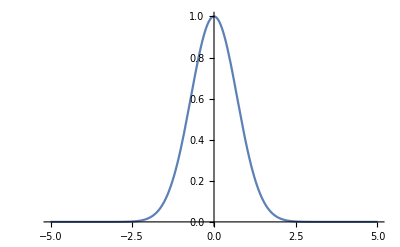

-Graphics-

```mathematica
Plot[Exp[-x^2],{x,-5,5}]
Plot[Exp[-x^2]/.x->(1+I)*z,{z,-5,5}]
```

#### Try |km|^eta = [(km+i0)(-km+i0)]^eta/2, so cant use contours necessarily

```mathematica
(* branch cut between km=-I*zerop and km=I*zerop *)
igral4=(  (km+I*zerop)(km-I*zerop)  )^(eta/2)(p1m-km)/((SPD[k]+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop))
%//lcCompAll
igrals4=%/.p1p->0/.Vperp[p1]->0



2Pi*I( Simplify[Residue[igrals4,{km,(-SPD[Vperp[k]]-I*zerop)/kp}]/.zerop->0]+Simplify[Residue[igrals4,{km,(p1m*kp-SPD[Vperp[k]]-I*zerop)/(kp)}]/.zerop->0])
%/.SPD[Vperp[k]]->-QT^2//Simplify//Expand



igrandKp4=Expand[%]

If[(Head[igrandKp4//Expand]==Plus),
For[i=1,i<=(Length[igrandKp4//Expand]),i++,
Expand[igrandKp4][[i]]//expFracs//myPrint;
];
];
```

((p_1^--k^-) ((k^--ⅈ 0^+) (k^-+ⅈ 0^+))^(η/2))/((k^2+ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^+-2 k·p_1+k^2))

((p_1^--k^-) ((k^--ⅈ 0^+) (k^-+ⅈ 0^+))^(η/2))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

((p_1^--k^-) ((k^--ⅈ 0^+) (k^-+ⅈ 0^+))^(η/2))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

2 ⅈ π (((k_⊥)^2 ((((k_⊥)^2-k^+ p_1^-)^2)/((k^+)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^--(k_⊥)^2))+(((k_⊥)^4/((k^+)^2))^((η+2)/2) (k^+ p_1^-+(k_⊥)^2))/(p_1^- (k_⊥)^6))

(2 ⅈ π (Q_T^4/((k^+)^2))^(η/2))/((k^+)^2 p_1^-)-(2 ⅈ π Q_T^2 (((k^+ p_1^-+Q_T^2)^2)/((k^+)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))-(2 ⅈ π (Q_T^4/((k^+)^2))^(η/2))/(k^+ Q_T^2)

(2 ⅈ π (Q_T^4/((k^+)^2))^(η/2))/((k^+)^2 p_1^-)-(2 ⅈ π Q_T^2 (((k^+ p_1^-+Q_T^2)^2)/((k^+)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))-(2 ⅈ π (Q_T^4/((k^+)^2))^(η/2))/(k^+ Q_T^2)

expFracs(Expand[igrandKp4]⟦i⟧)=-(2 ⅈ π (Q_T^4)^(η/2) (k^+)^(-η-1))/Q_T^2

expFracs(Expand[igrandKp4]⟦i⟧)=(2 ⅈ π (Q_T^4)^(η/2) (k^+)^(-η-2))/p_1^-

expFracs(Expand[igrandKp4]⟦i⟧)=-(2 ⅈ π Q_T^2 (k^+)^(-η-2) ((Q_T^2+k^+ p_1^-)^2)^(η/2))/(p_1^- (Q_T^2+k^+ p_1^-))

```mathematica
Integrate[x^(-1-eps+eta),{x,0,lambda},Assumptions->eta>0]
Integrate[x^(-1-eps+eta),{x,lambda,Infinity},Assumptions->lambda>0&&eta>0]
```

ConditionalExpression[-λ^(η-ϵ)/(ϵ-η),η>Re(ϵ)]

ConditionalExpression[λ^(η-ϵ)/(ϵ-η),η<Re(ϵ)]

```mathematica
(Expand[igrandKp4][[3]])(QT^2)^(-eps)//expFracs//Simplify

Integrate[%,{kp,-Infinity,0},Assumptions->p1m>0&&QT>0]
(%//Normal//Simplify)/.delta->0
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand
%/.(QT)^(a_):>(QT^2)^Expand[a/2]
almost4=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

-(2 ⅈ π (k^+)^(-η-2) (Q_T^2)^(1-ϵ) ((k^+ p_1^-+Q_T^2)^2)^(η/2))/(p_1^- (k^+ p_1^-+Q_T^2))

Integrate::idiv: Integral of \!
\(TraditionalForm\`\(\((\(-Integrate`$$a$325014\))\)\^\(\(\(-η\)\) - 2\)\ 
      \*TemplateBox[List[RowBox[List[SubsuperscriptBox["Q", "T", "2"], "-", 
            RowBox[List["Integrate`$$a$325014", " ", SubsuperscriptBox["p", "1", "-"]]]]]], "Abs"]\^η\)\/
    \(Q\_T\%2 - \(\(Integrate`$$a$325014\ \(p\_1\%-\)\)\)\)\)
 does not converge on TraditionalForm`{0, ∞}.

Integrate[-(2 ⅈ π (k^+)^(-η-2) (Q_T^2)^(1-ϵ) ((k^+ p_1^-+Q_T^2)^2)^(η/2))/(p_1^- (k^+ p_1^-+Q_T^2)),{k^+,-∞,0},Assumptions→p_1^->0∧Q_T>0]

Integrate[-(2 ⅈ π (k^+)^(-η-2) (Q_T^2)^(1-ϵ) ((k^+ p_1^-+Q_T^2)^2)^(η/2))/(p_1^- (k^+ p_1^-+Q_T^2)),{k^+,-∞,0},Assumptions→p_1^->0∧Q_T>0]

Integrate[-(2 ⅈ π (k^+)^(-η-2) (Q_T^2)^(1-ϵ) ((k^+ p_1^-+Q_T^2)^2)^(η/2))/(p_1^- (k^+ p_1^-+Q_T^2)),{k^+,-∞,0},Assumptions→p_1^->0∧Q_T>0]

«3 more identical outputs»

Integrate::idiv: Integral of \!
\(TraditionalForm\`\(\((\(-Integrate`$$a$328731\))\)\^\(\(\(-η\)\) - 2\)\ 
      \*TemplateBox[List[RowBox[List[SubsuperscriptBox["Q", "T", "2"], "-", 
            RowBox[List["Integrate`$$a$328731", " ", SubsuperscriptBox["p", "1", "-"]]]]]], "Abs"]\^η\)\/
    \(Q\_T\%2 - \(\(Integrate`$$a$328731\ \(p\_1\%-\)\)\)\)\)
 does not converge on TraditionalForm`{0, ∞}.

Integrate[-(2 ⅈ π (k^+)^(-η-2) (Q_T^2)^(1-ϵ) ((k^+ p_1^-+Q_T^2)^2)^(η/2))/(p_1^- (k^+ p_1^-+Q_T^2)),{k^+,-∞,0},Assumptions→p_1^->0∧Q_T>0]

Integrate[-(2 ⅈ π (k^+)^(-η-2) (Q_T^2)^(1-ϵ) ((k^+ p_1^-+Q_T^2)^2)^(η/2))/(p_1^- (k^+ p_1^-+Q_T^2)),{k^+,-∞,0},Assumptions→p_1^->0∧Q_T>0]

```mathematica
almost4*2*I*g^2*Cf*ups1^eta*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2/2//Normal
%//replacementg
%/.zerop->0/.D->4-2*eps

Series[%,{eta,0,0}]//Normal
Series[%,{z,0,0}]//Normal
Series[%,{eps,0,0}]//Normal
soClose4=Limit[%,zerop->0]
```

(ⅈ 2^-D π^((D-2)/2-D) g^2 C_F υ_1^η ((2 ⅈ π^2 csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)))/((D-2)/2)

1/(4 (D-2)/2)ⅈ ⅇ^(1/2 ℽ (4-D)) π^((D-4)/2+(D-2)/2-D+1) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^((4-D)/2) ((2 ⅈ π^2 csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1))

1/(4 1/2 (2-2 ϵ))ⅈ ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-3) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ ((2 ⅈ π^2 csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1))

(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^(-z-ϵ) (z (λ^2)^z (μ_OverBar[MS]^2)^ϵ-ϵ (λ^2)^ϵ (μ_OverBar[MS]^2)^z))/(4 π η z ϵ 1/2 (2-2 ϵ))+1/(4 π z^2 ϵ^2 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^(-z-ϵ) (-2 z^2 ϵ log(p_1^-) (λ^2)^z (μ_OverBar[MS]^2)^ϵ+2 z ϵ^2 log(p_1^-) (λ^2)^ϵ (μ_OverBar[MS]^2)^z+z^2 ϵ log(υ_1) (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 (λ^2)^z (μ_OverBar[MS]^2)^ϵ-2 ⅈ π z^2 ϵ (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 ϵ (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 ϵ log(λ^2) (λ^2)^z (μ_OverBar[MS]^2)^ϵ-z ϵ^2 log(υ_1) (λ^2)^ϵ (μ_OverBar[MS]^2)^z+2 ⅈ π z ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-z ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-z ϵ^2 log(λ^2) (λ^2)^ϵ (μ_OverBar[MS]^2)^z)

1/(4 π ϵ^2 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) C_F α_OverBar[MS] ((λ^2)^-ϵ (2 ϵ^2 log(p_1^-) (λ^2)^ϵ log(μ_OverBar[MS]^2)-2 ϵ log(p_1^-) (μ_OverBar[MS]^2)^ϵ-ϵ^2 log(υ_1) (λ^2)^ϵ log(μ_OverBar[MS]^2)-1/2 ϵ^2 (λ^2)^ϵ log^2(μ_OverBar[MS]^2)+2 ⅈ π ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2)-ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2)-ϵ^2 log(λ^2) (λ^2)^ϵ log(μ_OverBar[MS]^2)+ϵ log(λ^2) (μ_OverBar[MS]^2)^ϵ+ϵ log(υ_1) (μ_OverBar[MS]^2)^ϵ-2 ⅈ π ϵ (μ_OverBar[MS]^2)^ϵ+ϵ (μ_OverBar[MS]^2)^ϵ+(μ_OverBar[MS]^2)^ϵ)-ϵ^2 log(λ^2) (-log(λ^2)-log(μ_OverBar[MS]^2)+2 log(p_1^-)-log(υ_1)+2 ⅈ π-1)-1/2 ϵ^2 log^2(λ^2))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (-η log(υ_1)+2 ⅈ π η-η+η (-log(μ_OverBar[MS]^2))+2 η log(p_1^-)-1))/(4 π η z 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] ((λ^2)^-ϵ ((μ_OverBar[MS]^2)^ϵ-ϵ (λ^2)^ϵ log(μ_OverBar[MS]^2))+ϵ log(λ^2)))/(4 π η ϵ 1/2 (2-2 ϵ))-(ⅇ^(ℽ ϵ) C_F α_OverBar[MS])/(4 π z^2 1/2 (2-2 ϵ))

(C_F α_OverBar[MS])/(4 π ϵ^2)-1/48 π C_F α_OverBar[MS]+(η C_F α_OverBar[MS] log(υ_1)+η C_F α_OverBar[MS]-2 ⅈ π η C_F α_OverBar[MS]+C_F α_OverBar[MS]-2 η C_F α_OverBar[MS] log(p_1^-)+η C_F α_OverBar[MS] log(μ_OverBar[MS]^2))/(4 π η ϵ)+(C_F α_OverBar[MS] (-η log(υ_1)+2 ⅈ π η-η+η (-log(μ_OverBar[MS]^2))+2 η log(p_1^-)-1))/(4 π η z)-(C_F α_OverBar[MS])/(4 π z^2)

-1/(48 π η z^2 ϵ^2)C_F α_OverBar[MS] (-12 η z ϵ (z-ϵ) log(μ_OverBar[MS]^2)+24 η z^2 ϵ log(p_1^-)-24 η z ϵ^2 log(p_1^-)-12 η z^2+π^2 η z^2 ϵ^2+24 ⅈ π η z^2 ϵ-12 η z^2 ϵ-12 z^2 ϵ-24 ⅈ π η z ϵ^2+12 η z ϵ^2+12 z ϵ^2-12 η z ϵ log(υ_1) (z-ϵ)+12 η ϵ^2)

```mathematica
Collect2[soClose4,eps,eta]//replacementalphaMS;
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
%/.Log[p1m]->LQ-Log[p2p]+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%(*-alphabar/2(1/eps-1/z)*)
Collect2[%,eps,eta,z]//FullSimplify


%//expLogs//Simplify
Collect2[2%,eps,eta,z]
```

(ᾱ)/(2 ϵ^2)+(ᾱ)/(2 η ϵ)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+log(υ_1)-2 ⅈ π+1))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+12 z log(υ_1)-24 ⅈ π z+12 z+12))/(24 z^2)-(ᾱ)/(2 η z)

(ᾱ)/ϵ^2+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_2^+)+log(1/υ_2)-2 ⅈ π+1))/(2 ϵ)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+log(υ_1)-2 ⅈ π+1))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_2^+)+π^2 z^2+12 z log(1/υ_2)-24 ⅈ π z+12 z+12))/(24 z^2)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+12 z log(υ_1)-24 ⅈ π z+12 z+12))/(24 z^2)

(ᾱ)/ϵ^2+(ᾱ (2 log(μ_OverBar[MS]^2)-2 log(p_2^+)-2 log(p_1^-)+log(υ_1)+log(1/υ_2)-4 ⅈ π+2))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+6 z log(υ_1)+6 z log(1/υ_2)-24 ⅈ π z+12 z+12))/(12 z^2)

-(ᾱ (2 LQ z^2 ϵ-2 LQ z ϵ^2+ζ_2 z^2 ϵ^2+4 ⅈ π z^2 ϵ-2 z^2 ϵ-2 z^2-4 ⅈ π z ϵ^2+2 z ϵ^2+z ϵ log(υ_1) (ϵ-z)+z ϵ log(1/υ_2) (ϵ-z)+2 ϵ^2))/(2 z^2 ϵ^2)

1/2 ᾱ (-(-2 LQ z+ζ_2 z^2+z log(υ_1)+z log(1/υ_2)-4 ⅈ π z+2 z+2)/z^2+(-2 LQ+log(υ_1)+log(1/υ_2)-4 ⅈ π+2)/ϵ+2/ϵ^2)

1/2 ᾱ (-(-2 LQ z+ζ_2 z^2+z log(υ_1)+z log(1/υ_2)-4 ⅈ π z+2 z+2)/z^2+(-2 LQ+log(υ_1)+log(1/υ_2)-4 ⅈ π+2)/ϵ+2/ϵ^2)

1/2 ᾱ (-ζ_2-(-2 LQ+log(υ_1)+log(1/υ_2)-4 ⅈ π+2)/z+(-2 LQ+log(υ_1)+log(1/υ_2)-4 ⅈ π+2)/ϵ-2/z^2+2/ϵ^2)

1/2 ᾱ (-ζ_2+(2 LQ-log(υ_1)+log(υ_2)+4 ⅈ π-2)/z+(-2 LQ+log(υ_1)-log(υ_2)-4 ⅈ π+2)/ϵ-2/z^2+2/ϵ^2)

-ζ_2 ᾱ+(2 ᾱ)/ϵ^2-(ᾱ (2 LQ-log(υ_1)+log(υ_2)+4 ⅈ π-2))/ϵ+(ᾱ (2 LQ-log(υ_1)+log(υ_2)+4 ⅈ π-2))/z-(2 ᾱ)/z^2

#### Try km contours first, mixed regulator

```mathematica
(* branch cut extending from km =0 to km = -I*infinity *)
igral1=(km/nu1)^eta1*Exp[-eta2*kp/nu2](p1m-km)/((SPD[k]+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop))
%//lcCompAll
igrals1=%/.p1p->0/.Vperp[p1]->0



2Pi*I( Simplify[Residue[igrals1,{km,(-SPD[Vperp[k]]-I*zerop)/kp}]/.zerop->0]+Simplify[Residue[igrals1,{km,(p1m*kp-SPD[Vperp[k]]-I*zerop)/(kp)}]/.zerop->0])
%/.SPD[Vperp[k]]->-QT^2//Expand



igrandKp1=Expand[%]

If[(Head[igrandKp1//Expand]==Plus),
For[i=1,i<=(Length[igrandKp1//Expand]),i++,
Expand[igrandKp1][[i]]//expFracs//myPrint;
];
];
```

((p_1^--k^-) ⅇ^(-(η_2 k^+)/ν_2) (k^-/ν_1)^η_1)/((k^2+ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^+-2 k·p_1+k^2))

((p_1^--k^-) ⅇ^(-(η_2 k^+)/ν_2) (k^-/ν_1)^η_1)/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

((p_1^--k^-) ⅇ^(-(η_2 k^+)/ν_2) (k^-/ν_1)^η_1)/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

2 ⅈ π (((k_⊥)^2 ⅇ^(-(η_2 k^+)/ν_2) ((k^+ p_1^--(k_⊥)^2)/(k^+ ν_1))^(η_1-1))/((k^+)^3 ν_1 p_1^-)+(ⅇ^(-(η_2 k^+)/ν_2) (k^+ p_1^-+(k_⊥)^2) (-(k_⊥)^2/(k^+ ν_1))^η_1)/((k^+)^2 p_1^- (k_⊥)^2))

-(2 ⅈ π Q_T^2 ⅇ^(-(η_2 k^+)/ν_2) ((k^+ p_1^-+Q_T^2)/(k^+ ν_1))^(η_1-1))/((k^+)^3 ν_1 p_1^-)+(2 ⅈ π ⅇ^(-(η_2 k^+)/ν_2) (Q_T^2/(k^+ ν_1))^η_1)/((k^+)^2 p_1^-)-(2 ⅈ π ⅇ^(-(η_2 k^+)/ν_2) (Q_T^2/(k^+ ν_1))^η_1)/(k^+ Q_T^2)

-(2 ⅈ π Q_T^2 ⅇ^(-(η_2 k^+)/ν_2) ((k^+ p_1^-+Q_T^2)/(k^+ ν_1))^(η_1-1))/((k^+)^3 ν_1 p_1^-)+(2 ⅈ π ⅇ^(-(η_2 k^+)/ν_2) (Q_T^2/(k^+ ν_1))^η_1)/((k^+)^2 p_1^-)-(2 ⅈ π ⅇ^(-(η_2 k^+)/ν_2) (Q_T^2/(k^+ ν_1))^η_1)/(k^+ Q_T^2)

expFracs(Expand[igrandKp1]⟦i⟧)=-2 ⅈ ⅇ^(-(η_2 k^+)/ν_2) ν_1^-η_1 π (Q_T^2)^(η_1-1) (1/k^+)^(η_1+1)

expFracs(Expand[igrandKp1]⟦i⟧)=(2 ⅈ ⅇ^(-(η_2 k^+)/ν_2) ν_1^-η_1 π (Q_T^2)^η_1 (1/k^+)^(η_1+2))/p_1^-

expFracs(Expand[igrandKp1]⟦i⟧)=-(2 ⅈ ⅇ^(-(η_2 k^+)/ν_2) ν_1^-η_1 π Q_T^2 (1/k^+)^(η_1+2) (Q_T^2+k^+ p_1^-)^(η_1-1))/p_1^-

```mathematica
Expand[igrandKp1][[1]](QT^2)^(-eps)//expFracs

Integrate[%,{kp,-Infinity,0},Assumptions->p1m>0&&QT>0]
(%//Normal//FullSimplify)(*/.delta->0*)//expFracs
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^Expand[a/2+eta/2]//Expand
%/.(QT^4)^a_:>(QT^2)^Expand[2a]/.(QT)^(a_):>(QT^2)^(Expand[a/2])
almost1=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

-2 ⅈ π ν_1^-η_1 (1/k^+)^(η_1+1) ⅇ^(-(η_2 k^+)/ν_2) (Q_T^2)^(η_1-ϵ-1)

ConditionalExpression[-2 ⅈ π (-1)^(η_1+1) ν_1^-η_1 (-η_2/ν_2)^η_1 -η_1 Q_T^(2 η_1-2 ϵ-2),Re(η_2/ν_2)<0∧Re(η_1)<0]

2 ⅈ π (-1)^(2 η_1) η_2^η_1 ν_1^-η_1 ν_2^-η_1 -η_1 Q_T^(2 η_1-2 ϵ-2)

2 ⅈ π (-1)^(2 η_1) η_2^η_1 ν_1^-η_1 ν_2^-η_1 -η_1 Q_T^(2 η_1-2 ϵ-2)

2 ⅈ π (-1)^(2 η_1) η_2^η_1 ν_1^-η_1 ν_2^-η_1 -η_1 Q_T^(2 η_1-2 ϵ-2)

«2 more identical outputs»

2 ⅈ π (-1)^(2 η_1) η_2^η_1 ν_1^-η_1 ν_2^-η_1 -η_1 (Q_T^2)^(η_1-ϵ-1)

2 ⅈ π (-1)^(2 η_1) η_2^η_1 ν_1^-η_1 ν_2^-η_1 -η_1 (((λ^2)^(η_1-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η_1-z)-((λ^2)^(η_1-ϵ))/(η_1-ϵ))

```mathematica
almost1*2*I*g^2*Cf*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2/2//Normal
%//replacementg//replacementalphaMS
%/.zerop->0/.D->4-2*eps


Series[%,{eta1,0,0}]//Normal
Series[%,{eta2,0,0}]//Normal
Series[%,{z,0,0}]//Normal
Series[%,{eps,0,0}]//Normal

soClose1=Limit[%,zerop->0]
```

(2^(1-D) π^((D-2)/2-D+1) (-1)^(2 η_1+1) η_2^η_1 g^2 C_F ν_1^-η_1 ν_2^-η_1 -η_1 (((λ^2)^(η_1-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η_1-z)-((λ^2)^(η_1-ϵ))/(η_1-ϵ)))/((D-2)/2)

(ⅇ^(1/2 ℽ (4-D)) π^((D-4)/2+(D-2)/2-D+3) (-1)^(2 η_1+1) η_2^η_1 ᾱ ν_1^-η_1 ν_2^-η_1 -η_1 (μ_OverBar[MS]^2)^((4-D)/2) (((λ^2)^(η_1-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η_1-z)-((λ^2)^(η_1-ϵ))/(η_1-ϵ)))/((D-2)/2)

((-1)^(2 η_1+1) η_2^η_1 ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-1) ᾱ ν_1^-η_1 ν_2^-η_1 -η_1 (μ_OverBar[MS]^2)^ϵ (((λ^2)^(η_1-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η_1-z)-((λ^2)^(η_1-ϵ))/(η_1-ϵ)))/(1/2 (2-2 ϵ))

(ⅇ^(ℽ ϵ) ᾱ (λ^2)^(-z-ϵ) (z (λ^2)^z (μ_OverBar[MS]^2)^ϵ-ϵ (λ^2)^ϵ (μ_OverBar[MS]^2)^z))/(η_1 z ϵ 1/2 (2-2 ϵ))+1/(1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-1) ᾱ (μ_OverBar[MS]^2)^ϵ (-((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z^2-(-log(η_2)+log(ν_1)+log(ν_2)-2 ⅈ π) (((λ^2)^-ϵ)/ϵ-((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z)-ℽ (((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z-((λ^2)^-ϵ)/ϵ)-(log(λ^2) (λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z+((λ^2)^-ϵ)/ϵ^2+(log(λ^2) (λ^2)^-ϵ)/ϵ)

(ⅇ^(ℽ ϵ) ᾱ (λ^2)^(-z-ϵ) (z (λ^2)^z (μ_OverBar[MS]^2)^ϵ-ϵ (λ^2)^ϵ (μ_OverBar[MS]^2)^z))/(η_1 z ϵ 1/2 (2-2 ϵ))+1/(1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-1) ᾱ (μ_OverBar[MS]^2)^ϵ (-((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z^2+(log(η_2)-log(ν_1)-log(ν_2)+2 ⅈ π) (((λ^2)^-ϵ)/ϵ-((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z)-ℽ (((λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z-((λ^2)^-ϵ)/ϵ)-(log(λ^2) (λ^2)^-z (μ_OverBar[MS]^2)^(z-ϵ))/z+((λ^2)^-ϵ)/ϵ^2+(log(λ^2) (λ^2)^-ϵ)/ϵ)

1/(1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-1) ᾱ (μ_OverBar[MS]^2)^ϵ ((log(η_2)-log(ν_1)-log(ν_2)+2 ⅈ π) (((λ^2)^-ϵ)/ϵ-(μ_OverBar[MS]^2)^-ϵ (log(μ_OverBar[MS]^2)-log(λ^2)))-1/2 (μ_OverBar[MS]^2)^-ϵ (log(μ_OverBar[MS]^2)-log(λ^2))^2-log(λ^2) (μ_OverBar[MS]^2)^-ϵ (log(μ_OverBar[MS]^2)-log(λ^2))+ℽ (((λ^2)^-ϵ)/ϵ-(μ_OverBar[MS]^2)^-ϵ (log(μ_OverBar[MS]^2)-log(λ^2)))+((λ^2)^-ϵ)/ϵ^2+(log(λ^2) (λ^2)^-ϵ)/ϵ)+(ⅇ^(ℽ ϵ) ᾱ ((λ^2)^-ϵ ((μ_OverBar[MS]^2)^ϵ-ϵ (λ^2)^ϵ log(μ_OverBar[MS]^2))+ϵ log(λ^2)))/(η_1 ϵ 1/2 (2-2 ϵ))-(ⅇ^(ℽ ϵ) ᾱ (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 z 1/2 (2-2 ϵ))-(ⅇ^(ℽ ϵ) ᾱ)/(z^2 1/2 (2-2 ϵ))

(ᾱ)/ϵ^2-(π^2 ᾱ)/12+((ᾱ)/η_1+ᾱ (log(η_2)-log(ν_1)-log(ν_2)+log(μ_OverBar[MS]^2)+2 ⅈ π+ℽ))/ϵ-(ᾱ (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 z)-(ᾱ)/z^2

(ᾱ)/ϵ^2-(π^2 ᾱ)/12+(ᾱ (1/η_1+log(η_2)-log(ν_1)-log(ν_2)+log(μ_OverBar[MS]^2)+2 ⅈ π+ℽ))/ϵ-(ᾱ (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 z)-(ᾱ)/z^2

```mathematica
Collect2[soClose1,eps,eta,z]//replacementalphaMS;
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
%/.Log[p1m]->LQ-Log[p2p]+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%(*-alphabar/2(1/eps-1/z)*)
Collect2[%,eps,eta,z]/. 2LQ-4Log[p2p]->2Log[p1m^2/p2p^2]-4Log[muMS]

Series[%,{eps,0,-1}]//Normal
%//expLogs//Simplify
Collect2[%,eps,z,eta1,eta2]
```

(ᾱ)/ϵ^2+(ᾱ (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 ϵ)-(ᾱ (12 η_1+12 η_1 z log(μ_OverBar[MS]^2)+π^2 η_1 z^2-12 η_1 z log(ν_1)-12 η_1 z log(ν_2)+24 ⅈ π η_1 z+12 ℽ η_1 z+12 η_1 z log(η_2)+12 z))/(12 η_1 z^2)

(2 ᾱ)/ϵ^2+(2 ᾱ (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 ϵ)-(ᾱ (12 η_1+12 η_1 z log(μ_OverBar[MS]^2)+π^2 η_1 z^2-12 η_1 z log(ν_1)-12 η_1 z log(ν_2)+24 ⅈ π η_1 z+12 ℽ η_1 z+12 η_1 z log(η_2)+12 z))/(6 η_1 z^2)

(2 ᾱ)/ϵ^2+(2 ᾱ (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 ϵ)-(ᾱ (12 η_1+12 η_1 z log(μ_OverBar[MS]^2)+6 ζ_2 η_1 z^2-12 η_1 z log(ν_1)-12 η_1 z log(ν_2)+24 ⅈ π η_1 z+12 ℽ η_1 z+12 η_1 z log(η_2)+12 z))/(6 η_1 z^2)

ᾱ (-(2 η_1+2 η_1 z log(μ_OverBar[MS]^2)+ζ_2 η_1 z^2-2 η_1 z log(ν_1)-2 η_1 z log(ν_2)+4 ⅈ π η_1 z+2 ℽ η_1 z+2 η_1 z log(η_2)+2 z)/(η_1 z^2)+(2 (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 ϵ)+2/ϵ^2)

ᾱ (-(2 η_1+2 η_1 z log(μ_OverBar[MS]^2)+ζ_2 η_1 z^2-2 η_1 z log(ν_1)-2 η_1 z log(ν_2)+4 ⅈ π η_1 z+2 ℽ η_1 z+2 η_1 z log(η_2)+2 z)/(η_1 z^2)+(2 (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 ϵ)+2/ϵ^2)

ᾱ (-(2 η_1+2 η_1 z log(μ_OverBar[MS]^2)+ζ_2 η_1 z^2-2 η_1 z log(ν_1)-2 η_1 z log(ν_2)+4 ⅈ π η_1 z+2 ℽ η_1 z+2 η_1 z log(η_2)+2 z)/(η_1 z^2)+(2 (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 ϵ)+2/ϵ^2)

-ζ_2 ᾱ+(2 ᾱ)/ϵ^2+(2 ᾱ (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 ϵ)-(2 ᾱ (-η_1 log(ν_1)-η_1 log(ν_2)+2 ⅈ π η_1+ℽ η_1+η_1 log(η_2)+η_1 log(μ_OverBar[MS]^2)+1))/(η_1 z)-(2 ᾱ)/z^2

(2 ᾱ)/ϵ^2+((2 ᾱ)/η_1+2 ᾱ log(η_2)-2 ᾱ log(ν_1)-2 ᾱ log(ν_2)+4 ⅈ π ᾱ+2 ℽ ᾱ+2 ᾱ log(μ_OverBar[MS]^2))/ϵ

(2 ᾱ (η_1+2 η_1 ϵ log(μ_OverBar[MS])-η_1 ϵ log(ν_1)-η_1 ϵ log(ν_2)+2 ⅈ π η_1 ϵ+ℽ η_1 ϵ+η_1 ϵ log(η_2)+ϵ))/(η_1 ϵ^2)

(2 ᾱ)/ϵ^2+(2 ᾱ)/(η_1 ϵ)+(2 ᾱ log(η_2))/ϵ+(2 ᾱ (-log(ν_1)-log(ν_2)+2 log(μ_OverBar[MS])+2 ⅈ π+ℽ))/ϵ

#### Try kp contours first (Roy way) NE (kp>0 km>0)

```mathematica
igralNE=(kp/km)^(+eta/2)/((SPD[k]+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop))
%//lcCompAll
%/.p1p->0/.Vperp[p1]->0
2Pi*I(Simplify[Residue[%,{kp,(-SPD[Vperp[k]]-I*zerop)/km}]/.zerop->0]+Simplify[Residue[%,{kp,(-SPD[Vperp[k]]-I*zerop)/(km-p1m)}]/.zerop->0])
igralsNE=%/.SPD[Vperp[k]]->-QT^2//Simplify



igrandKmNE=Expand[igralsNE]

If[(Head[igrandKmNE//Expand]==Plus),
For[i=1,i<=(Length[igrandKmNE//Expand]),i++,
Expand[igrandKmNE][[i]]//myPrint;
];
];
```

((k^+/k^-)^(η/2))/((k^2+ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^+-2 k·p_1+k^2))

((k^+/k^-)^(η/2))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

((k^+/k^-)^(η/2))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

2 ⅈ π (-((-(k_⊥)^2/((k^-)^2))^((η-2)/2))/((k^-)^3 p_1^-)-((-(k_⊥)^2/((k^-)^2-k^- p_1^-))^(η/2))/(k^- p_1^- (k_⊥)^2))

-(2 ⅈ π ((Q_T^2/((k^-)^2))^(η/2)-(Q_T^2/((k^-)^2-k^- p_1^-))^(η/2)))/(k^- p_1^- Q_T^2)

(2 ⅈ π (Q_T^2/((k^-)^2-k^- p_1^-))^(η/2))/(k^- p_1^- Q_T^2)-(2 ⅈ π (Q_T^2/((k^-)^2))^(η/2))/(k^- p_1^- Q_T^2)

Expand[igrandKmNE]⟦i⟧=-(2 ⅈ π (Q_T^2/((k^-)^2))^(η/2))/(Q_T^2 k^- p_1^-)

Expand[igrandKmNE]⟦i⟧=(2 ⅈ π (Q_T^2/((k^-)^2-k^- p_1^-))^(η/2))/(Q_T^2 k^- p_1^-)

```mathematica
Expand[igrandKmNE][[2]]*(p1m-km)*(QT^2)^(-eps)(*//expFracs*)
%*p1m/.km->x*p1m
Integrate[%,{x,0,1},Assumptions->p1m>0&&p1m≠1 &&QT>0]
%//Normal//FullSimplify
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand
%/.(QT^4)^(a_):>(QT^2)^(Expand[2a])/.(QT)^a_:>(QT^2)^(Expand[a/2])
almostKmNEp1m=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

(2 ⅈ π (p_1^--k^-) (Q_T^2)^(-ϵ-1) ((√(Q_T^4/((k^--p_1^-)^2)))/k^-)^(η/2))/(k^- p_1^-)

(2 ⅈ π (p_1^--p_1^- x) (Q_T^2)^(-ϵ-1) ((√(Q_T^4/((p_1^- x-p_1^-)^2)))/(p_1^- x))^(η/2))/(p_1^- x)

ConditionalExpression[-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η 3/2-η/2),Re(η)<0]

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η 3/2-η/2)

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η 3/2-η/2)

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η 3/2-η/2)

«1 more identical outputs»

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η (Q_T^2)^(η/2-ϵ-1))/(η 3/2-η/2)

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η (Q_T^2)^(η/2-ϵ-1))/(η 3/2-η/2)

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η 3/2-η/2)

```mathematica
Expand[igrandKmNE][[2]]*(-(km-p1m))*(QT^2)^(-eps)//expFracs
Integrate[%,{km,p1m,Infinity},Assumptions->p1m>0&&QT>0]
%//Normal//FullSimplify
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a);
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a);
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand;
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand;
%/.(QT^4)^(a_):>(QT^2)^(Expand[2a])/.(QT)^a_:>(QT^2)^(Expand[a/2])
almostKmNEInfty=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

(2 ⅈ π (k^-)^(-η/2-1) (p_1^--k^-) (k^--p_1^-)^(-η/2) (Q_T^4)^(η/4) (Q_T^2)^(-ϵ-1))/p_1^-

ConditionalExpression[-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η/2+1),1<Re(η)<4]

-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η/2+1)

-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η (Q_T^2)^(η/2-ϵ-1))/(η/2+1)

-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η/2+1)

```mathematica
(almostKmNEp1m(*+almostKmNEInfty*))*2*I*g^2*Cf*ups1^eta*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2/2//Normal
%//replacementg;
%/.zerop->0/.D->4-2*eps

%(*/(1-Exp[I*Pi*eta])*) (* don't forget about this! *)//replacePolyGamma

Series[%,{eta,0,0}]//Normal;
Series[%,{z,0,0}]//Normal;
Series[%,{eps,0,0}]//Normal
soCloseNE=Limit[%,zerop->0]
```

(π^((D-2)/2-D+3/2) g^2 C_F 2^(-D+η+1) υ_1^η 2-η/2 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η (D-2)/2 3/2-η/2)

(2^(η-1) ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-3/2) C_F υ_1^η 2-η/2 α_OverBar[MS] (p_1^-)^-η (μ_OverBar[MS]^2)^ϵ (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η 3/2-η/2 1/2 (2-2 ϵ))

(2^(η-1) ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-3/2) C_F υ_1^η 2-η/2 α_OverBar[MS] (p_1^-)^-η (μ_OverBar[MS]^2)^ϵ (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η 3/2-η/2 1/2 (2-2 ϵ))

(C_F α_OverBar[MS])/(2 π ϵ^2)-1/24 π C_F α_OverBar[MS]+((C_F α_OverBar[MS])/(π η)+(C_F α_OverBar[MS] (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+ℽ-1+2 log(2)+03/2))/(2 π))/ϵ-(C_F α_OverBar[MS] (2 η log(υ_1)+ℽ η-η+2 η log(2)+η 03/2+η log(μ_OverBar[MS]^2)-2 η log(p_1^-)+2))/(2 π η z)-(C_F α_OverBar[MS])/(2 π z^2)

-1/(24 π η z^2 ϵ^2)C_F α_OverBar[MS] (-12 η z ϵ (z-ϵ) log(μ_OverBar[MS]^2)+24 η z^2 ϵ log(p_1^-)-24 η z ϵ^2 log(p_1^-)-12 η z^2+π^2 η z^2 ϵ^2-12 ℽ η z^2 ϵ+12 η z^2 ϵ-24 η z^2 ϵ log(2)-12 η z^2 ϵ 03/2-24 z^2 ϵ+12 ℽ η z ϵ^2-12 η z ϵ^2+24 η z ϵ^2 log(2)+12 η z ϵ^2 03/2+24 z ϵ^2-24 η z ϵ log(υ_1) (z-ϵ)+12 η ϵ^2)

```mathematica
Collect2[soCloseNE,eps,eta,z]//replacementalphaMS//replacePolyGamma
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
%/.Log[p1m]->LQ-Log[p2p]+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%-alphabar/2(1/eps-1/z)//Simplify
Collect2[%,eps,eta,z]
Series[%,{eps,0,-1}]//Normal
```

(ᾱ)/ϵ^2+(2 ᾱ)/(η ϵ)-(π^2 ᾱ)/12+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)-1+2 log(2)+2 (1-log(2))))/ϵ-(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)-1+2 log(2)+2 (1-log(2))))/z-(ᾱ)/z^2-(2 ᾱ)/(η z)

(ᾱ)/ϵ^2+(2 ᾱ)/(η ϵ)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+1))/ϵ-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+24 z log(υ_1)+12 z+12))/(12 z^2)-(2 ᾱ)/(η z)

(2 ᾱ)/ϵ^2+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_2^+)+2 log(1/υ_2)+1))/ϵ+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+1))/ϵ-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_2^+)+π^2 z^2+24 z log(1/υ_2)+12 z+12))/(12 z^2)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+24 z log(υ_1)+12 z+12))/(12 z^2)

(2 ᾱ)/ϵ^2+(2 ᾱ (log(μ_OverBar[MS]^2)-log(p_2^+)-log(p_1^-)+log(υ_1)+log(1/υ_2)+1))/ϵ-(ᾱ (12 z log(μ_OverBar[MS]^2)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+12 z log(υ_1)+12 z log(1/υ_2)+12 z+12))/(6 z^2)

-(ᾱ (2 LQ z^2 ϵ-2 LQ z ϵ^2+ζ_2 z^2 ϵ^2-2 z^2 ϵ-2 z^2+2 z ϵ^2+2 z ϵ log(υ_1) (ϵ-z)+2 z ϵ log(1/υ_2) (ϵ-z)+2 ϵ^2))/(z^2 ϵ^2)

ᾱ (-(-2 LQ z+ζ_2 z^2+2 z log(υ_1)+2 z log(1/υ_2)+2 z+2)/z^2+(2 (-LQ+log(υ_1)+log(1/υ_2)+1))/ϵ+2/ϵ^2)

1/2 ᾱ (2 (-(-2 LQ z+ζ_2 z^2+2 z log(υ_1)+2 z log(1/υ_2)+2 z+2)/z^2+(2 (-LQ+log(υ_1)+log(1/υ_2)+1))/ϵ+2/ϵ^2)+1/z-1/ϵ)

-ζ_2 ᾱ+(2 ᾱ)/ϵ^2-(ᾱ (4 LQ-4 log(υ_1)-4 log(1/υ_2)-3))/(2 ϵ)+(ᾱ (4 LQ-4 log(υ_1)-4 log(1/υ_2)-3))/(2 z)-(2 ᾱ)/z^2

(2 ᾱ)/ϵ^2+(2 ᾱ log(υ_1)+2 ᾱ log(1/υ_2)+(3 ᾱ)/2-2 LQ ᾱ)/ϵ

#### Try kp contours first (Roy way) SE (kp>0 km<0)

```mathematica
igralSE=(kp/x)^(+eta/2)/((SPD[k]+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop))
%/.km->-x (* -infty<dkm<0 = 0<dx<infty *)
%//lcCompAll
%/.p1p->0/.Vperp[p1]->0/.SPD[Vperp[k]]->-QT^2
2Pi*I(Simplify[Residue[%,{kp,(QT^2-I*zerop)/(-x)}]/.zerop->0]+Simplify[Residue[%,{kp,(QT^2-I*zerop)/((-x)-p1m)}]/.zerop->0])
igralsSE=%//Simplify



igrandKmSE=Expand[igralsSE]

If[(Head[igrandKmSE//Expand]==Plus),
For[i=1,i<=(Length[igrandKmSE//Expand]),i++,
Expand[igrandKmSE][[i]]//expFracs//myPrint;
];
];
```

(((√((k^+)^2))/x)^(η/2))/((k^2+ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^+-2 k·p_1+k^2))

(((√((k^+)^2))/x)^(η/2))/((k^2+ⅈ 0^+) (-x+ⅈ 0^+) (ⅈ 0^+-2 k·p_1+k^2))

(((√((k^+)^2))/x)^(η/2))/((-x+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

(((√((k^+)^2))/x)^(η/2))/((-x+ⅈ 0^+) (ⅈ 0^+-k^+ x-Q_T^2) (ⅈ 0^+-k^+ p_1^--k^+ x-Q_T^2))

2 ⅈ π ((((√(Q_T^4/x^2))/x)^(η/2))/(p_1^- x Q_T^2)-(((√(Q_T^4/((p_1^-+x)^2)))/x)^(η/2))/(p_1^- x Q_T^2))

(2 ⅈ π (((√(Q_T^4/x^2))/x)^(η/2)-((√(Q_T^4/((p_1^-+x)^2)))/x)^(η/2)))/(p_1^- x Q_T^2)

(2 ⅈ π ((√(Q_T^4/x^2))/x)^(η/2))/(p_1^- x Q_T^2)-(2 ⅈ π ((√(Q_T^4/((p_1^-+x)^2)))/x)^(η/2))/(p_1^- x Q_T^2)

expFracs(Expand[igrandKmSE]⟦i⟧)=(2 ⅈ π (Q_T^4)^(η/4) x^(-η-1))/(Q_T^2 p_1^-)

expFracs(Expand[igrandKmSE]⟦i⟧)=-(2 ⅈ π (Q_T^4)^(η/4) x^(-η/2-1) (x+p_1^-)^(-η/2))/(Q_T^2 p_1^-)

```mathematica
Expand[igrandKmSE][[2]]*(p1m+x)*(QT^2)^(-eps)//expFracs
Integrate[%,{x,0,phi},Assumptions->p1m>0&&QT>0]
%//Normal//FullSimplify
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand
%/.(QT^4)^(a_):>(QT^2)^(Expand[2a])/.(QT)^a_:>(QT^2)^(Expand[a/2])
almostKmSElambda=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

-(2 ⅈ π x^(-η/2-1) (p_1^-+x)^(1-η/2) (Q_T^4)^(η/4) (Q_T^2)^(-ϵ-1))/p_1^-

ConditionalExpression[(4 ⅈ π (p_1^- ϕ)^(-η/2) (η-2)/2-η/21-η/2-ϕ/p_1^- Q_T^(η-2 ϵ-2))/η,Re(η)<0∧(Re(ϕ)≥0∨p_1^- Re(1/ϕ)≤-1∨ϕ∉ℝ)]

(4 ⅈ π (p_1^- ϕ)^(-η/2) (η-2)/2-η/21-η/2-ϕ/p_1^- Q_T^(η-2 ϵ-2))/η

(4 ⅈ π (p_1^- ϕ)^(-η/2) (η-2)/2-η/21-η/2-ϕ/p_1^- Q_T^(η-2 ϵ-2))/η

(4 ⅈ π (p_1^- ϕ)^(-η/2) (η-2)/2-η/21-η/2-ϕ/p_1^- Q_T^(η-2 ϵ-2))/η

«1 more identical outputs»

(4 ⅈ π (p_1^- ϕ)^(-η/2) (η-2)/2-η/21-η/2-ϕ/p_1^- (Q_T^2)^(η/2-ϵ-1))/η

(4 ⅈ π (p_1^- ϕ)^(-η/2) (η-2)/2-η/21-η/2-ϕ/p_1^- (Q_T^2)^(η/2-ϵ-1))/η

(4 ⅈ π (p_1^- ϕ)^(-η/2) (η-2)/2-η/21-η/2-ϕ/p_1^- (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/η

```mathematica
Expand[igrandKmSE][[2]]*(p1m+x)*(QT^2)^(-eps)//expFracs
Integrate[%,{x,phi,Infinity},Assumptions->p1m>0&&QT>0]
%//Normal//FullSimplify
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand
%/.(QT^4)^(a_):>(QT^2)^(Expand[2a])/.(QT)^a_:>(QT^2)^(Expand[a/2])
almostKmSEInfty=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

-(2 ⅈ π x^(-η/2-1) (p_1^-+x)^(1-η/2) (Q_T^4)^(η/4) (Q_T^2)^(-ϵ-1))/p_1^-

ConditionalExpression[-(2 ⅈ π ϕ^(1-η) (η-2)/2η-1η-p_1^-/ϕ Q_T^(η-2 ϵ-2))/((η-1) p_1^-),Re(η)>1∧Re(ϕ)>0∧Im(ϕ)==0]

-(2 ⅈ π ϕ^(1-η) η-1 (η-2)/2η-1η-p_1^-/ϕ Q_T^(η-2 ϵ-2))/p_1^-

-(2 ⅈ π ϕ^(1-η) η-1 (η-2)/2η-1η-p_1^-/ϕ Q_T^(η-2 ϵ-2))/p_1^-

-(2 ⅈ π ϕ^(1-η) η-1 (η-2)/2η-1η-p_1^-/ϕ Q_T^(η-2 ϵ-2))/p_1^-

«1 more identical outputs»

-(2 ⅈ π ϕ^(1-η) η-1 (η-2)/2η-1η-p_1^-/ϕ (Q_T^2)^(η/2-ϵ-1))/p_1^-

-(2 ⅈ π ϕ^(1-η) η-1 (η-2)/2η-1η-p_1^-/ϕ (Q_T^2)^(η/2-ϵ-1))/p_1^-

-(2 ⅈ π ϕ^(1-η) η-1 (η-2)/2η-1η-p_1^-/ϕ (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/p_1^-

```mathematica
(almostKmSElambda+almostKmSEInfty)*2*I*g^2*Cf*ups1^eta*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2/2//Normal
%//replacementg;
%/.zerop->0/.D->4-2*eps;

%(*/(1-Exp[I*Pi*eta])*)//replaceIncompleteBeta//replaceSpecificHypergeometric

seriesTermByTerm[%,{eta,0,1}]//Normal
Series[%,{z,0,0}]//Normal
Series[%,{eps,0,0}]//Normal
soCloseSE=Limit[%,zerop->0]
```

1/((D-2)/2)ⅈ 2^-D π^((D-2)/2-D) g^2 C_F υ_1^η ((4 ⅈ π (p_1^- ϕ)^(-η/2) (η-2)/2-η/21-η/2-ϕ/p_1^- (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/η-(2 ⅈ π ϕ^(1-η) η-1 (η-2)/2η-1η-p_1^-/ϕ (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/p_1^-)

1/(4 1/2 (2-2 ϵ))ⅈ ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-3) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ ((4 ⅈ π (1-(η ϕ)/(2 p_1^-)) (p_1^- ϕ)^(-η/2) (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/η-(2 ⅈ π η ϕ^(1-η) η-1 (-p_1^-/(η ϕ)+1/2 η (-(p_1^- 2-p_1^-/ϕ)/ϕ-(p_1^- log(p_1^-/ϕ+1))/ϕ-log(p_1^-/ϕ+1))+(3 p_1^-)/(2 ϕ)+1) (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/p_1^-)

Expanding -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-z) (ϕ p_1^-)^(-η/2) (μ_OverBar[MS]^2)^z)/((η/2-z) η 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-z) ϕ (ϕ p_1^-)^(-η/2) (μ_OverBar[MS]^2)^z)/(2 (η/2-z) 1/2 (2-2 ϵ) p_1^-)+(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η (λ^2)^(η/2-z) ϕ^-η η-1 (μ_OverBar[MS]^2)^z)/(4 (η/2-z) 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-z) ϕ^-η η-1 (μ_OverBar[MS]^2)^z)/(2 (η/2-z) 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-z) ϕ^-η η-1 log(p_1^-/ϕ+1) (μ_OverBar[MS]^2)^z)/(4 (η/2-z) 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-z) ϕ^-η η-1 2-p_1^-/ϕ (μ_OverBar[MS]^2)^z)/(4 (η/2-z) 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η (λ^2)^(η/2-z) ϕ^(1-η) η-1 (μ_OverBar[MS]^2)^z)/(2 (η/2-z) 1/2 (2-2 ϵ) p_1^-)-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-z) ϕ^(1-η) η-1 log(p_1^-/ϕ+1) (μ_OverBar[MS]^2)^z)/(4 (η/2-z) 1/2 (2-2 ϵ) p_1^-)+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-ϵ) (ϕ p_1^-)^(-η/2) (μ_OverBar[MS]^2)^ϵ)/((η/2-ϵ) η 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-ϵ) ϕ (ϕ p_1^-)^(-η/2) (μ_OverBar[MS]^2)^ϵ)/(2 (η/2-ϵ) 1/2 (2-2 ϵ) p_1^-)-(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η (λ^2)^(η/2-ϵ) ϕ^-η η-1 (μ_OverBar[MS]^2)^ϵ)/(4 (η/2-ϵ) 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-ϵ) ϕ^-η η-1 (μ_OverBar[MS]^2)^ϵ)/(2 (η/2-ϵ) 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-ϵ) ϕ^-η η-1 log(p_1^-/ϕ+1) (μ_OverBar[MS]^2)^ϵ)/(4 (η/2-ϵ) 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-ϵ) ϕ^-η η-1 2-p_1^-/ϕ (μ_OverBar[MS]^2)^ϵ)/(4 (η/2-ϵ) 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η (λ^2)^(η/2-ϵ) ϕ^(1-η) η-1 (μ_OverBar[MS]^2)^ϵ)/(2 (η/2-ϵ) 1/2 (2-2 ϵ) p_1^-)+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-ϵ) ϕ^(1-η) η-1 log(p_1^-/ϕ+1) (μ_OverBar[MS]^2)^ϵ)/(4 (η/2-ϵ) 1/2 (2-2 ϵ) p_1^-)

Expanding 16 terms.

Term 1 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-z) ϕ^-η η-1)/(2 (η/2-z) 1/2 (2-2 ϵ))

1 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z (-2 log(υ_1) z-log(λ^2) z+2 log(ϕ) z+2 ℽ z-2 z-1) (λ^2)^-z)/(4 π z^2 1/2 (2-2 ϵ))-1/(48 π z^3 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η (12 log^2(υ_1) z^2+3 log^2(λ^2) z^2+12 log^2(ϕ) z^2-24 ℽ log(υ_1) z^2+24 log(υ_1) z^2+12 log(υ_1) log(λ^2) z^2-12 ℽ log(λ^2) z^2+12 log(λ^2) z^2-24 log(υ_1) log(ϕ) z^2-12 log(λ^2) log(ϕ) z^2+24 ℽ log(ϕ) z^2-24 log(ϕ) z^2+2 π^2 z^2+12 ℽ^2 z^2-24 ℽ z^2+24 z^2+12 log(υ_1) z+6 log(λ^2) z-12 log(ϕ) z-12 ℽ z+12 z+6) (λ^2)^-z-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z (λ^2)^-z)/(2 π z η 1/2 (2-2 ϵ))

Term 2 : (3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η (λ^2)^(η/2-z) ϕ^-η η-1)/(4 (η/2-z) 1/2 (2-2 ϵ))

2 : (3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z (λ^2)^-z)/(4 π z 1/2 (2-2 ϵ))-(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η (λ^2)^-z (-2 log(υ_1) z-log(λ^2) z+2 log(ϕ) z+2 ℽ z-2 z-1))/(8 π z^2 1/2 (2-2 ϵ))

Term 3 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-ϵ) ϕ^-η η-1)/(2 (η/2-ϵ) 1/2 (2-2 ϵ))

3 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (-2 log(υ_1) ϵ-log(λ^2) ϵ+2 log(ϕ) ϵ+2 ℽ ϵ-2 ϵ-1) (λ^2)^-ϵ)/(4 π ϵ^2 1/2 (2-2 ϵ))+1/(48 π ϵ^3 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (12 log^2(υ_1) ϵ^2+3 log^2(λ^2) ϵ^2+12 log^2(ϕ) ϵ^2-24 ℽ log(υ_1) ϵ^2+24 log(υ_1) ϵ^2+12 log(υ_1) log(λ^2) ϵ^2-12 ℽ log(λ^2) ϵ^2+12 log(λ^2) ϵ^2-24 log(υ_1) log(ϕ) ϵ^2-12 log(λ^2) log(ϕ) ϵ^2+24 ℽ log(ϕ) ϵ^2-24 log(ϕ) ϵ^2+2 π^2 ϵ^2+12 ℽ^2 ϵ^2-24 ℽ ϵ^2+24 ϵ^2+12 log(υ_1) ϵ+6 log(λ^2) ϵ-12 log(ϕ) ϵ-12 ℽ ϵ+12 ϵ+6) (λ^2)^-ϵ+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (λ^2)^-ϵ)/(2 π ϵ η 1/2 (2-2 ϵ))

Term 4 : -(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η (λ^2)^(η/2-ϵ) ϕ^-η η-1)/(4 (η/2-ϵ) 1/2 (2-2 ϵ))

4 : (3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (λ^2)^-ϵ (-2 log(υ_1) ϵ-log(λ^2) ϵ+2 log(ϕ) ϵ+2 ℽ ϵ-2 ϵ-1))/(8 π ϵ^2 1/2 (2-2 ϵ))-(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (λ^2)^-ϵ)/(4 π ϵ 1/2 (2-2 ϵ))

Term 5 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-z) ϕ^-η η-1 log(p_1^-/ϕ+1))/(4 (η/2-z) 1/2 (2-2 ϵ))

5 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η (λ^2)^-z log(p_1^-/ϕ+1))/(4 π z 1/2 (2-2 ϵ))

Term 6 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-ϵ) ϕ^-η η-1 log(p_1^-/ϕ+1))/(4 (η/2-ϵ) 1/2 (2-2 ϵ))

6 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (λ^2)^-ϵ log(p_1^-/ϕ+1))/(4 π ϵ 1/2 (2-2 ϵ))

Term 7 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-z) ϕ^-η η-1 2-p_1^-/ϕ)/(4 (η/2-z) 1/2 (2-2 ϵ))

7 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η (λ^2)^-z 2-p_1^-/ϕ)/(4 π z 1/2 (2-2 ϵ))

Term 8 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-ϵ) ϕ^-η η-1 2-p_1^-/ϕ)/(4 (η/2-ϵ) 1/2 (2-2 ϵ))

8 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (λ^2)^-ϵ 2-p_1^-/ϕ)/(4 π ϵ 1/2 (2-2 ϵ))

Term 9 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η (λ^2)^(η/2-z) ϕ^(1-η) η-1)/(2 (η/2-z) 1/2 (2-2 ϵ) p_1^-)

9 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z (λ^2)^-z ϕ)/(2 π z 1/2 (2-2 ϵ) p_1^-)-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η (λ^2)^-z ϕ (-2 log(υ_1) z-log(λ^2) z+2 log(ϕ) z+2 ℽ z-2 z-1))/(4 π z^2 1/2 (2-2 ϵ) p_1^-)

Term 10 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η (λ^2)^(η/2-ϵ) ϕ^(1-η) η-1)/(2 (η/2-ϵ) 1/2 (2-2 ϵ) p_1^-)

10 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (λ^2)^-ϵ ϕ (-2 log(υ_1) ϵ-log(λ^2) ϵ+2 log(ϕ) ϵ+2 ℽ ϵ-2 ϵ-1))/(4 π ϵ^2 1/2 (2-2 ϵ) p_1^-)-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (λ^2)^-ϵ ϕ)/(2 π ϵ 1/2 (2-2 ϵ) p_1^-)

Term 11 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-z) ϕ^(1-η) η-1 log(p_1^-/ϕ+1))/(4 (η/2-z) 1/2 (2-2 ϵ) p_1^-)

11 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η (λ^2)^-z ϕ log(p_1^-/ϕ+1))/(4 π z 1/2 (2-2 ϵ) p_1^-)

Term 12 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η η^2 (λ^2)^(η/2-ϵ) ϕ^(1-η) η-1 log(p_1^-/ϕ+1))/(4 (η/2-ϵ) 1/2 (2-2 ϵ) p_1^-)

12 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (λ^2)^-ϵ ϕ log(p_1^-/ϕ+1))/(4 π ϵ 1/2 (2-2 ϵ) p_1^-)

Term 13 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-z) (ϕ p_1^-)^(-η/2))/((η/2-z) η 1/2 (2-2 ϵ))

13 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z (2 z log(υ_1)+z log(λ^2)-z log(ϕ p_1^-)+1) (λ^2)^-z)/(2 π z^2 1/2 (2-2 ϵ))+1/(8 π z^3 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η (4 log^2(υ_1) z^2+log^2(λ^2) z^2+log^2(ϕ p_1^-) z^2+4 log(υ_1) log(λ^2) z^2-4 log(υ_1) log(ϕ p_1^-) z^2-2 log(λ^2) log(ϕ p_1^-) z^2+4 log(υ_1) z+2 log(λ^2) z-2 log(ϕ p_1^-) z+2) (λ^2)^-z+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z (λ^2)^-z)/(π z η 1/2 (2-2 ϵ))

Term 14 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-ϵ) (ϕ p_1^-)^(-η/2))/((η/2-ϵ) η 1/2 (2-2 ϵ))

14 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (2 ϵ log(υ_1)+ϵ log(λ^2)-ϵ log(ϕ p_1^-)+1) (λ^2)^-ϵ)/(2 π ϵ^2 1/2 (2-2 ϵ))-1/(8 π ϵ^3 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (4 log^2(υ_1) ϵ^2+log^2(λ^2) ϵ^2+log^2(ϕ p_1^-) ϵ^2+4 log(υ_1) log(λ^2) ϵ^2-4 log(υ_1) log(ϕ p_1^-) ϵ^2-2 log(λ^2) log(ϕ p_1^-) ϵ^2+4 log(υ_1) ϵ+2 log(λ^2) ϵ-2 log(ϕ p_1^-) ϵ+2) (λ^2)^-ϵ-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (λ^2)^-ϵ)/(π ϵ η 1/2 (2-2 ϵ))

Term 15 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-z) ϕ (ϕ p_1^-)^(-η/2))/(2 (η/2-z) 1/2 (2-2 ϵ) p_1^-)

15 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η ϕ (2 z log(υ_1)+z log(λ^2)-z log(ϕ p_1^-)+1) (λ^2)^-z)/(4 π z^2 1/2 (2-2 ϵ) p_1^-)-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z ϕ (λ^2)^-z)/(2 π z 1/2 (2-2 ϵ) p_1^-)

Term 16 : -(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ π^(1/2 (2-2 ϵ)+ϵ-2) υ_1^η (λ^2)^(η/2-ϵ) ϕ (ϕ p_1^-)^(-η/2))/(2 (η/2-ϵ) 1/2 (2-2 ϵ) p_1^-)

16 : (α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η ϕ (2 ϵ log(υ_1)+ϵ log(λ^2)-ϵ log(ϕ p_1^-)+1) (λ^2)^-ϵ)/(4 π ϵ^2 1/2 (2-2 ϵ) p_1^-)+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ ϕ (λ^2)^-ϵ)/(2 π ϵ 1/2 (2-2 ϵ) p_1^-)

-(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η (-2 log(υ_1) z-log(λ^2) z+2 log(ϕ) z+2 ℽ z-2 z-1) (λ^2)^-z)/(8 π z^2 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z (-2 log(υ_1) z-log(λ^2) z+2 log(ϕ) z+2 ℽ z-2 z-1) (λ^2)^-z)/(4 π z^2 1/2 (2-2 ϵ))-1/(48 π z^3 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η (12 log^2(υ_1) z^2+3 log^2(λ^2) z^2+12 log^2(ϕ) z^2-24 ℽ log(υ_1) z^2+24 log(υ_1) z^2+12 log(υ_1) log(λ^2) z^2-12 ℽ log(λ^2) z^2+12 log(λ^2) z^2-24 log(υ_1) log(ϕ) z^2-12 log(λ^2) log(ϕ) z^2+24 ℽ log(ϕ) z^2-24 log(ϕ) z^2+2 π^2 z^2+12 ℽ^2 z^2-24 ℽ z^2+24 z^2+12 log(υ_1) z+6 log(λ^2) z-12 log(ϕ) z-12 ℽ z+12 z+6) (λ^2)^-z+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z (2 z log(υ_1)+z log(λ^2)-z log(ϕ p_1^-)+1) (λ^2)^-z)/(2 π z^2 1/2 (2-2 ϵ))+1/(8 π z^3 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η (4 log^2(υ_1) z^2+log^2(λ^2) z^2+log^2(ϕ p_1^-) z^2+4 log(υ_1) log(λ^2) z^2-4 log(υ_1) log(ϕ p_1^-) z^2-2 log(λ^2) log(ϕ p_1^-) z^2+4 log(υ_1) z+2 log(λ^2) z-2 log(ϕ p_1^-) z+2) (λ^2)^-z-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η log(p_1^-/ϕ+1) (λ^2)^-z)/(4 π z 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η 2-p_1^-/ϕ (λ^2)^-z)/(4 π z 1/2 (2-2 ϵ))+(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z (λ^2)^-z)/(4 π z 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z (λ^2)^-z)/(2 π z η 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η ϕ (-2 log(υ_1) z-log(λ^2) z+2 log(ϕ) z+2 ℽ z-2 z-1) (λ^2)^-z)/(4 π z^2 1/2 (2-2 ϵ) p_1^-)-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η ϕ (2 z log(υ_1)+z log(λ^2)-z log(ϕ p_1^-)+1) (λ^2)^-z)/(4 π z^2 1/2 (2-2 ϵ) p_1^-)-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^z η ϕ log(p_1^-/ϕ+1) (λ^2)^-z)/(4 π z 1/2 (2-2 ϵ) p_1^-)+(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (-2 log(υ_1) ϵ-log(λ^2) ϵ+2 log(ϕ) ϵ+2 ℽ ϵ-2 ϵ-1) (λ^2)^-ϵ)/(8 π ϵ^2 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (-2 log(υ_1) ϵ-log(λ^2) ϵ+2 log(ϕ) ϵ+2 ℽ ϵ-2 ϵ-1) (λ^2)^-ϵ)/(4 π ϵ^2 1/2 (2-2 ϵ))+1/(48 π ϵ^3 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (12 log^2(υ_1) ϵ^2+3 log^2(λ^2) ϵ^2+12 log^2(ϕ) ϵ^2-24 ℽ log(υ_1) ϵ^2+24 log(υ_1) ϵ^2+12 log(υ_1) log(λ^2) ϵ^2-12 ℽ log(λ^2) ϵ^2+12 log(λ^2) ϵ^2-24 log(υ_1) log(ϕ) ϵ^2-12 log(λ^2) log(ϕ) ϵ^2+24 ℽ log(ϕ) ϵ^2-24 log(ϕ) ϵ^2+2 π^2 ϵ^2+12 ℽ^2 ϵ^2-24 ℽ ϵ^2+24 ϵ^2+12 log(υ_1) ϵ+6 log(λ^2) ϵ-12 log(ϕ) ϵ-12 ℽ ϵ+12 ϵ+6) (λ^2)^-ϵ-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (2 ϵ log(υ_1)+ϵ log(λ^2)-ϵ log(ϕ p_1^-)+1) (λ^2)^-ϵ)/(2 π ϵ^2 1/2 (2-2 ϵ))-1/(8 π ϵ^3 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (4 log^2(υ_1) ϵ^2+log^2(λ^2) ϵ^2+log^2(ϕ p_1^-) ϵ^2+4 log(υ_1) log(λ^2) ϵ^2-4 log(υ_1) log(ϕ p_1^-) ϵ^2-2 log(λ^2) log(ϕ p_1^-) ϵ^2+4 log(υ_1) ϵ+2 log(λ^2) ϵ-2 log(ϕ p_1^-) ϵ+2) (λ^2)^-ϵ+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η log(p_1^-/ϕ+1) (λ^2)^-ϵ)/(4 π ϵ 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η 2-p_1^-/ϕ (λ^2)^-ϵ)/(4 π ϵ 1/2 (2-2 ϵ))-(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (λ^2)^-ϵ)/(4 π ϵ 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (λ^2)^-ϵ)/(2 π ϵ η 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η ϕ (-2 log(υ_1) ϵ-log(λ^2) ϵ+2 log(ϕ) ϵ+2 ℽ ϵ-2 ϵ-1) (λ^2)^-ϵ)/(4 π ϵ^2 1/2 (2-2 ϵ) p_1^-)+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η ϕ (2 ϵ log(υ_1)+ϵ log(λ^2)-ϵ log(ϕ p_1^-)+1) (λ^2)^-ϵ)/(4 π ϵ^2 1/2 (2-2 ϵ) p_1^-)+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η ϕ log(p_1^-/ϕ+1) (λ^2)^-ϵ)/(4 π ϵ 1/2 (2-2 ϵ) p_1^-)

(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (-2 log(υ_1) ϵ-log(λ^2) ϵ+2 log(ϕ) ϵ+2 ℽ ϵ-2 ϵ-1) (λ^2)^-ϵ)/(8 π ϵ^2 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (-2 log(υ_1) ϵ-log(λ^2) ϵ+2 log(ϕ) ϵ+2 ℽ ϵ-2 ϵ-1) (λ^2)^-ϵ)/(4 π ϵ^2 1/2 (2-2 ϵ))+1/(48 π ϵ^3 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (12 log^2(υ_1) ϵ^2+3 log^2(λ^2) ϵ^2+12 log^2(ϕ) ϵ^2-24 ℽ log(υ_1) ϵ^2+24 log(υ_1) ϵ^2+12 log(υ_1) log(λ^2) ϵ^2-12 ℽ log(λ^2) ϵ^2+12 log(λ^2) ϵ^2-24 log(υ_1) log(ϕ) ϵ^2-12 log(λ^2) log(ϕ) ϵ^2+24 ℽ log(ϕ) ϵ^2-24 log(ϕ) ϵ^2+2 π^2 ϵ^2+12 ℽ^2 ϵ^2-24 ℽ ϵ^2+24 ϵ^2+12 log(υ_1) ϵ+6 log(λ^2) ϵ-12 log(ϕ) ϵ-12 ℽ ϵ+12 ϵ+6) (λ^2)^-ϵ-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (2 ϵ log(υ_1)+ϵ log(λ^2)-ϵ log(ϕ p_1^-)+1) (λ^2)^-ϵ)/(2 π ϵ^2 1/2 (2-2 ϵ))-1/(8 π ϵ^3 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η (4 log^2(υ_1) ϵ^2+log^2(λ^2) ϵ^2+log^2(ϕ p_1^-) ϵ^2+4 log(υ_1) log(λ^2) ϵ^2-4 log(υ_1) log(ϕ p_1^-) ϵ^2-2 log(λ^2) log(ϕ p_1^-) ϵ^2+4 log(υ_1) ϵ+2 log(λ^2) ϵ-2 log(ϕ p_1^-) ϵ+2) (λ^2)^-ϵ+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η log(p_1^-/ϕ+1) (λ^2)^-ϵ)/(4 π ϵ 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η 2-p_1^-/ϕ (λ^2)^-ϵ)/(4 π ϵ 1/2 (2-2 ϵ))-(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (λ^2)^-ϵ)/(4 π ϵ 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ (λ^2)^-ϵ)/(2 π ϵ η 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η ϕ (-2 log(υ_1) ϵ-log(λ^2) ϵ+2 log(ϕ) ϵ+2 ℽ ϵ-2 ϵ-1) (λ^2)^-ϵ)/(4 π ϵ^2 1/2 (2-2 ϵ) p_1^-)+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η ϕ (2 ϵ log(υ_1)+ϵ log(λ^2)-ϵ log(ϕ p_1^-)+1) (λ^2)^-ϵ)/(4 π ϵ^2 1/2 (2-2 ϵ) p_1^-)+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (μ_OverBar[MS]^2)^ϵ η ϕ log(p_1^-/ϕ+1) (λ^2)^-ϵ)/(4 π ϵ 1/2 (2-2 ϵ) p_1^-)+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (log(μ_OverBar[MS]^2)-log(λ^2)))/(2 π η 1/2 (2-2 ϵ))+(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (log(μ_OverBar[MS]^2)-log(λ^2)))/(4 π 1/2 (2-2 ϵ))+(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η (log(μ_OverBar[MS]^2)-log(λ^2)) (log(μ_OverBar[MS]^2)+4 log(υ_1)+log(λ^2)-4 log(ϕ)-4 ℽ+4))/(16 π 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (log(μ_OverBar[MS]^2)-log(λ^2)) (log(μ_OverBar[MS]^2)+4 log(υ_1)+log(λ^2)-4 log(ϕ)-4 ℽ+4))/(8 π 1/2 (2-2 ϵ))+1/(48 π 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η (-6 (1/6 log^3(μ_OverBar[MS]^2)-1/2 log(λ^2) log^2(μ_OverBar[MS]^2)+1/2 log^2(λ^2) log(μ_OverBar[MS]^2)-1/6 log^3(λ^2))-(1/2 log^2(μ_OverBar[MS]^2)-log(λ^2) log(μ_OverBar[MS]^2)+1/2 log^2(λ^2)) (12 log(υ_1)+6 log(λ^2)-12 log(ϕ)-12 ℽ+12)-(log(μ_OverBar[MS]^2)-log(λ^2)) (12 log^2(υ_1)+12 log(λ^2) log(υ_1)-24 log(ϕ) log(υ_1)-24 ℽ log(υ_1)+24 log(υ_1)+3 log^2(λ^2)+12 log^2(ϕ)-12 ℽ log(λ^2)+12 log(λ^2)-12 log(λ^2) log(ϕ)+24 ℽ log(ϕ)-24 log(ϕ)+2 π^2+12 ℽ^2-24 ℽ+24))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (log(μ_OverBar[MS]^2)-log(λ^2)) (log(μ_OverBar[MS]^2)+4 log(υ_1)+log(λ^2)-2 log(ϕ p_1^-)))/(4 π 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (log(μ_OverBar[MS]^2) η+2 log(υ_1) η+2 log(ϕ) η-2 log(ϕ p_1^-) η+2 ℽ η+η+2))/(8 π z^2 1/2 (2-2 ϵ))+1/(24 π 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η (log(μ_OverBar[MS]^2)-log(λ^2)) (log^2(μ_OverBar[MS]^2)+6 log(υ_1) log(μ_OverBar[MS]^2)+log(λ^2) log(μ_OverBar[MS]^2)-3 log(ϕ p_1^-) log(μ_OverBar[MS]^2)+12 log^2(υ_1)+log^2(λ^2)+3 log^2(ϕ p_1^-)+6 log(υ_1) log(λ^2)-12 log(υ_1) log(ϕ p_1^-)-3 log(λ^2) log(ϕ p_1^-))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η (log(λ^2)-log(μ_OverBar[MS]^2)) log(p_1^-/ϕ+1))/(4 π 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η (log(λ^2)-log(μ_OverBar[MS]^2)) 2-p_1^-/ϕ)/(4 π 1/2 (2-2 ϵ))+1/z((α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η (log(μ_OverBar[MS]^2)+2 log(υ_1)-log(ϕ p_1^-))^2)/(8 π 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (log(μ_OverBar[MS]^2)+2 log(υ_1)-log(ϕ p_1^-)))/(2 π 1/2 (2-2 ϵ))-(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η (-log(μ_OverBar[MS]^2)-2 log(υ_1)+2 log(ϕ)+2 ℽ-2))/(8 π 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) (-log(μ_OverBar[MS]^2)-2 log(υ_1)+2 log(ϕ)+2 ℽ-2))/(4 π 1/2 (2-2 ϵ))-1/(48 π 1/2 (2-2 ϵ))α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η (3 log^2(μ_OverBar[MS]^2)+12 log(υ_1) log(μ_OverBar[MS]^2)-12 log(ϕ) log(μ_OverBar[MS]^2)-12 ℽ log(μ_OverBar[MS]^2)+12 log(μ_OverBar[MS]^2)+12 log^2(υ_1)+12 log^2(ϕ)-24 ℽ log(υ_1)+24 log(υ_1)-24 log(υ_1) log(ϕ)+24 ℽ log(ϕ)-24 log(ϕ)+2 π^2+12 ℽ^2-24 ℽ+24)-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η log(p_1^-/ϕ+1))/(4 π 1/2 (2-2 ϵ))-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η 2-p_1^-/ϕ)/(4 π 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ))/(2 π η 1/2 (2-2 ϵ))+(3 α_OverBar[MS] C_F ⅇ^(ℽ ϵ))/(4 π 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η ϕ (log(μ_OverBar[MS]^2)+2 log(υ_1)-2 log(ϕ)-2 ℽ+2))/(4 π 1/2 (2-2 ϵ) p_1^-)+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η ϕ (-log(μ_OverBar[MS]^2)-2 log(υ_1)+log(ϕ p_1^-)))/(4 π 1/2 (2-2 ϵ) p_1^-)-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η ϕ log(p_1^-/ϕ+1))/(4 π 1/2 (2-2 ϵ) p_1^-))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η)/(8 π z^3 1/2 (2-2 ϵ))+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η ϕ (log(μ_OverBar[MS]^2)-log(λ^2)) (log(μ_OverBar[MS]^2)+4 log(υ_1)+log(λ^2)-4 log(ϕ)-4 ℽ+4))/(8 π 1/2 (2-2 ϵ) p_1^-)-(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η ϕ (log(μ_OverBar[MS]^2)-log(λ^2)) (log(μ_OverBar[MS]^2)+4 log(υ_1)+log(λ^2)-2 log(ϕ p_1^-)))/(8 π 1/2 (2-2 ϵ) p_1^-)+(α_OverBar[MS] C_F ⅇ^(ℽ ϵ) η ϕ (log(λ^2)-log(μ_OverBar[MS]^2)) log(p_1^-/ϕ+1))/(4 π 1/2 (2-2 ϵ) p_1^-)

-(α_OverBar[MS] C_F η)/(8 π ϵ^3)+(-2 α_OverBar[MS] C_F-α_OverBar[MS] η C_F-2 α_OverBar[MS] ℽ η C_F-α_OverBar[MS] η log(μ_OverBar[MS]^2) C_F-2 α_OverBar[MS] η log(υ_1) C_F-2 α_OverBar[MS] η log(ϕ) C_F+2 α_OverBar[MS] η log(ϕ p_1^-) C_F)/(8 π ϵ^2)+1/ϵ((α_OverBar[MS] (log(μ_OverBar[MS]^2)+2 log(υ_1)-2 log(ϕ)-2 ℽ+2) C_F)/(4 π)+(3 α_OverBar[MS] η (-log(μ_OverBar[MS]^2)-2 log(υ_1)+2 log(ϕ)+2 ℽ-2) C_F)/(8 π)+1/(32 π)α_OverBar[MS] η (2 log^2(μ_OverBar[MS]^2)+8 log(υ_1) log(μ_OverBar[MS]^2)-8 log(ϕ) log(μ_OverBar[MS]^2)-8 ℽ log(μ_OverBar[MS]^2)+8 log(μ_OverBar[MS]^2)+8 log^2(υ_1)+8 log^2(ϕ)-16 ℽ log(υ_1)+16 log(υ_1)-16 log(υ_1) log(ϕ)+16 ℽ log(ϕ)-16 log(ϕ)+π^2+8 ℽ^2-16 ℽ+16) C_F+(α_OverBar[MS] (-log(μ_OverBar[MS]^2)-2 log(υ_1)+log(ϕ p_1^-)) C_F)/(2 π)+1/(48 π)α_OverBar[MS] η (-6 log^2(μ_OverBar[MS]^2)-24 log(υ_1) log(μ_OverBar[MS]^2)+12 log(ϕ p_1^-) log(μ_OverBar[MS]^2)-24 log^2(υ_1)-6 log^2(ϕ p_1^-)+24 log(υ_1) log(ϕ p_1^-)+π^2) C_F+(α_OverBar[MS] η log(p_1^-/ϕ+1) C_F)/(4 π)+(α_OverBar[MS] η 2-p_1^-/ϕ C_F)/(4 π)-(α_OverBar[MS] C_F)/(2 π η)+(α_OverBar[MS] η ϕ (-log(μ_OverBar[MS]^2)-2 log(υ_1)+2 log(ϕ)+2 ℽ-2) C_F)/(4 π p_1^-)+(α_OverBar[MS] η ϕ (log(μ_OverBar[MS]^2)+2 log(υ_1)-log(ϕ p_1^-)) C_F)/(4 π p_1^-)+(α_OverBar[MS] η ϕ log(p_1^-/ϕ+1) C_F)/(4 π p_1^-)-(3 α_OverBar[MS] C_F)/(4 π))+1/(96 π z^3 p_1^- η)(α_OverBar[MS] C_F π^2 η^2 p_1^- z^3+2 α_OverBar[MS] C_F ℽ π^2 η^2 p_1^- z^3+2 α_OverBar[MS] C_F π^2 η p_1^- z^3+α_OverBar[MS] C_F π^2 η^2 log(μ_OverBar[MS]^2) p_1^- z^3+2 α_OverBar[MS] C_F π^2 η^2 log(υ_1) p_1^- z^3+2 α_OverBar[MS] C_F π^2 η^2 log(ϕ) p_1^- z^3-2 α_OverBar[MS] C_F π^2 η^2 log(ϕ p_1^-) p_1^- z^3-2 α_OverBar[MS] C_F η^2 21 p_1^- z^3+48 α_OverBar[MS] C_F η^2 ϕ z^2-48 α_OverBar[MS] C_F ℽ η^2 ϕ z^2-48 α_OverBar[MS] C_F η^2 ϕ log(ϕ) z^2+24 α_OverBar[MS] C_F η^2 ϕ log(ϕ p_1^-) z^2-24 α_OverBar[MS] C_F η^2 ϕ log(p_1^-/ϕ+1) z^2+24 α_OverBar[MS] C_F η^2 p_1^- z^2-4 α_OverBar[MS] C_F π^2 η^2 p_1^- z^2-24 α_OverBar[MS] C_F ℽ^2 η^2 p_1^- z^2-24 α_OverBar[MS] C_F ℽ η^2 p_1^- z^2+6 α_OverBar[MS] C_F η^2 log^2(μ_OverBar[MS]^2) p_1^- z^2+24 α_OverBar[MS] C_F η^2 log^2(υ_1) p_1^- z^2-24 α_OverBar[MS] C_F η^2 log^2(ϕ) p_1^- z^2+12 α_OverBar[MS] C_F η^2 log^2(ϕ p_1^-) p_1^- z^2+48 α_OverBar[MS] C_F p_1^- z^2+24 α_OverBar[MS] C_F η p_1^- z^2+48 α_OverBar[MS] C_F ℽ η p_1^- z^2+12 α_OverBar[MS] C_F η^2 log(μ_OverBar[MS]^2) p_1^- z^2+24 α_OverBar[MS] C_F ℽ η^2 log(μ_OverBar[MS]^2) p_1^- z^2+24 α_OverBar[MS] C_F η log(μ_OverBar[MS]^2) p_1^- z^2+24 α_OverBar[MS] C_F η^2 log(υ_1) p_1^- z^2+48 α_OverBar[MS] C_F ℽ η^2 log(υ_1) p_1^- z^2+48 α_OverBar[MS] C_F η log(υ_1) p_1^- z^2+24 α_OverBar[MS] C_F η^2 log(μ_OverBar[MS]^2) log(υ_1) p_1^- z^2-24 α_OverBar[MS] C_F η^2 log(ϕ) p_1^- z^2-48 α_OverBar[MS] C_F ℽ η^2 log(ϕ) p_1^- z^2+48 α_OverBar[MS] C_F η log(ϕ) p_1^- z^2+24 α_OverBar[MS] C_F η^2 log(μ_OverBar[MS]^2) log(ϕ) p_1^- z^2+48 α_OverBar[MS] C_F η^2 log(υ_1) log(ϕ) p_1^- z^2-48 α_OverBar[MS] C_F η log(ϕ p_1^-) p_1^- z^2-24 α_OverBar[MS] C_F η^2 log(μ_OverBar[MS]^2) log(ϕ p_1^-) p_1^- z^2-48 α_OverBar[MS] C_F η^2 log(υ_1) log(ϕ p_1^-) p_1^- z^2-24 α_OverBar[MS] C_F η^2 log(p_1^-/ϕ+1) p_1^- z^2-24 α_OverBar[MS] C_F η^2 2-p_1^-/ϕ p_1^- z^2+12 α_OverBar[MS] C_F η^2 p_1^- z+24 α_OverBar[MS] C_F ℽ η^2 p_1^- z+24 α_OverBar[MS] C_F η p_1^- z+12 α_OverBar[MS] C_F η^2 log(μ_OverBar[MS]^2) p_1^- z+24 α_OverBar[MS] C_F η^2 log(υ_1) p_1^- z+24 α_OverBar[MS] C_F η^2 log(ϕ) p_1^- z-24 α_OverBar[MS] C_F η^2 log(ϕ p_1^-) p_1^- z+12 α_OverBar[MS] C_F η^2 p_1^-)

-(α_OverBar[MS] C_F η)/(8 π ϵ^3)+(-2 α_OverBar[MS] C_F-α_OverBar[MS] η C_F-2 α_OverBar[MS] ℽ η C_F-α_OverBar[MS] η log(μ_OverBar[MS]^2) C_F-2 α_OverBar[MS] η log(υ_1) C_F-2 α_OverBar[MS] η log(ϕ) C_F+2 α_OverBar[MS] η log(ϕ p_1^-) C_F)/(8 π ϵ^2)+1/ϵ((α_OverBar[MS] (log(μ_OverBar[MS]^2)+2 log(υ_1)-2 log(ϕ)-2 ℽ+2) C_F)/(4 π)+(3 α_OverBar[MS] η (-log(μ_OverBar[MS]^2)-2 log(υ_1)+2 log(ϕ)+2 ℽ-2) C_F)/(8 π)+1/(32 π)α_OverBar[MS] η (2 log^2(μ_OverBar[MS]^2)+8 log(υ_1) log(μ_OverBar[MS]^2)-8 log(ϕ) log(μ_OverBar[MS]^2)-8 ℽ log(μ_OverBar[MS]^2)+8 log(μ_OverBar[MS]^2)+8 log^2(υ_1)+8 log^2(ϕ)-16 ℽ log(υ_1)+16 log(υ_1)-16 log(υ_1) log(ϕ)+16 ℽ log(ϕ)-16 log(ϕ)+π^2+8 ℽ^2-16 ℽ+16) C_F+(α_OverBar[MS] (-log(μ_OverBar[MS]^2)-2 log(υ_1)+log(ϕ p_1^-)) C_F)/(2 π)+1/(48 π)α_OverBar[MS] η (-6 log^2(μ_OverBar[MS]^2)-24 log(υ_1) log(μ_OverBar[MS]^2)+12 log(ϕ p_1^-) log(μ_OverBar[MS]^2)-24 log^2(υ_1)-6 log^2(ϕ p_1^-)+24 log(υ_1) log(ϕ p_1^-)+π^2) C_F+(α_OverBar[MS] η log(p_1^-/ϕ+1) C_F)/(4 π)+(α_OverBar[MS] η 2-p_1^-/ϕ C_F)/(4 π)-(α_OverBar[MS] C_F)/(2 π η)+(α_OverBar[MS] η ϕ (-log(μ_OverBar[MS]^2)-2 log(υ_1)+2 log(ϕ)+2 ℽ-2) C_F)/(4 π p_1^-)+(α_OverBar[MS] η ϕ (log(μ_OverBar[MS]^2)+2 log(υ_1)-log(ϕ p_1^-)) C_F)/(4 π p_1^-)+(α_OverBar[MS] η ϕ log(p_1^-/ϕ+1) C_F)/(4 π p_1^-)-(3 α_OverBar[MS] C_F)/(4 π))+1/(96 π z^3 p_1^- η)(α_OverBar[MS] C_F π^2 η^2 p_1^- z^3+2 α_OverBar[MS] C_F ℽ π^2 η^2 p_1^- z^3+2 α_OverBar[MS] C_F π^2 η p_1^- z^3+α_OverBar[MS] C_F π^2 η^2 log(μ_OverBar[MS]^2) p_1^- z^3+2 α_OverBar[MS] C_F π^2 η^2 log(υ_1) p_1^- z^3+2 α_OverBar[MS] C_F π^2 η^2 log(ϕ) p_1^- z^3-2 α_OverBar[MS] C_F π^2 η^2 log(ϕ p_1^-) p_1^- z^3-2 α_OverBar[MS] C_F η^2 21 p_1^- z^3+48 α_OverBar[MS] C_F η^2 ϕ z^2-48 α_OverBar[MS] C_F ℽ η^2 ϕ z^2-48 α_OverBar[MS] C_F η^2 ϕ log(ϕ) z^2+24 α_OverBar[MS] C_F η^2 ϕ log(ϕ p_1^-) z^2-24 α_OverBar[MS] C_F η^2 ϕ log(p_1^-/ϕ+1) z^2+24 α_OverBar[MS] C_F η^2 p_1^- z^2-4 α_OverBar[MS] C_F π^2 η^2 p_1^- z^2-24 α_OverBar[MS] C_F ℽ^2 η^2 p_1^- z^2-24 α_OverBar[MS] C_F ℽ η^2 p_1^- z^2+6 α_OverBar[MS] C_F η^2 log^2(μ_OverBar[MS]^2) p_1^- z^2+24 α_OverBar[MS] C_F η^2 log^2(υ_1) p_1^- z^2-24 α_OverBar[MS] C_F η^2 log^2(ϕ) p_1^- z^2+12 α_OverBar[MS] C_F η^2 log^2(ϕ p_1^-) p_1^- z^2+48 α_OverBar[MS] C_F p_1^- z^2+24 α_OverBar[MS] C_F η p_1^- z^2+48 α_OverBar[MS] C_F ℽ η p_1^- z^2+12 α_OverBar[MS] C_F η^2 log(μ_OverBar[MS]^2) p_1^- z^2+24 α_OverBar[MS] C_F ℽ η^2 log(μ_OverBar[MS]^2) p_1^- z^2+24 α_OverBar[MS] C_F η log(μ_OverBar[MS]^2) p_1^- z^2+24 α_OverBar[MS] C_F η^2 log(υ_1) p_1^- z^2+48 α_OverBar[MS] C_F ℽ η^2 log(υ_1) p_1^- z^2+48 α_OverBar[MS] C_F η log(υ_1) p_1^- z^2+24 α_OverBar[MS] C_F η^2 log(μ_OverBar[MS]^2) log(υ_1) p_1^- z^2-24 α_OverBar[MS] C_F η^2 log(ϕ) p_1^- z^2-48 α_OverBar[MS] C_F ℽ η^2 log(ϕ) p_1^- z^2+48 α_OverBar[MS] C_F η log(ϕ) p_1^- z^2+24 α_OverBar[MS] C_F η^2 log(μ_OverBar[MS]^2) log(ϕ) p_1^- z^2+48 α_OverBar[MS] C_F η^2 log(υ_1) log(ϕ) p_1^- z^2-48 α_OverBar[MS] C_F η log(ϕ p_1^-) p_1^- z^2-24 α_OverBar[MS] C_F η^2 log(μ_OverBar[MS]^2) log(ϕ p_1^-) p_1^- z^2-48 α_OverBar[MS] C_F η^2 log(υ_1) log(ϕ p_1^-) p_1^- z^2-24 α_OverBar[MS] C_F η^2 log(p_1^-/ϕ+1) p_1^- z^2-24 α_OverBar[MS] C_F η^2 2-p_1^-/ϕ p_1^- z^2+12 α_OverBar[MS] C_F η^2 p_1^- z+24 α_OverBar[MS] C_F ℽ η^2 p_1^- z+24 α_OverBar[MS] C_F η p_1^- z+12 α_OverBar[MS] C_F η^2 log(μ_OverBar[MS]^2) p_1^- z+24 α_OverBar[MS] C_F η^2 log(υ_1) p_1^- z+24 α_OverBar[MS] C_F η^2 log(ϕ) p_1^- z-24 α_OverBar[MS] C_F η^2 log(ϕ p_1^-) p_1^- z+12 α_OverBar[MS] C_F η^2 p_1^-)

```mathematica
Collect2[(soCloseNE+soCloseSE)(*/(1-Exp[I*Pi*eta])*),eps,eta,z]//replacementalphaMS//replacePolyGamma
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
(%//expLogs)/.Log[p1m]->LQ-Log[p2p]+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%-alphabar/2(1/eps-1/z)/2//Simplify
Collect2[%,eps,eta,z]
```

1/24 π^2 η (log(ϕ)+log(p_1^-)-log(ϕ p_1^-)-2 log(2)-2 (1-log(2))+ℽ+2) ᾱ-(η (-log(ϕ)-log(p_1^-)+log(ϕ p_1^-)+2 log(2)+2 (1-log(2))-ℽ-2) ᾱ)/(2 z^2)+(η (-log(ϕ)-log(p_1^-)+log(ϕ p_1^-)+2 log(2)+2 (1-log(2))-ℽ-2) ᾱ)/(2 ϵ^2)-((-log(ϕ)-log(p_1^-)+log(ϕ p_1^-)+2 log(2)+2 (1-log(2))-ℽ-2) ᾱ)/z+((-log(ϕ)-log(p_1^-)+log(ϕ p_1^-)+2 log(2)+2 (1-log(2))-ℽ-2) ᾱ)/ϵ-1/(12 ϵ p_1^-)η (-6 p_1^- log^2(ϕ)-12 ϕ log(ϕ)+6 log(μ_OverBar[MS]^2) p_1^- log(ϕ)+12 log(υ_1) p_1^- log(ϕ)-12 ℽ p_1^- log(ϕ)-6 p_1^- log(ϕ)-12 ℽ ϕ+12 ϕ+6 ϕ log(ϕ p_1^-)-6 ϕ log(p_1^-/ϕ+1)-6 log^2(p_1^-) p_1^-+3 log^2(ϕ p_1^-) p_1^--12 log(2) log(μ_OverBar[MS]^2) p_1^--6 (-ℽ+2 (1-log(2))) log(μ_OverBar[MS]^2) p_1^-+12 log(μ_OverBar[MS]^2) p_1^--24 log(2) log(υ_1) p_1^--12 (-ℽ+2 (1-log(2))) log(υ_1) p_1^-+24 log(υ_1) p_1^-+6 log(μ_OverBar[MS]^2) log(p_1^-) p_1^-+12 log(υ_1) log(p_1^-) p_1^-+24 log(2) log(p_1^-) p_1^-+12 (-ℽ+2 (1-log(2))) log(p_1^-) p_1^-+12 ℽ log(p_1^-) p_1^--18 log(p_1^-) p_1^--6 log(μ_OverBar[MS]^2) log(ϕ p_1^-) p_1^--12 log(υ_1) log(ϕ p_1^-) p_1^--6 log(p_1^-/ϕ+1) p_1^--6 2-p_1^-/ϕ p_1^--12 log^2(2) p_1^--12 (-ℽ+2 (1-log(2))) log(2) p_1^--12 ℽ log(2) p_1^-+12 log(2) p_1^--3 (-ℽ+2 (1-log(2)))^2 p_1^--6 ℽ (-ℽ+2 (1-log(2))) p_1^-+6 (-ℽ+2 (1-log(2))) p_1^-+π^2 p_1^--9 ℽ^2 p_1^-) ᾱ-1/(12 z p_1^-)η (6 p_1^- log^2(ϕ)+12 ϕ log(ϕ)-6 log(μ_OverBar[MS]^2) p_1^- log(ϕ)-12 log(υ_1) p_1^- log(ϕ)+12 ℽ p_1^- log(ϕ)+6 p_1^- log(ϕ)+12 ℽ ϕ-12 ϕ-6 ϕ log(ϕ p_1^-)+6 ϕ log(p_1^-/ϕ+1)+6 log^2(p_1^-) p_1^--3 log^2(ϕ p_1^-) p_1^-+12 log(2) log(μ_OverBar[MS]^2) p_1^-+6 (-ℽ+2 (1-log(2))) log(μ_OverBar[MS]^2) p_1^--12 log(μ_OverBar[MS]^2) p_1^-+24 log(2) log(υ_1) p_1^-+12 (-ℽ+2 (1-log(2))) log(υ_1) p_1^--24 log(υ_1) p_1^--6 log(μ_OverBar[MS]^2) log(p_1^-) p_1^--12 log(υ_1) log(p_1^-) p_1^--24 log(2) log(p_1^-) p_1^--12 (-ℽ+2 (1-log(2))) log(p_1^-) p_1^--12 ℽ log(p_1^-) p_1^-+18 log(p_1^-) p_1^-+6 log(μ_OverBar[MS]^2) log(ϕ p_1^-) p_1^-+12 log(υ_1) log(ϕ p_1^-) p_1^-+6 log(p_1^-/ϕ+1) p_1^-+6 2-p_1^-/ϕ p_1^-+12 log^2(2) p_1^-+12 (-ℽ+2 (1-log(2))) log(2) p_1^-+12 ℽ log(2) p_1^--12 log(2) p_1^-+3 (-ℽ+2 (1-log(2)))^2 p_1^-+6 ℽ (-ℽ+2 (1-log(2))) p_1^--6 (-ℽ+2 (1-log(2))) p_1^--π^2 p_1^-+9 ℽ^2 p_1^-) ᾱ

1/(12 p_1^- ϵ)η ᾱ (-6 p_1^- log(ϕ) log(μ_OverBar[MS]^2)+6 p_1^- log(μ_OverBar[MS]^2) log(p_1^- ϕ)-6 ℽ p_1^- log(μ_OverBar[MS]^2)-6 p_1^- log(p_1^-) log(μ_OverBar[MS]^2)+6 p_1^- 2-p_1^-/ϕ-12 p_1^- log(υ_1) log(ϕ)+12 p_1^- log(υ_1) log(p_1^- ϕ)-12 ℽ p_1^- log(υ_1)-12 p_1^- log(p_1^-) log(υ_1)+6 p_1^- log^2(ϕ)-3 p_1^- log^2(p_1^- ϕ)+12 ℽ p_1^- log(ϕ)+6 p_1^- log(ϕ)-6 ϕ log(p_1^- ϕ)+6 ϕ log(p_1^-/ϕ+1)+6 p_1^- log(p_1^-/ϕ+1)-π^2 p_1^-+6 ℽ^2 p_1^-+6 ℽ p_1^-+6 p_1^- log^2(p_1^-)-6 p_1^- log(p_1^-)+12 ℽ ϕ-12 ϕ+12 ϕ log(ϕ))+1/(24 p_1^- z^2)η ᾱ (12 p_1^- z log(ϕ) log(μ_OverBar[MS]^2)-12 p_1^- z log(μ_OverBar[MS]^2) log(p_1^- ϕ)+12 ℽ p_1^- z log(μ_OverBar[MS]^2)+12 p_1^- z log(p_1^-) log(μ_OverBar[MS]^2)-12 p_1^- z 2-p_1^-/ϕ+π^2 p_1^- z^2 log(ϕ)-π^2 p_1^- z^2 log(p_1^- ϕ)+ℽ π^2 p_1^- z^2+π^2 p_1^- z^2 log(p_1^-)+24 p_1^- z log(υ_1) log(ϕ)-24 p_1^- z log(υ_1) log(p_1^- ϕ)+24 ℽ p_1^- z log(υ_1)+24 p_1^- z log(p_1^-) log(υ_1)-12 p_1^- z log^2(ϕ)+6 p_1^- z log^2(p_1^- ϕ)+12 z ϕ log(p_1^- ϕ)-12 z ϕ log(p_1^-/ϕ+1)-24 ℽ p_1^- z log(ϕ)-12 p_1^- z log(ϕ)-12 p_1^- z log(p_1^-/ϕ+1)+2 π^2 p_1^- z-12 ℽ^2 p_1^- z-12 ℽ p_1^- z-12 p_1^- z log^2(p_1^-)+12 p_1^- z log(p_1^-)+12 p_1^- log(ϕ)-12 p_1^- log(p_1^- ϕ)+12 ℽ p_1^-+12 p_1^- log(p_1^-)-24 ℽ z ϕ+24 z ϕ-24 z ϕ log(ϕ))-(η ᾱ (-log(p_1^- ϕ)+log(p_1^-)+log(ϕ)+ℽ))/(2 ϵ^2)-(ᾱ (-log(p_1^- ϕ)+log(p_1^-)+log(ϕ)+ℽ))/ϵ+(ᾱ (-log(p_1^- ϕ)+log(p_1^-)+log(ϕ)+ℽ))/z

(η (log(ϕ)+log(p_2^+)-log(ϕ p_2^+)+ℽ) ᾱ)/(2 ϵ^2)+((log(ϕ)+log(p_2^+)-log(ϕ p_2^+)+ℽ) ᾱ)/z-((log(ϕ)+log(p_2^+)-log(ϕ p_2^+)+ℽ) ᾱ)/ϵ-(η (log(ϕ)+log(p_1^-)-log(ϕ p_1^-)+ℽ) ᾱ)/(2 ϵ^2)+((log(ϕ)+log(p_1^-)-log(ϕ p_1^-)+ℽ) ᾱ)/z-((log(ϕ)+log(p_1^-)-log(ϕ p_1^-)+ℽ) ᾱ)/ϵ-1/(12 ϵ p_2^+)η (6 p_2^+ log^2(ϕ)+12 ϕ log(ϕ)-6 log(μ_OverBar[MS]^2) p_2^+ log(ϕ)-12 log(1/υ_2) p_2^+ log(ϕ)+12 ℽ p_2^+ log(ϕ)+6 p_2^+ log(ϕ)+12 ℽ ϕ-12 ϕ-6 ϕ log(ϕ p_2^+)+6 ϕ log(p_2^+/ϕ+1)+6 log^2(p_2^+) p_2^+-3 log^2(ϕ p_2^+) p_2^+-6 ℽ log(μ_OverBar[MS]^2) p_2^+-12 ℽ log(1/υ_2) p_2^+-6 log(μ_OverBar[MS]^2) log(p_2^+) p_2^+-12 log(1/υ_2) log(p_2^+) p_2^+-6 log(p_2^+) p_2^++6 log(μ_OverBar[MS]^2) log(ϕ p_2^+) p_2^++12 log(1/υ_2) log(ϕ p_2^+) p_2^++6 log(p_2^+/ϕ+1) p_2^++6 2-p_2^+/ϕ p_2^+-π^2 p_2^++6 ℽ^2 p_2^++6 ℽ p_2^+) ᾱ-1/(24 z^2 p_2^+)η (π^2 log(ϕ) p_2^+ z^2+π^2 log(p_2^+) p_2^+ z^2-π^2 log(ϕ p_2^+) p_2^+ z^2+ℽ π^2 p_2^+ z^2-24 ℽ ϕ z+24 ϕ z-24 ϕ log(ϕ) z+12 ϕ log(ϕ p_2^+) z-12 ϕ log(p_2^+/ϕ+1) z-12 log^2(ϕ) p_2^+ z-12 log^2(p_2^+) p_2^+ z+6 log^2(ϕ p_2^+) p_2^+ z+12 ℽ log(μ_OverBar[MS]^2) p_2^+ z+24 ℽ log(1/υ_2) p_2^+ z+12 log(μ_OverBar[MS]^2) log(ϕ) p_2^+ z+24 log(1/υ_2) log(ϕ) p_2^+ z-24 ℽ log(ϕ) p_2^+ z-12 log(ϕ) p_2^+ z+12 log(μ_OverBar[MS]^2) log(p_2^+) p_2^+ z+24 log(1/υ_2) log(p_2^+) p_2^+ z+12 log(p_2^+) p_2^+ z-12 log(μ_OverBar[MS]^2) log(ϕ p_2^+) p_2^+ z-24 log(1/υ_2) log(ϕ p_2^+) p_2^+ z-12 log(p_2^+/ϕ+1) p_2^+ z-12 2-p_2^+/ϕ p_2^+ z+2 π^2 p_2^+ z-12 ℽ^2 p_2^+ z-12 ℽ p_2^+ z+12 log(ϕ) p_2^++12 log(p_2^+) p_2^+-12 log(ϕ p_2^+) p_2^++12 ℽ p_2^+) ᾱ+1/(12 ϵ p_1^-)η (6 p_1^- log^2(ϕ)+12 ϕ log(ϕ)-6 log(μ_OverBar[MS]^2) p_1^- log(ϕ)-12 log(υ_1) p_1^- log(ϕ)+12 ℽ p_1^- log(ϕ)+6 p_1^- log(ϕ)+12 ℽ ϕ-12 ϕ-6 ϕ log(ϕ p_1^-)+6 ϕ log(p_1^-/ϕ+1)+6 log^2(p_1^-) p_1^--3 log^2(ϕ p_1^-) p_1^--6 ℽ log(μ_OverBar[MS]^2) p_1^--12 ℽ log(υ_1) p_1^--6 log(μ_OverBar[MS]^2) log(p_1^-) p_1^--12 log(υ_1) log(p_1^-) p_1^--6 log(p_1^-) p_1^-+6 log(μ_OverBar[MS]^2) log(ϕ p_1^-) p_1^-+12 log(υ_1) log(ϕ p_1^-) p_1^-+6 log(p_1^-/ϕ+1) p_1^-+6 2-p_1^-/ϕ p_1^--π^2 p_1^-+6 ℽ^2 p_1^-+6 ℽ p_1^-) ᾱ+1/(24 z^2 p_1^-)η (π^2 log(ϕ) p_1^- z^2+π^2 log(p_1^-) p_1^- z^2-π^2 log(ϕ p_1^-) p_1^- z^2+ℽ π^2 p_1^- z^2-24 ℽ ϕ z+24 ϕ z-24 ϕ log(ϕ) z+12 ϕ log(ϕ p_1^-) z-12 ϕ log(p_1^-/ϕ+1) z-12 log^2(ϕ) p_1^- z-12 log^2(p_1^-) p_1^- z+6 log^2(ϕ p_1^-) p_1^- z+12 ℽ log(μ_OverBar[MS]^2) p_1^- z+24 ℽ log(υ_1) p_1^- z+12 log(μ_OverBar[MS]^2) log(ϕ) p_1^- z+24 log(υ_1) log(ϕ) p_1^- z-24 ℽ log(ϕ) p_1^- z-12 log(ϕ) p_1^- z+12 log(μ_OverBar[MS]^2) log(p_1^-) p_1^- z+24 log(υ_1) log(p_1^-) p_1^- z+12 log(p_1^-) p_1^- z-12 log(μ_OverBar[MS]^2) log(ϕ p_1^-) p_1^- z-24 log(υ_1) log(ϕ p_1^-) p_1^- z-12 log(p_1^-/ϕ+1) p_1^- z-12 2-p_1^-/ϕ p_1^- z+2 π^2 p_1^- z-12 ℽ^2 p_1^- z-12 ℽ p_1^- z+12 log(ϕ) p_1^-+12 log(p_1^-) p_1^--12 log(ϕ p_1^-) p_1^-+12 ℽ p_1^-) ᾱ

((2 log(ϕ)+log(p_2^+)-log(ϕ p_2^+)+log(p_1^-)-log(ϕ p_1^-)+2 ℽ) ᾱ)/z-((2 log(ϕ)+log(p_2^+)-log(ϕ p_2^+)+log(p_1^-)-log(ϕ p_1^-)+2 ℽ) ᾱ)/ϵ+(η (log(p_2^+)-log(ϕ p_2^+)-log(p_1^-)+log(ϕ p_1^-)) ᾱ)/(2 ϵ^2)+1/(4 ϵ p_2^+ p_1^-)η (-2 p_2^+ p_1^- log^2(p_2^+)+2 log(μ_OverBar[MS]^2) p_2^+ p_1^- log(p_2^+)+4 log(1/υ_2) p_2^+ p_1^- log(p_2^+)+2 p_2^+ p_1^- log(p_2^+)+4 ℽ ϕ p_2^+-4 ϕ p_2^++4 ϕ log(ϕ) p_2^+-2 ϕ log(ϕ p_1^-) p_2^++2 ϕ log(p_1^-/ϕ+1) p_2^+-4 ℽ ϕ p_1^-+4 ϕ p_1^--4 ϕ log(ϕ) p_1^-+2 ϕ log(ϕ p_2^+) p_1^--2 ϕ log(p_2^+/ϕ+1) p_1^-+log^2(ϕ p_2^+) p_2^+ p_1^-+2 log^2(p_1^-) p_2^+ p_1^--log^2(ϕ p_1^-) p_2^+ p_1^--4 ℽ log(υ_1) p_2^+ p_1^-+4 ℽ log(1/υ_2) p_2^+ p_1^--4 log(υ_1) log(ϕ) p_2^+ p_1^-+4 log(1/υ_2) log(ϕ) p_2^+ p_1^--2 log(μ_OverBar[MS]^2) log(ϕ p_2^+) p_2^+ p_1^--4 log(1/υ_2) log(ϕ p_2^+) p_2^+ p_1^--2 log(p_2^+/ϕ+1) p_2^+ p_1^--2 log(μ_OverBar[MS]^2) log(p_1^-) p_2^+ p_1^--4 log(υ_1) log(p_1^-) p_2^+ p_1^--2 log(p_1^-) p_2^+ p_1^-+2 log(μ_OverBar[MS]^2) log(ϕ p_1^-) p_2^+ p_1^-+4 log(υ_1) log(ϕ p_1^-) p_2^+ p_1^-+2 log(p_1^-/ϕ+1) p_2^+ p_1^--2 2-p_2^+/ϕ p_2^+ p_1^-+2 2-p_1^-/ϕ p_2^+ p_1^-) ᾱ+1/(24 z^2 p_2^+ p_1^-)η (-6 ζ_2 log(p_2^+) p_2^+ p_1^- z^2+6 ζ_2 log(ϕ p_2^+) p_2^+ p_1^- z^2+6 ζ_2 log(p_1^-) p_2^+ p_1^- z^2-6 ζ_2 log(ϕ p_1^-) p_2^+ p_1^- z^2-24 ℽ ϕ p_2^+ z+24 ϕ p_2^+ z-24 ϕ log(ϕ) p_2^+ z+12 ϕ log(ϕ p_1^-) p_2^+ z-12 ϕ log(p_1^-/ϕ+1) p_2^+ z+24 ℽ ϕ p_1^- z-24 ϕ p_1^- z+24 ϕ log(ϕ) p_1^- z-12 ϕ log(ϕ p_2^+) p_1^- z+12 ϕ log(p_2^+/ϕ+1) p_1^- z+12 log^2(p_2^+) p_2^+ p_1^- z-6 log^2(ϕ p_2^+) p_2^+ p_1^- z-12 log^2(p_1^-) p_2^+ p_1^- z+6 log^2(ϕ p_1^-) p_2^+ p_1^- z+24 ℽ log(υ_1) p_2^+ p_1^- z-24 ℽ log(1/υ_2) p_2^+ p_1^- z+24 log(υ_1) log(ϕ) p_2^+ p_1^- z-24 log(1/υ_2) log(ϕ) p_2^+ p_1^- z-12 log(μ_OverBar[MS]^2) log(p_2^+) p_2^+ p_1^- z-24 log(1/υ_2) log(p_2^+) p_2^+ p_1^- z-12 log(p_2^+) p_2^+ p_1^- z+12 log(μ_OverBar[MS]^2) log(ϕ p_2^+) p_2^+ p_1^- z+24 log(1/υ_2) log(ϕ p_2^+) p_2^+ p_1^- z+12 log(p_2^+/ϕ+1) p_2^+ p_1^- z+12 log(μ_OverBar[MS]^2) log(p_1^-) p_2^+ p_1^- z+24 log(υ_1) log(p_1^-) p_2^+ p_1^- z+12 log(p_1^-) p_2^+ p_1^- z-12 log(μ_OverBar[MS]^2) log(ϕ p_1^-) p_2^+ p_1^- z-24 log(υ_1) log(ϕ p_1^-) p_2^+ p_1^- z-12 log(p_1^-/ϕ+1) p_2^+ p_1^- z+12 2-p_2^+/ϕ p_2^+ p_1^- z-12 2-p_1^-/ϕ p_2^+ p_1^- z-12 log(p_2^+) p_2^+ p_1^-+12 log(ϕ p_2^+) p_2^+ p_1^-+12 log(p_1^-) p_2^+ p_1^--12 log(ϕ p_1^-) p_2^+ p_1^-) ᾱ

1/(4 p_2^+ p_1^- z ϵ)ᾱ (z-ϵ) (p_2^+ (2 η ϕ (-LQ-log(μ_OverBar[MS]^2)+log((p_1^-+ϕ)/ϕ)+log(p_2^+)+log(ϕ)+2 ℽ-2)-p_1^- (4 ℽ η log(υ_1)+4 ℽ η log(υ_2)-η LQ^2+2 η LQ log(ϕ)+2 η LQ-2 η LQ log(μ_OverBar[MS]^2)+2 η LQ log(p_2^+)+2 η log(p_2^+) log(μ_OverBar[MS]^2)+2 η log(ϕ) log(μ_OverBar[MS]^2)-η log^2(μ_OverBar[MS]^2)+2 η log(μ_OverBar[MS]^2)-4 η log(p_2^+) log(ϕ)+2 η log((p_2^++ϕ)/ϕ)-2 η log((p_1^-+ϕ)/ϕ)-4 η log(p_2^+)+2 η 2-p_2^+/ϕ-2 η 2-p_1^-/ϕ+8 ℽ))-2 η p_1^- ϕ (log(p_2^+/ϕ+1)-log(p_2^+)+log(ϕ)+2 ℽ-2))

1/(4 p_2^+ p_1^- z ϵ)ᾱ (z-ϵ) (p_2^+ (2 η ϕ (-LQ-log(μ_OverBar[MS]^2)+log((p_1^-+ϕ)/ϕ)+log(p_2^+)+log(ϕ)+2 ℽ-2)-p_1^- (4 ℽ η log(υ_1)+4 ℽ η log(υ_2)-η LQ^2+2 η LQ log(ϕ)+2 η LQ-2 η LQ log(μ_OverBar[MS]^2)+2 η LQ log(p_2^+)+2 η log(p_2^+) log(μ_OverBar[MS]^2)+2 η log(ϕ) log(μ_OverBar[MS]^2)-η log^2(μ_OverBar[MS]^2)+2 η log(μ_OverBar[MS]^2)-4 η log(p_2^+) log(ϕ)+2 η log((p_2^++ϕ)/ϕ)-2 η log((p_1^-+ϕ)/ϕ)-4 η log(p_2^+)+2 η 2-p_2^+/ϕ-2 η 2-p_1^-/ϕ+8 ℽ))-2 η p_1^- ϕ (log(p_2^+/ϕ+1)-log(p_2^+)+log(ϕ)+2 ℽ-2))

-1/(4 p_2^+ p_1^- z ϵ)ᾱ (z-ϵ) (p_2^+ (p_1^- (4 ℽ η log(υ_1)+4 ℽ η log(υ_2)-η LQ^2+2 η LQ log(ϕ)+2 η LQ-2 η LQ log(μ_OverBar[MS]^2)+2 η LQ log(p_2^+)+2 η log(p_2^+) log(μ_OverBar[MS]^2)+2 η log(ϕ) log(μ_OverBar[MS]^2)-η log^2(μ_OverBar[MS]^2)+2 η log(μ_OverBar[MS]^2)-4 η log(p_2^+) log(ϕ)+2 η log((p_2^++ϕ)/ϕ)-2 η log((p_1^-+ϕ)/ϕ)-4 η log(p_2^+)+2 η 2-p_2^+/ϕ-2 η 2-p_1^-/ϕ+8 ℽ+1)-2 η ϕ (-LQ-log(μ_OverBar[MS]^2)+log((p_1^-+ϕ)/ϕ)+log(p_2^+)+log(ϕ)+2 ℽ-2))+2 η p_1^- ϕ (log(p_2^+/ϕ+1)-log(p_2^+)+log(ϕ)+2 ℽ-2))

-((1+8 ℽ) ᾱ)/(4 ϵ)+1/(4 p_2^+ p_1^- ϵ)η ᾱ (LQ^2 p_2^+ p_1^-+2 LQ p_2^+ p_1^- log(μ_OverBar[MS]^2)-2 LQ p_2^+ ϕ-2 LQ p_2^+ p_1^- log(ϕ)-2 LQ p_2^+ p_1^--2 LQ p_2^+ p_1^- log(p_2^+)-2 p_2^+ ϕ log(μ_OverBar[MS]^2)-2 p_2^+ p_1^- log(ϕ) log(μ_OverBar[MS]^2)+p_2^+ p_1^- log^2(μ_OverBar[MS]^2)-2 p_2^+ p_1^- log(μ_OverBar[MS]^2)-2 p_2^+ p_1^- log(p_2^+) log(μ_OverBar[MS]^2)-2 p_2^+ p_1^- 2-p_2^+/ϕ+2 p_2^+ p_1^- 2-p_1^-/ϕ-4 ℽ p_2^+ p_1^- log(υ_1)-4 ℽ p_2^+ p_1^- log(υ_2)+4 ℽ p_2^+ ϕ-4 p_2^+ ϕ-4 ℽ p_1^- ϕ+4 p_1^- ϕ+2 p_2^+ ϕ log(ϕ)+2 p_2^+ ϕ log(p_2^+)+2 p_2^+ ϕ log((p_1^-+ϕ)/ϕ)-2 p_1^- ϕ log(ϕ)+2 p_1^- ϕ log(p_2^+)-2 p_1^- ϕ log(p_2^+/ϕ+1)+4 p_2^+ p_1^- log(p_2^+) log(ϕ)-2 p_2^+ p_1^- log((p_2^++ϕ)/ϕ)+2 p_2^+ p_1^- log((p_1^-+ϕ)/ϕ)+4 p_2^+ p_1^- log(p_2^+))-1/(4 p_2^+ p_1^- z)η ᾱ (LQ^2 p_2^+ p_1^-+2 LQ p_2^+ p_1^- log(μ_OverBar[MS]^2)-2 LQ p_2^+ ϕ-2 LQ p_2^+ p_1^- log(ϕ)-2 LQ p_2^+ p_1^--2 LQ p_2^+ p_1^- log(p_2^+)-2 p_2^+ ϕ log(μ_OverBar[MS]^2)-2 p_2^+ p_1^- log(ϕ) log(μ_OverBar[MS]^2)+p_2^+ p_1^- log^2(μ_OverBar[MS]^2)-2 p_2^+ p_1^- log(μ_OverBar[MS]^2)-2 p_2^+ p_1^- log(p_2^+) log(μ_OverBar[MS]^2)-2 p_2^+ p_1^- 2-p_2^+/ϕ+2 p_2^+ p_1^- 2-p_1^-/ϕ-4 ℽ p_2^+ p_1^- log(υ_1)-4 ℽ p_2^+ p_1^- log(υ_2)+4 ℽ p_2^+ ϕ-4 p_2^+ ϕ-4 ℽ p_1^- ϕ+4 p_1^- ϕ+2 p_2^+ ϕ log(ϕ)+2 p_2^+ ϕ log(p_2^+)+2 p_2^+ ϕ log((p_1^-+ϕ)/ϕ)-2 p_1^- ϕ log(ϕ)+2 p_1^- ϕ log(p_2^+)-2 p_1^- ϕ log(p_2^+/ϕ+1)+4 p_2^+ p_1^- log(p_2^+) log(ϕ)-2 p_2^+ p_1^- log((p_2^++ϕ)/ϕ)+2 p_2^+ p_1^- log((p_1^-+ϕ)/ϕ)+4 p_2^+ p_1^- log(p_2^+))+((1+8 ℽ) ᾱ)/(4 z)

```mathematica
Series[%,{eta,0,1}]//Normal;
%/.phi->p1m
Series[%,{eps,0,-1}]//Normal
```

-1/(4 p_2^+ p_1^- z ϵ)η ᾱ (z-ϵ) (LQ^2 (-p_2^+) p_1^--2 LQ p_2^+ p_1^- log(μ_OverBar[MS]^2)+4 LQ p_2^+ p_1^-+2 LQ p_2^+ p_1^- log(p_2^+)+2 LQ p_2^+ p_1^- log(p_1^-)-p_2^+ p_1^- log^2(μ_OverBar[MS]^2)+4 p_2^+ p_1^- log(μ_OverBar[MS]^2)+2 p_2^+ p_1^- log(p_2^+) log(μ_OverBar[MS]^2)+2 p_2^+ p_1^- log(p_1^-) log(μ_OverBar[MS]^2)+2 p_2^+ p_1^- 2-p_2^+/p_1^-+4 ℽ p_2^+ p_1^- log(υ_1)+4 ℽ p_2^+ p_1^- log(υ_2)+4 ℽ (p_1^-)^2-4 (p_1^-)^2+1/6 π^2 p_2^+ p_1^--4 ℽ p_2^+ p_1^-+4 p_2^+ p_1^--2 (p_1^-)^2 log(p_2^+)+2 (p_1^-)^2 log(p_2^+/p_1^-+1)+2 (p_1^-)^2 log(p_1^-)-6 p_2^+ p_1^- log(p_2^+)-4 p_2^+ p_1^- log(p_2^+) log(p_1^-)-2 p_2^+ p_1^- log(p_1^-)+2 p_2^+ p_1^- log((p_2^++p_1^-)/p_1^-)-4 p_2^+ p_1^- log(2))-((1+8 ℽ) ᾱ (z-ϵ))/(4 z ϵ)

1/ϵ(-2 ℽ ᾱ-(ᾱ)/4-1/(24 p_2^+)η ᾱ (-6 LQ^2 p_2^+-12 LQ p_2^+ log(μ_OverBar[MS]^2)+24 LQ p_2^++12 LQ p_2^+ log(p_2^+)+12 LQ p_2^+ log(p_1^-)-6 p_2^+ log^2(μ_OverBar[MS]^2)+24 p_2^+ log(μ_OverBar[MS]^2)+12 p_2^+ log(p_2^+) log(μ_OverBar[MS]^2)+12 p_2^+ log(p_1^-) log(μ_OverBar[MS]^2)+12 p_2^+ 2-p_2^+/p_1^-+24 ℽ p_2^+ log(υ_1)+24 ℽ p_2^+ log(υ_2)+π^2 p_2^+-24 ℽ p_2^++24 p_2^++24 ℽ p_1^--24 p_1^--36 p_2^+ log(p_2^+)-24 p_2^+ log(p_2^+) log(p_1^-)-12 p_2^+ log(p_1^-)+12 p_2^+ log((p_2^++p_1^-)/p_1^-)-24 p_2^+ log(2)-12 p_1^- log(p_2^+)+12 p_1^- log(p_2^+/p_1^-+1)+12 p_1^- log(p_1^-)))

#### Try kp contours first (Roy way) NW (kp<0 km>0)

```mathematica
igralNE=(kp/km)^(+eta/2)/((SPD[k]+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop))
%//lcCompAll
%/.p1p->0/.Vperp[p1]->0
2Pi*I(Simplify[Residue[%,{kp,(-SPD[Vperp[k]]-I*zerop)/km}]/.zerop->0]+Simplify[Residue[%,{kp,(-SPD[Vperp[k]]-I*zerop)/(km-p1m)}]/.zerop->0])
igralsNE=%/.SPD[Vperp[k]]->-QT^2//Simplify



igrandKmNE=Expand[igralsNE]

If[(Head[igrandKmNE//Expand]==Plus),
For[i=1,i<=(Length[igrandKmNE//Expand]),i++,
Expand[igrandKmNE][[i]]//myPrint;
];
];
```

(((√((k^+)^2))/k^-)^(η/2))/((k^2+ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^+-2 k·p_1+k^2))

(((√((k^+)^2))/k^-)^(η/2))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

(((√((k^+)^2))/k^-)^(η/2))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

2 ⅈ π ((((√((k_⊥)^4/((k^-)^2)))/k^-)^(η/2))/(k^- p_1^- (k_⊥)^2)-(((√((k_⊥)^4/((k^--p_1^-)^2)))/k^-)^(η/2))/(k^- p_1^- (k_⊥)^2))

-(2 ⅈ π (((√(Q_T^4/((k^-)^2)))/k^-)^(η/2)-((√(Q_T^4/((k^--p_1^-)^2)))/k^-)^(η/2)))/(k^- p_1^- Q_T^2)

(2 ⅈ π ((√(Q_T^4/((k^--p_1^-)^2)))/k^-)^(η/2))/(k^- p_1^- Q_T^2)-(2 ⅈ π ((√(Q_T^4/((k^-)^2)))/k^-)^(η/2))/(k^- p_1^- Q_T^2)

Expand[igrandKmNE]⟦i⟧=-(2 ⅈ π ((√(Q_T^4/((k^-)^2)))/k^-)^(η/2))/(Q_T^2 k^- p_1^-)

Expand[igrandKmNE]⟦i⟧=(2 ⅈ π ((√(Q_T^4/((k^--p_1^-)^2)))/k^-)^(η/2))/(Q_T^2 k^- p_1^-)

```mathematica
Expand[igrandKmNE][[2]]*(p1m-km)*(QT^2)^(-eps)(*//expFracs*)
%*p1m/.km->x*p1m
Integrate[%,{x,0,1},Assumptions->p1m>0&&p1m≠1 &&QT>0]
%//Normal//FullSimplify
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand
%/.(QT^4)^(a_):>(QT^2)^(Expand[2a])/.(QT)^a_:>(QT^2)^(Expand[a/2])
almostKmNEp1m=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

(2 ⅈ π (p_1^--k^-) (Q_T^2)^(-ϵ-1) ((√(Q_T^4/((k^--p_1^-)^2)))/k^-)^(η/2))/(k^- p_1^-)

(2 ⅈ π (p_1^--p_1^- x) (Q_T^2)^(-ϵ-1) ((√(Q_T^4/((p_1^- x-p_1^-)^2)))/(p_1^- x))^(η/2))/(p_1^- x)

ConditionalExpression[-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η 3/2-η/2),Re(η)<0]

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η 3/2-η/2)

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η 3/2-η/2)

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η 3/2-η/2)

«1 more identical outputs»

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η (Q_T^2)^(η/2-ϵ-1))/(η 3/2-η/2)

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η (Q_T^2)^(η/2-ϵ-1))/(η 3/2-η/2)

-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η 3/2-η/2)

```mathematica
Expand[igrandKmNE][[2]]*(-(km-p1m))*(QT^2)^(-eps)//expFracs
Integrate[%,{km,p1m,Infinity},Assumptions->p1m>0&&QT>0]
%//Normal//FullSimplify
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a);
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a);
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand;
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand;
%/.(QT^4)^(a_):>(QT^2)^(Expand[2a])/.(QT)^a_:>(QT^2)^(Expand[a/2])
almostKmNEInfty=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

(2 ⅈ π (k^-)^(-η/2-1) (p_1^--k^-) (k^--p_1^-)^(-η/2) (Q_T^4)^(η/4) (Q_T^2)^(-ϵ-1))/p_1^-

ConditionalExpression[-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η/2+1),1<Re(η)<4]

-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η Q_T^(η-2 ϵ-2))/(η/2+1)

-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η (Q_T^2)^(η/2-ϵ-1))/(η/2+1)

-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η/2+1)

```mathematica
(almostKmNEp1m+almostKmNEInfty)*2*I*g^2*Cf*ups1^eta*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2/2//Normal
%//replacementg;
%/.zerop->0/.D->4-2*eps

%(*/(1-Exp[I*Pi*eta])*) (* don't forget about this! *)//replacePolyGamma

Series[%,{eta,0,1}]//Normal;
Series[%,{z,0,0}]//Normal;
Series[%,{eps,0,0}]//Normal
soCloseNE=Limit[%,zerop->0]
```

(ⅈ 2^-D π^((D-2)/2-D) g^2 C_F υ_1^η (-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η 3/2-η/2)-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η/2+1)))/((D-2)/2)

1/(4 1/2 (2-2 ϵ))ⅈ ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-3) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ (-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η 3/2-η/2)-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η/2+1))

1/(4 1/2 (2-2 ϵ))ⅈ ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-3) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ (-(ⅈ π^(3/2) 2^(η+1) 2-η/2 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η 3/2-η/2)-(2 ⅈ π 2-η/2 η-1 (p_1^-)^-η (((λ^2)^(η/2-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η/2-z)-((λ^2)^(η/2-ϵ))/(η/2-ϵ)))/(η/2+1))

(η C_F α_OverBar[MS])/(8 π ϵ^3)-1/48 π C_F α_OverBar[MS]-(η C_F α_OverBar[MS] (π^2 log(μ_OverBar[MS]^2)-2 π^2 log(p_1^-)+2 π^2 log(υ_1)+2 ℽ π^2-3 π^2+4 π^2 log(2)-2 21+2 π^2 03/2))/(96 π)+(C_F α_OverBar[MS] (2 η log(υ_1)+2 ℽ η-3 η+4 η log(2)+2 η 03/2+η log(μ_OverBar[MS]^2)-2 η log(p_1^-)+2))/(8 π ϵ^2)+1/ϵ((C_F α_OverBar[MS])/(2 π η)-1/(32 π)η C_F α_OverBar[MS] (8 log(p_1^-) log(μ_OverBar[MS]^2)-8 log(υ_1) log(μ_OverBar[MS]^2)-2 log^2(μ_OverBar[MS]^2)-16 log(2) log(μ_OverBar[MS]^2)-8 ℽ log(μ_OverBar[MS]^2)+12 log(μ_OverBar[MS]^2)-8 03/2 log(μ_OverBar[MS]^2)+16 log(p_1^-) log(υ_1)-8 log^2(p_1^-)+32 log(2) log(p_1^-)+16 ℽ log(p_1^-)-24 log(p_1^-)+16 03/2 log(p_1^-)-8 log^2(υ_1)-32 log(2) log(υ_1)-16 ℽ log(υ_1)+24 log(υ_1)-16 03/2 log(υ_1)+3 π^2-4 ℽ^2+8 ℽ-8-16 log^2(2)-16 ℽ log(2)+16 log(2)-4 (03/2)^2-8 ℽ 03/2+8 03/2-16 log(2) 03/2)+(C_F α_OverBar[MS] (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+2 ℽ-3+4 log(2)+2 03/2))/(4 π))-(C_F α_OverBar[MS] (2 η log(υ_1)+2 ℽ η-3 η+4 η log(2)+2 η 03/2+η log(μ_OverBar[MS]^2)-2 η log(p_1^-)+2))/(8 π z^2)+1/z(-(C_F α_OverBar[MS])/(2 π η)+1/(48 π)η C_F α_OverBar[MS] (12 log(p_1^-) log(μ_OverBar[MS]^2)-12 log(υ_1) log(μ_OverBar[MS]^2)-3 log^2(μ_OverBar[MS]^2)-24 log(2) log(μ_OverBar[MS]^2)-12 ℽ log(μ_OverBar[MS]^2)+18 log(μ_OverBar[MS]^2)-12 03/2 log(μ_OverBar[MS]^2)+24 log(p_1^-) log(υ_1)-12 log^2(p_1^-)+48 log(2) log(p_1^-)+24 ℽ log(p_1^-)-36 log(p_1^-)+24 03/2 log(p_1^-)-12 log^2(υ_1)-48 log(2) log(υ_1)-24 ℽ log(υ_1)+36 log(υ_1)-24 03/2 log(υ_1)+4 π^2-6 ℽ^2+12 ℽ-12-24 log^2(2)-24 ℽ log(2)+24 log(2)-6 (03/2)^2-12 ℽ 03/2+12 03/2-24 log(2) 03/2)-(C_F α_OverBar[MS] (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+2 ℽ-3+4 log(2)+2 03/2))/(4 π))-(η C_F α_OverBar[MS])/(8 π z^3)

-(α_OverBar[MS] η C_F)/(8 π z^3)+(α_OverBar[MS] η C_F)/(8 π ϵ^3)-(α_OverBar[MS] (log(μ_OverBar[MS]^2) η+2 log(υ_1) η-2 log(p_1^-) η+2 03/2 η+4 log(2) η+2 ℽ η-3 η+2) C_F)/(8 π z^2)+(α_OverBar[MS] (log(μ_OverBar[MS]^2) η+2 log(υ_1) η-2 log(p_1^-) η+2 03/2 η+4 log(2) η+2 ℽ η-3 η+2) C_F)/(8 π ϵ^2)+1/(48 π z η)α_OverBar[MS] (-3 log^2(μ_OverBar[MS]^2) η^2-12 log^2(υ_1) η^2-12 log^2(p_1^-) η^2-24 log(2) log(μ_OverBar[MS]^2) η^2-12 ℽ log(μ_OverBar[MS]^2) η^2+18 log(μ_OverBar[MS]^2) η^2-12 log(μ_OverBar[MS]^2) log(υ_1) η^2-48 log(2) log(υ_1) η^2-24 ℽ log(υ_1) η^2+36 log(υ_1) η^2+12 log(μ_OverBar[MS]^2) log(p_1^-) η^2+24 log(υ_1) log(p_1^-) η^2+48 log(2) log(p_1^-) η^2+24 ℽ log(p_1^-) η^2-36 log(p_1^-) η^2-6 (03/2)^2 η^2-12 log(μ_OverBar[MS]^2) 03/2 η^2-24 log(υ_1) 03/2 η^2+24 log(p_1^-) 03/2 η^2-24 log(2) 03/2 η^2-12 ℽ 03/2 η^2+12 03/2 η^2-24 log^2(2) η^2-24 ℽ log(2) η^2+24 log(2) η^2+4 π^2 η^2-6 ℽ^2 η^2+12 ℽ η^2-12 η^2-12 log(μ_OverBar[MS]^2) η-24 log(υ_1) η+24 log(p_1^-) η-24 03/2 η-48 log(2) η-24 ℽ η+36 η-24) C_F-1/(32 π ϵ η)α_OverBar[MS] (-2 log^2(μ_OverBar[MS]^2) η^2-8 log^2(υ_1) η^2-8 log^2(p_1^-) η^2-16 log(2) log(μ_OverBar[MS]^2) η^2-8 ℽ log(μ_OverBar[MS]^2) η^2+12 log(μ_OverBar[MS]^2) η^2-8 log(μ_OverBar[MS]^2) log(υ_1) η^2-32 log(2) log(υ_1) η^2-16 ℽ log(υ_1) η^2+24 log(υ_1) η^2+8 log(μ_OverBar[MS]^2) log(p_1^-) η^2+16 log(υ_1) log(p_1^-) η^2+32 log(2) log(p_1^-) η^2+16 ℽ log(p_1^-) η^2-24 log(p_1^-) η^2-4 (03/2)^2 η^2-8 log(μ_OverBar[MS]^2) 03/2 η^2-16 log(υ_1) 03/2 η^2+16 log(p_1^-) 03/2 η^2-16 log(2) 03/2 η^2-8 ℽ 03/2 η^2+8 03/2 η^2-16 log^2(2) η^2-16 ℽ log(2) η^2+16 log(2) η^2+3 π^2 η^2-4 ℽ^2 η^2+8 ℽ η^2-8 η^2-8 log(μ_OverBar[MS]^2) η-16 log(υ_1) η+16 log(p_1^-) η-16 03/2 η-32 log(2) η-16 ℽ η+24 η-16) C_F-(α_OverBar[MS] η (π^2 log(μ_OverBar[MS]^2)+2 π^2 log(υ_1)-2 π^2 log(p_1^-)-2 21+2 π^2 03/2+4 π^2 log(2)+2 ℽ π^2-3 π^2) C_F)/(96 π)-1/48 α_OverBar[MS] π C_F

```mathematica
Collect2[soCloseNE,eps,eta,z]//replacementalphaMS//replacePolyGamma
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
%/.Log[p1m]->LQ-Log[p2p]+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%-alphabar/2(1/eps-1/z)/2//Simplify
Collect2[%,eps,eta,z]
```

-(η ᾱ)/(4 z^3)+(η ᾱ)/(4 ϵ^3)-(η (log(μ_OverBar[MS]^2)+2 log(υ_1)-2 log(p_1^-)+4 log(2)+2 (-ℽ+2 (1-log(2)))+2 ℽ-3) ᾱ)/(4 z^2)+(η (log(μ_OverBar[MS]^2)+2 log(υ_1)-2 log(p_1^-)+4 log(2)+2 (-ℽ+2 (1-log(2)))+2 ℽ-3) ᾱ)/(4 ϵ^2)-((log(μ_OverBar[MS]^2)+2 log(υ_1)-2 log(p_1^-)+4 log(2)+2 (-ℽ+2 (1-log(2)))+2 ℽ-3) ᾱ)/(2 z)+((log(μ_OverBar[MS]^2)+2 log(υ_1)-2 log(p_1^-)+4 log(2)+2 (-ℽ+2 (1-log(2)))+2 ℽ-3) ᾱ)/(2 ϵ)+1/(24 z)η (-3 log^2(μ_OverBar[MS]^2)-12 log(υ_1) log(μ_OverBar[MS]^2)+12 log(p_1^-) log(μ_OverBar[MS]^2)-24 log(2) log(μ_OverBar[MS]^2)-12 (-ℽ+2 (1-log(2))) log(μ_OverBar[MS]^2)-12 ℽ log(μ_OverBar[MS]^2)+18 log(μ_OverBar[MS]^2)-12 log^2(υ_1)-12 log^2(p_1^-)-48 log(2) log(υ_1)-24 (-ℽ+2 (1-log(2))) log(υ_1)-24 ℽ log(υ_1)+36 log(υ_1)+24 log(υ_1) log(p_1^-)+48 log(2) log(p_1^-)+24 (-ℽ+2 (1-log(2))) log(p_1^-)+24 ℽ log(p_1^-)-36 log(p_1^-)-24 log^2(2)-24 (-ℽ+2 (1-log(2))) log(2)-24 ℽ log(2)+24 log(2)-6 (-ℽ+2 (1-log(2)))^2-12 ℽ (-ℽ+2 (1-log(2)))+12 (-ℽ+2 (1-log(2)))+4 π^2-6 ℽ^2+12 ℽ-12) ᾱ-1/(16 ϵ)η (-2 log^2(μ_OverBar[MS]^2)-8 log(υ_1) log(μ_OverBar[MS]^2)+8 log(p_1^-) log(μ_OverBar[MS]^2)-16 log(2) log(μ_OverBar[MS]^2)-8 (-ℽ+2 (1-log(2))) log(μ_OverBar[MS]^2)-8 ℽ log(μ_OverBar[MS]^2)+12 log(μ_OverBar[MS]^2)-8 log^2(υ_1)-8 log^2(p_1^-)-32 log(2) log(υ_1)-16 (-ℽ+2 (1-log(2))) log(υ_1)-16 ℽ log(υ_1)+24 log(υ_1)+16 log(υ_1) log(p_1^-)+32 log(2) log(p_1^-)+16 (-ℽ+2 (1-log(2))) log(p_1^-)+16 ℽ log(p_1^-)-24 log(p_1^-)-16 log^2(2)-16 (-ℽ+2 (1-log(2))) log(2)-16 ℽ log(2)+16 log(2)-4 (-ℽ+2 (1-log(2)))^2-8 ℽ (-ℽ+2 (1-log(2)))+8 (-ℽ+2 (1-log(2)))+3 π^2-4 ℽ^2+8 ℽ-8) ᾱ-1/48 η (π^2 log(μ_OverBar[MS]^2)+2 π^2 log(υ_1)-2 π^2 log(p_1^-)-2 21+4 π^2 log(2)+2 π^2 (-ℽ+2 (1-log(2)))+2 ℽ π^2-3 π^2) ᾱ-(ᾱ)/(z η)+(ᾱ)/(ϵ η)-(ᾱ)/(2 z^2)+(ᾱ)/(2 ϵ^2)-(π^2 ᾱ)/24

(η ᾱ)/(4 ϵ^3)+(ᾱ)/(2 ϵ^2)+(ᾱ)/(η ϵ)+(η ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+1))/(4 ϵ^2)-1/(16 ϵ)η ᾱ (8 log(p_1^-) log(μ_OverBar[MS]^2)-8 log(υ_1) log(μ_OverBar[MS]^2)-2 log^2(μ_OverBar[MS]^2)-4 log(μ_OverBar[MS]^2)+16 log(p_1^-) log(υ_1)-8 log^2(p_1^-)+8 log(p_1^-)-8 log^2(υ_1)-8 log(υ_1)+3 π^2-8)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+1))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+24 z log(υ_1)+12 z+12))/(24 z^2)-1/(48 z^3)η ᾱ (-24 z^2 log(p_1^-) log(μ_OverBar[MS]^2)+π^2 z^3 log(μ_OverBar[MS]^2)+24 z^2 log(υ_1) log(μ_OverBar[MS]^2)+6 z^2 log^2(μ_OverBar[MS]^2)+12 z^2 log(μ_OverBar[MS]^2)+12 z log(μ_OverBar[MS]^2)-2 π^2 z^3 log(p_1^-)-48 z^2 log(p_1^-) log(υ_1)+24 z^2 log^2(p_1^-)-24 z^2 log(p_1^-)-24 z log(p_1^-)+2 π^2 z^3 log(υ_1)+π^2 z^3-2 z^3 21+24 z^2 log^2(υ_1)+24 z^2 log(υ_1)-8 π^2 z^2+24 z^2+24 z log(υ_1)+12 z+12)-(ᾱ)/(η z)

(ᾱ)/ϵ^2-(η ᾱ (log(μ_OverBar[MS]^2)-2 log(p_2^+)+2 log(1/υ_2)+1))/(4 ϵ^2)+(η ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+1))/(4 ϵ^2)+1/(16 ϵ)η ᾱ (8 log(p_2^+) log(μ_OverBar[MS]^2)-8 log(1/υ_2) log(μ_OverBar[MS]^2)-2 log^2(μ_OverBar[MS]^2)-4 log(μ_OverBar[MS]^2)+16 log(p_2^+) log(1/υ_2)-8 log^2(p_2^+)+8 log(p_2^+)-8 log^2(1/υ_2)-8 log(1/υ_2)+3 π^2-8)-1/(16 ϵ)η ᾱ (8 log(p_1^-) log(μ_OverBar[MS]^2)-8 log(υ_1) log(μ_OverBar[MS]^2)-2 log^2(μ_OverBar[MS]^2)-4 log(μ_OverBar[MS]^2)+16 log(p_1^-) log(υ_1)-8 log^2(p_1^-)+8 log(p_1^-)-8 log^2(υ_1)-8 log(υ_1)+3 π^2-8)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_2^+)+2 log(1/υ_2)+1))/(2 ϵ)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+1))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_2^+)+π^2 z^2+24 z log(1/υ_2)+12 z+12))/(24 z^2)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+24 z log(υ_1)+12 z+12))/(24 z^2)+1/(48 z^3)η ᾱ (-24 z^2 log(p_2^+) log(μ_OverBar[MS]^2)+π^2 z^3 log(μ_OverBar[MS]^2)+24 z^2 log(1/υ_2) log(μ_OverBar[MS]^2)+6 z^2 log^2(μ_OverBar[MS]^2)+12 z^2 log(μ_OverBar[MS]^2)+12 z log(μ_OverBar[MS]^2)-2 π^2 z^3 log(p_2^+)-48 z^2 log(p_2^+) log(1/υ_2)+24 z^2 log^2(p_2^+)-24 z^2 log(p_2^+)-24 z log(p_2^+)+2 π^2 z^3 log(1/υ_2)+π^2 z^3-2 z^3 21+24 z^2 log^2(1/υ_2)+24 z^2 log(1/υ_2)-8 π^2 z^2+24 z^2+24 z log(1/υ_2)+12 z+12)-1/(48 z^3)η ᾱ (-24 z^2 log(p_1^-) log(μ_OverBar[MS]^2)+π^2 z^3 log(μ_OverBar[MS]^2)+24 z^2 log(υ_1) log(μ_OverBar[MS]^2)+6 z^2 log^2(μ_OverBar[MS]^2)+12 z^2 log(μ_OverBar[MS]^2)+12 z log(μ_OverBar[MS]^2)-2 π^2 z^3 log(p_1^-)-48 z^2 log(p_1^-) log(υ_1)+24 z^2 log^2(p_1^-)-24 z^2 log(p_1^-)-24 z log(p_1^-)+2 π^2 z^3 log(υ_1)+π^2 z^3-2 z^3 21+24 z^2 log^2(υ_1)+24 z^2 log(υ_1)-8 π^2 z^2+24 z^2+24 z log(υ_1)+12 z+12)

(ᾱ)/ϵ^2-(η ᾱ (-log(p_2^+)+log(p_1^-)-log(υ_1)+log(1/υ_2)) (log(μ_OverBar[MS]^2)-log(p_2^+)-log(p_1^-)+log(υ_1)+log(1/υ_2)+1))/(2 ϵ)+(ᾱ (log(μ_OverBar[MS]^2)-log(p_2^+)-log(p_1^-)+log(υ_1)+log(1/υ_2)+1))/ϵ+1/(24 z^2)η ᾱ (-log(p_2^+)+log(p_1^-)-log(υ_1)+log(1/υ_2)) (12 z log(μ_OverBar[MS]^2)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+12 z log(υ_1)+12 z log(1/υ_2)+12 z+12)-(ᾱ (12 z log(μ_OverBar[MS]^2)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+12 z log(υ_1)+12 z log(1/υ_2)+12 z+12))/(12 z^2)-(η ᾱ (-log(p_2^+)+log(p_1^-)-log(υ_1)+log(1/υ_2)))/(2 ϵ^2)

1/(4 z^2 ϵ^2)ᾱ (2 LQ z^2 ϵ-2 LQ z ϵ^2+ζ_2 z^2 ϵ^2-2 z^2 ϵ-2 z^2+2 z ϵ^2+2 z ϵ log(υ_1) (ϵ-z)+2 z ϵ log(1/υ_2) (ϵ-z)+2 ϵ^2) (-η log(υ_1)+η log(1/υ_2)+η LQ+η log(μ_OverBar[MS]^2)-2 η log(p_2^+)-2)

1/(4 z^2 ϵ^2)ᾱ (2 LQ z^2 ϵ-2 LQ z ϵ^2+ζ_2 z^2 ϵ^2-2 z^2 ϵ-2 z^2+2 z ϵ^2+2 z ϵ log(υ_1) (ϵ-z)+2 z ϵ log(1/υ_2) (ϵ-z)+2 ϵ^2) (-η log(υ_1)+η log(1/υ_2)+η LQ+η log(μ_OverBar[MS]^2)-2 η log(p_2^+)-2)

1/4 ᾱ (1/(z^2 ϵ^2)(2 LQ z^2 ϵ-2 LQ z ϵ^2+ζ_2 z^2 ϵ^2-2 z^2 ϵ-2 z^2+2 z ϵ^2+2 z ϵ log(υ_1) (ϵ-z)+2 z ϵ log(1/υ_2) (ϵ-z)+2 ϵ^2) (-η log(υ_1)+η log(1/υ_2)+η LQ+η log(μ_OverBar[MS]^2)-2 η log(p_2^+)-2)+1/z-1/ϵ)

-1/2 ζ_2 ᾱ+(ᾱ)/ϵ^2-(ᾱ (4 LQ-4 log(υ_1)-4 log(1/υ_2)-3))/(4 ϵ)+1/4 ζ_2 η ᾱ (LQ+log(μ_OverBar[MS]^2)-2 log(p_2^+)-log(υ_1)+log(1/υ_2))-(η ᾱ (LQ+log(μ_OverBar[MS]^2)-2 log(p_2^+)-log(υ_1)+log(1/υ_2)))/(2 ϵ^2)+(η ᾱ (LQ-log(υ_1)-log(1/υ_2)-1) (LQ+log(μ_OverBar[MS]^2)-2 log(p_2^+)-log(υ_1)+log(1/υ_2)))/(2 ϵ)+(η ᾱ (LQ+log(μ_OverBar[MS]^2)-2 log(p_2^+)-log(υ_1)+log(1/υ_2)))/(2 z^2)-(η ᾱ (LQ-log(υ_1)-log(1/υ_2)-1) (LQ+log(μ_OverBar[MS]^2)-2 log(p_2^+)-log(υ_1)+log(1/υ_2)))/(2 z)+(ᾱ (4 LQ-4 log(υ_1)-4 log(1/υ_2)-3))/(4 z)-(ᾱ)/z^2

#### Try km contours first

```mathematica
Simplify[Residue[igrals1,{km,(-SPD[Vperp[k]]-I*zerop)/kp}]/.zerop->0]
```

((k_⊥)^2 (((k^+)^4)/(k_⊥)^4)^((η+2)/2) (k^+ p_1^-+(k_⊥)^2))/((k^+)^6 p_1^-)

```mathematica
(* branch cut extending from km =0 to km = -I*infinity *)
igral1=( kp^2/km^2 )^(eta/2)(p1m-km)/((SPD[k]+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop))
%//lcCompAll
igrals1=%/.p1p->0/.Vperp[p1]->0



2Pi*I( Simplify[Residue[igrals1,{km,(-SPD[Vperp[k]]-I*zerop)/kp}]/.zerop->0]+Simplify[Residue[igrals1,{km,(p1m*kp-SPD[Vperp[k]]-I*zerop)/(kp)}]/.zerop->0])
%/.SPD[Vperp[k]]->-QT^2//Expand



igrandKp1=Expand[%]

If[(Head[igrandKp1//Expand]==Plus),
For[i=1,i<=(Length[igrandKp1//Expand]),i++,
Expand[igrandKp1][[i]]//expFracs//myPrint;
];
];
```

((((k^+)^2)/((k^-)^2))^(η/2) (p_1^--k^-))/((k^2+ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^+-2 k·p_1+k^2))

((((k^+)^2)/((k^-)^2))^(η/2) (p_1^--k^-))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

((((k^+)^2)/((k^-)^2))^(η/2) (p_1^--k^-))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

2 ⅈ π (((k_⊥)^2 (((k^+)^4)/(((k_⊥)^2-k^+ p_1^-)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^--(k_⊥)^2))+((k_⊥)^2 (((k^+)^4)/(k_⊥)^4)^((η+2)/2) (k^+ p_1^-+(k_⊥)^2))/((k^+)^6 p_1^-))

-(2 ⅈ π Q_T^2 (((k^+)^4)/((-k^+ p_1^--Q_T^2)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))+(2 ⅈ π Q_T^4 (((k^+)^4)/Q_T^4)^((η+2)/2))/((k^+)^6 p_1^-)-(2 ⅈ π Q_T^2 (((k^+)^4)/Q_T^4)^((η+2)/2))/((k^+)^5)

-(2 ⅈ π Q_T^2 (((k^+)^4)/((-k^+ p_1^--Q_T^2)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))+(2 ⅈ π Q_T^4 (((k^+)^4)/Q_T^4)^((η+2)/2))/((k^+)^6 p_1^-)-(2 ⅈ π Q_T^2 (((k^+)^4)/Q_T^4)^((η+2)/2))/((k^+)^5)

expFracs(Expand[igrandKp1]⟦i⟧)=-2 ⅈ π Q_T^(2-2 (η+2)) (k^+)^(2 (η+2)-5)

expFracs(Expand[igrandKp1]⟦i⟧)=(2 ⅈ π Q_T^(4-2 (η+2)) (k^+)^(2 (η+2)-6))/p_1^-

expFracs(Expand[igrandKp1]⟦i⟧)=-(2 ⅈ π Q_T^2 ((k^+)^4)^(η/2) (-Q_T^2-k^+ p_1^-)^-η)/((k^+)^2 p_1^- (Q_T^2+k^+ p_1^-))

```mathematica
Expand[igrandKp1][[3]](QT^2)^(-eps)(-kp)^delta//expFracs

Integrate[%,{kp,-Infinity,0},Assumptions->p1m>0&&QT>0]
(%//Normal//FullSimplify)/.delta->0
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(a/2+eta/2)//Expand
%/.(QT)^(a_):>(QT^2)^(Expand[a/2])
almost1=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

-(2 ⅈ π (-k^+)^δ ((k^+)^4)^(η/2) (Q_T^2)^(1-ϵ) (-k^+ p_1^--Q_T^2)^-η)/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))

ConditionalExpression[-(2 ⅈ π^2 ⅇ^(-ⅈ π η) -η (-csc(π (δ+2 η))+ⅇ^(ⅈ π η) csc(π (δ+η))) (p_1^-)^(-δ-2 η) Q_T^(2 (δ+η-2)-2 ϵ+2))/(-δ-2 η+2 δ+η-1),Re(δ+η)<2∧Re(δ+2 η)>1∧Re(η)<0]

-(2 ⅈ π^2 ⅇ^(-ⅈ π η) (-csc(2 π η)+ⅇ^(ⅈ π η) csc(π η)) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)

-(2 ⅈ π^2 ⅇ^(-ⅈ π η) (-csc(2 π η)+ⅇ^(ⅈ π η) csc(π η)) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)

-(2 ⅈ π^2 ⅇ^(-ⅈ π η) (-csc(2 π η)+ⅇ^(ⅈ π η) csc(π η)) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)

(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(2 π η) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)-(2 ⅈ π^2 csc(π η) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)

(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(2 π η) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)-(2 ⅈ π^2 csc(π η) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)

(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(2 π η) -η (p_1^-)^(-2 η) (Q_T^2)^(η-ϵ-1))/(2-2 η η-1)-(2 ⅈ π^2 csc(π η) -η (p_1^-)^(-2 η) (Q_T^2)^(η-ϵ-1))/(2-2 η η-1)

(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)

```mathematica
almost1*2*I*g^2*Cf*ups1^eta*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2/2//Normal
%//replacementg//replacementalphaMS
%/.zerop->0/.D->4-2*eps


Series[%,{eta,0,1}]//Normal
Series[%,{z,0,0}]//Normal
Series[%,{eps,0,0}]//Normal

soClose1=Limit[%,zerop->0]
```

(ⅈ 2^-D π^((D-2)/2-D) g^2 C_F υ_1^η ((2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)))/((D-2)/2)

1/(2 (D-2)/2)ⅈ ⅇ^(1/2 ℽ (4-D)) π^((D-4)/2+(D-2)/2-D+2) ᾱ υ_1^η (μ_OverBar[MS]^2)^((4-D)/2) ((2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1))

1/(2 1/2 (2-2 ϵ))ⅈ ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) ᾱ υ_1^η (μ_OverBar[MS]^2)^ϵ ((2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1))

1/(2 z^2 ϵ^2 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) (-ⅈ π z ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-z ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-z ϵ^2 (λ^2)^ϵ log(υ_1) (μ_OverBar[MS]^2)^z-z ϵ^2 (λ^2)^ϵ log(λ^2) (μ_OverBar[MS]^2)^z+2 z ϵ^2 (λ^2)^ϵ log(p_1^-) (μ_OverBar[MS]^2)^z+z^2 (λ^2)^z (μ_OverBar[MS]^2)^ϵ+ⅈ π z^2 ϵ (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 ϵ (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 ϵ (λ^2)^z log(υ_1) (μ_OverBar[MS]^2)^ϵ+z^2 ϵ (λ^2)^z log(λ^2) (μ_OverBar[MS]^2)^ϵ-2 z^2 ϵ (λ^2)^z log(p_1^-) (μ_OverBar[MS]^2)^ϵ) ᾱ (λ^2)^(-z-ϵ)-1/(12 z^3 ϵ^3 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) η (-π^2 z^2 ϵ^3 (λ^2)^ϵ (μ_OverBar[MS]^2)^z+6 ⅈ π z^2 ϵ^3 (λ^2)^ϵ (μ_OverBar[MS]^2)^z+12 z^2 ϵ^3 (λ^2)^ϵ (μ_OverBar[MS]^2)^z+6 ⅈ π z ϵ^3 (λ^2)^ϵ (μ_OverBar[MS]^2)^z+6 z ϵ^3 (λ^2)^ϵ (μ_OverBar[MS]^2)^z+6 ϵ^3 (λ^2)^ϵ (μ_OverBar[MS]^2)^z+3 z^2 ϵ^3 (λ^2)^ϵ log^2(υ_1) (μ_OverBar[MS]^2)^z+3 z^2 ϵ^3 (λ^2)^ϵ log^2(λ^2) (μ_OverBar[MS]^2)^z+12 z^2 ϵ^3 (λ^2)^ϵ log^2(p_1^-) (μ_OverBar[MS]^2)^z+6 ⅈ π z^2 ϵ^3 (λ^2)^ϵ log(υ_1) (μ_OverBar[MS]^2)^z+6 z^2 ϵ^3 (λ^2)^ϵ log(υ_1) (μ_OverBar[MS]^2)^z+6 z ϵ^3 (λ^2)^ϵ log(υ_1) (μ_OverBar[MS]^2)^z+6 ⅈ π z^2 ϵ^3 (λ^2)^ϵ log(λ^2) (μ_OverBar[MS]^2)^z+6 z^2 ϵ^3 (λ^2)^ϵ log(λ^2) (μ_OverBar[MS]^2)^z+6 z ϵ^3 (λ^2)^ϵ log(λ^2) (μ_OverBar[MS]^2)^z+6 z^2 ϵ^3 (λ^2)^ϵ log(υ_1) log(λ^2) (μ_OverBar[MS]^2)^z-12 ⅈ π z^2 ϵ^3 (λ^2)^ϵ log(p_1^-) (μ_OverBar[MS]^2)^z-12 z^2 ϵ^3 (λ^2)^ϵ log(p_1^-) (μ_OverBar[MS]^2)^z-12 z ϵ^3 (λ^2)^ϵ log(p_1^-) (μ_OverBar[MS]^2)^z-12 z^2 ϵ^3 (λ^2)^ϵ log(υ_1) log(p_1^-) (μ_OverBar[MS]^2)^z-12 z^2 ϵ^3 (λ^2)^ϵ log(λ^2) log(p_1^-) (μ_OverBar[MS]^2)^z-6 z^3 (λ^2)^z (μ_OverBar[MS]^2)^ϵ+π^2 z^3 ϵ^2 (λ^2)^z (μ_OverBar[MS]^2)^ϵ-6 ⅈ π z^3 ϵ^2 (λ^2)^z (μ_OverBar[MS]^2)^ϵ-12 z^3 ϵ^2 (λ^2)^z (μ_OverBar[MS]^2)^ϵ-6 ⅈ π z^3 ϵ (λ^2)^z (μ_OverBar[MS]^2)^ϵ-6 z^3 ϵ (λ^2)^z (μ_OverBar[MS]^2)^ϵ-3 z^3 ϵ^2 (λ^2)^z log^2(υ_1) (μ_OverBar[MS]^2)^ϵ-3 z^3 ϵ^2 (λ^2)^z log^2(λ^2) (μ_OverBar[MS]^2)^ϵ-12 z^3 ϵ^2 (λ^2)^z log^2(p_1^-) (μ_OverBar[MS]^2)^ϵ-6 ⅈ π z^3 ϵ^2 (λ^2)^z log(υ_1) (μ_OverBar[MS]^2)^ϵ-6 z^3 ϵ^2 (λ^2)^z log(υ_1) (μ_OverBar[MS]^2)^ϵ-6 z^3 ϵ (λ^2)^z log(υ_1) (μ_OverBar[MS]^2)^ϵ-6 ⅈ π z^3 ϵ^2 (λ^2)^z log(λ^2) (μ_OverBar[MS]^2)^ϵ-6 z^3 ϵ^2 (λ^2)^z log(λ^2) (μ_OverBar[MS]^2)^ϵ-6 z^3 ϵ (λ^2)^z log(λ^2) (μ_OverBar[MS]^2)^ϵ-6 z^3 ϵ^2 (λ^2)^z log(υ_1) log(λ^2) (μ_OverBar[MS]^2)^ϵ+12 ⅈ π z^3 ϵ^2 (λ^2)^z log(p_1^-) (μ_OverBar[MS]^2)^ϵ+12 z^3 ϵ^2 (λ^2)^z log(p_1^-) (μ_OverBar[MS]^2)^ϵ+12 z^3 ϵ (λ^2)^z log(p_1^-) (μ_OverBar[MS]^2)^ϵ+12 z^3 ϵ^2 (λ^2)^z log(υ_1) log(p_1^-) (μ_OverBar[MS]^2)^ϵ+12 z^3 ϵ^2 (λ^2)^z log(λ^2) log(p_1^-) (μ_OverBar[MS]^2)^ϵ) ᾱ (λ^2)^(-z-ϵ)+(ⅇ^(ℽ ϵ) ((μ_OverBar[MS]^2)^ϵ z (λ^2)^z-(μ_OverBar[MS]^2)^z ϵ (λ^2)^ϵ) ᾱ (λ^2)^(-z-ϵ))/(2 z ϵ η 1/2 (2-2 ϵ))

1/(12 ϵ^3 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) η (-π^2 ϵ^2 (μ_OverBar[MS]^2)^ϵ+6 ⅈ π ϵ^2 (μ_OverBar[MS]^2)^ϵ+12 ϵ^2 (μ_OverBar[MS]^2)^ϵ+3 ϵ^2 log^2(υ_1) (μ_OverBar[MS]^2)^ϵ+3 ϵ^2 log^2(λ^2) (μ_OverBar[MS]^2)^ϵ+12 ϵ^2 log^2(p_1^-) (μ_OverBar[MS]^2)^ϵ+6 ⅈ π ϵ (μ_OverBar[MS]^2)^ϵ+6 ϵ (μ_OverBar[MS]^2)^ϵ+6 ⅈ π ϵ^2 log(υ_1) (μ_OverBar[MS]^2)^ϵ+6 ϵ^2 log(υ_1) (μ_OverBar[MS]^2)^ϵ+6 ϵ log(υ_1) (μ_OverBar[MS]^2)^ϵ+6 ⅈ π ϵ^2 log(λ^2) (μ_OverBar[MS]^2)^ϵ+6 ϵ^2 log(λ^2) (μ_OverBar[MS]^2)^ϵ+6 ϵ log(λ^2) (μ_OverBar[MS]^2)^ϵ+6 ϵ^2 log(υ_1) log(λ^2) (μ_OverBar[MS]^2)^ϵ-12 ⅈ π ϵ^2 log(p_1^-) (μ_OverBar[MS]^2)^ϵ-12 ϵ^2 log(p_1^-) (μ_OverBar[MS]^2)^ϵ-12 ϵ log(p_1^-) (μ_OverBar[MS]^2)^ϵ-12 ϵ^2 log(υ_1) log(p_1^-) (μ_OverBar[MS]^2)^ϵ-12 ϵ^2 log(λ^2) log(p_1^-) (μ_OverBar[MS]^2)^ϵ+6 (μ_OverBar[MS]^2)^ϵ-ϵ^3 (λ^2)^ϵ log^3(μ_OverBar[MS]^2)+ϵ^3 (λ^2)^ϵ log^3(λ^2)-3 ⅈ π ϵ^3 (λ^2)^ϵ log^2(μ_OverBar[MS]^2)-3 ϵ^3 (λ^2)^ϵ log^2(μ_OverBar[MS]^2)-3 ϵ^3 (λ^2)^ϵ log(μ_OverBar[MS]^2) log^2(υ_1)+3 ⅈ π ϵ^3 (λ^2)^ϵ log^2(λ^2)+3 ϵ^3 (λ^2)^ϵ log^2(λ^2)+3 ϵ^3 (λ^2)^ϵ log(υ_1) log^2(λ^2)-12 ϵ^3 (λ^2)^ϵ log(μ_OverBar[MS]^2) log^2(p_1^-)+12 ϵ^3 (λ^2)^ϵ log(λ^2) log^2(p_1^-)+π^2 ϵ^3 (λ^2)^ϵ log(μ_OverBar[MS]^2)-6 ⅈ π ϵ^3 (λ^2)^ϵ log(μ_OverBar[MS]^2)-12 ϵ^3 (λ^2)^ϵ log(μ_OverBar[MS]^2)-3 ϵ^3 (λ^2)^ϵ log^2(μ_OverBar[MS]^2) log(υ_1)-6 ⅈ π ϵ^3 (λ^2)^ϵ log(μ_OverBar[MS]^2) log(υ_1)-6 ϵ^3 (λ^2)^ϵ log(μ_OverBar[MS]^2) log(υ_1)-π^2 ϵ^3 (λ^2)^ϵ log(λ^2)+6 ⅈ π ϵ^3 (λ^2)^ϵ log(λ^2)+12 ϵ^3 (λ^2)^ϵ log(λ^2)+3 ϵ^3 (λ^2)^ϵ log^2(υ_1) log(λ^2)+6 ⅈ π ϵ^3 (λ^2)^ϵ log(υ_1) log(λ^2)+6 ϵ^3 (λ^2)^ϵ log(υ_1) log(λ^2)+6 ϵ^3 (λ^2)^ϵ log^2(μ_OverBar[MS]^2) log(p_1^-)-6 ϵ^3 (λ^2)^ϵ log^2(λ^2) log(p_1^-)+12 ⅈ π ϵ^3 (λ^2)^ϵ log(μ_OverBar[MS]^2) log(p_1^-)+12 ϵ^3 (λ^2)^ϵ log(μ_OverBar[MS]^2) log(p_1^-)+12 ϵ^3 (λ^2)^ϵ log(μ_OverBar[MS]^2) log(υ_1) log(p_1^-)-12 ⅈ π ϵ^3 (λ^2)^ϵ log(λ^2) log(p_1^-)-12 ϵ^3 (λ^2)^ϵ log(λ^2) log(p_1^-)-12 ϵ^3 (λ^2)^ϵ log(υ_1) log(λ^2) log(p_1^-)) ᾱ (λ^2)^-ϵ+(ⅇ^(ℽ ϵ) (((μ_OverBar[MS]^2)^ϵ-ϵ (λ^2)^ϵ log(μ_OverBar[MS]^2)) (λ^2)^-ϵ+ϵ log(λ^2)) ᾱ)/(2 ϵ η 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) (-log(μ_OverBar[MS]^2) η-log(υ_1) η+2 log(p_1^-) η-ⅈ π η-η-1) ᾱ)/(2 z^2 1/2 (2-2 ϵ))+1/(2 ϵ^2 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) ((ⅈ π ϵ (μ_OverBar[MS]^2)^ϵ+ϵ (μ_OverBar[MS]^2)^ϵ+ϵ log(υ_1) (μ_OverBar[MS]^2)^ϵ+ϵ log(λ^2) (μ_OverBar[MS]^2)^ϵ-2 ϵ log(p_1^-) (μ_OverBar[MS]^2)^ϵ+(μ_OverBar[MS]^2)^ϵ-1/2 ϵ^2 (λ^2)^ϵ log^2(μ_OverBar[MS]^2)-ⅈ π ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2)-ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2)-ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2) log(υ_1)-ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2) log(λ^2)+2 ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2) log(p_1^-)) (λ^2)^-ϵ-1/2 ϵ^2 log^2(λ^2)-ϵ^2 log(λ^2) (-log(μ_OverBar[MS]^2)-log(υ_1)-log(λ^2)+2 log(p_1^-)-ⅈ π-1)) ᾱ-(ⅇ^(ℽ ϵ) η ᾱ)/(2 z^3 1/2 (2-2 ϵ))+1/z((ⅇ^(ℽ ϵ) (-log(μ_OverBar[MS]^2)-log(υ_1)+2 log(p_1^-)-ⅈ π-1) ᾱ)/(2 1/2 (2-2 ϵ))+1/(12 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) η (-3 log^2(μ_OverBar[MS]^2)-6 log(υ_1) log(μ_OverBar[MS]^2)+12 log(p_1^-) log(μ_OverBar[MS]^2)-6 ⅈ π log(μ_OverBar[MS]^2)-6 log(μ_OverBar[MS]^2)-3 log^2(υ_1)-12 log^2(p_1^-)-6 ⅈ π log(υ_1)-6 log(υ_1)+12 log(υ_1) log(p_1^-)+12 ⅈ π log(p_1^-)+12 log(p_1^-)+π^2-6 ⅈ π-12) ᾱ-(ⅇ^(ℽ ϵ) ᾱ)/(2 η 1/2 (2-2 ϵ)))

(η ᾱ)/(2 ϵ^3)-(π^2 ᾱ)/24+1/24 η ᾱ (-π^2 log(μ_OverBar[MS]^2)+2 π^2 log(p_1^-)-π^2 log(υ_1)-ⅈ π^3-π^2+2 21)+((ᾱ)/2+1/2 η ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+log(υ_1)+ⅈ π+1))/ϵ^2+1/ϵ((ᾱ)/(2 η)+1/2 ᾱ log(υ_1)+1/2 ⅈ π ᾱ+(ᾱ)/2-1/8 η ᾱ (8 log(p_1^-) log(μ_OverBar[MS]^2)-4 log(υ_1) log(μ_OverBar[MS]^2)-2 log^2(μ_OverBar[MS]^2)-4 ⅈ π log(μ_OverBar[MS]^2)-4 log(μ_OverBar[MS]^2)+8 log(p_1^-) log(υ_1)-8 log^2(p_1^-)+8 ⅈ π log(p_1^-)+8 log(p_1^-)-2 log^2(υ_1)-4 ⅈ π log(υ_1)-4 log(υ_1)+π^2-4 ⅈ π-8)+1/2 ᾱ log(μ_OverBar[MS]^2)-ᾱ log(p_1^-))+(ᾱ (-η log(υ_1)-ⅈ π η-η+η (-log(μ_OverBar[MS]^2))+2 η log(p_1^-)-1))/(2 z^2)+1/z(-(ᾱ)/(2 η)-1/2 ᾱ log(υ_1)-1/2 ⅈ π ᾱ-(ᾱ)/2+1/12 η ᾱ (12 log(p_1^-) log(μ_OverBar[MS]^2)-6 log(υ_1) log(μ_OverBar[MS]^2)-3 log^2(μ_OverBar[MS]^2)-6 ⅈ π log(μ_OverBar[MS]^2)-6 log(μ_OverBar[MS]^2)+12 log(p_1^-) log(υ_1)-12 log^2(p_1^-)+12 ⅈ π log(p_1^-)+12 log(p_1^-)-3 log^2(υ_1)-6 ⅈ π log(υ_1)-6 log(υ_1)+π^2-6 ⅈ π-12)-1/2 ᾱ log(μ_OverBar[MS]^2)+ᾱ log(p_1^-))-(η ᾱ)/(2 z^3)

-1/24 π^2 η ᾱ log(υ_1)-1/24 π^2 η ᾱ+1/12 η 21 ᾱ+(η ᾱ)/(2 ϵ^3)+(η ᾱ log(υ_1))/(2 ϵ^2)+(η ᾱ)/(2 ϵ^2)+(ᾱ)/(2 ϵ^2)+(η ᾱ log^2(υ_1))/(4 ϵ)+(η ᾱ log(υ_1))/(2 ϵ)-(π^2 η ᾱ)/(8 ϵ)+(η ᾱ)/ϵ+(ᾱ)/(2 η ϵ)+(ᾱ log(υ_1))/(2 ϵ)+(ᾱ)/(2 ϵ)-(π^2 ᾱ)/24-(η ᾱ log(p_1^-) log(μ_OverBar[MS]^2))/ϵ+1/(24 z^2 ϵ^2)ⅈ (-12 π η ϵ^2 ᾱ+12 π η z^2 ϵ ᾱ log(μ_OverBar[MS]^2)-12 π η z ϵ^2 ᾱ log(μ_OverBar[MS]^2)-24 π η z^2 ϵ ᾱ log(p_1^-)+24 π η z ϵ^2 ᾱ log(p_1^-)+12 π η z^2 ᾱ-π^3 η z^2 ϵ^2 ᾱ+12 π η z^2 ϵ ᾱ log(υ_1)+12 π η z^2 ϵ ᾱ+12 π z^2 ϵ ᾱ-12 π η z ϵ^2 ᾱ log(υ_1)-12 π η z ϵ^2 ᾱ-12 π z ϵ^2 ᾱ)+(η ᾱ log(p_1^-) log(μ_OverBar[MS]^2))/z-1/24 π^2 η ᾱ log(μ_OverBar[MS]^2)+(η ᾱ log(μ_OverBar[MS]^2))/(2 ϵ^2)+(η ᾱ log(υ_1) log(μ_OverBar[MS]^2))/(2 ϵ)+(η ᾱ log^2(μ_OverBar[MS]^2))/(4 ϵ)+(η ᾱ log(μ_OverBar[MS]^2))/(2 ϵ)+(ᾱ log(μ_OverBar[MS]^2))/(2 ϵ)-(η ᾱ log(μ_OverBar[MS]^2))/(2 z^2)-(η ᾱ log(υ_1) log(μ_OverBar[MS]^2))/(2 z)-(η ᾱ log^2(μ_OverBar[MS]^2))/(4 z)-(η ᾱ log(μ_OverBar[MS]^2))/(2 z)-(ᾱ log(μ_OverBar[MS]^2))/(2 z)+1/12 π^2 η ᾱ log(p_1^-)-(η ᾱ log(p_1^-))/ϵ^2-(η ᾱ log(p_1^-) log(υ_1))/ϵ+(η ᾱ log^2(p_1^-))/ϵ-(η ᾱ log(p_1^-))/ϵ-(ᾱ log(p_1^-))/ϵ+(η ᾱ log(p_1^-))/z^2+(η ᾱ log(p_1^-) log(υ_1))/z-(η ᾱ log^2(p_1^-))/z+(η ᾱ log(p_1^-))/z+(ᾱ log(p_1^-))/z-(η ᾱ)/(2 z^3)-(η ᾱ log(υ_1))/(2 z^2)-(η ᾱ)/(2 z^2)-(ᾱ)/(2 z^2)-(η ᾱ log^2(υ_1))/(4 z)-(η ᾱ log(υ_1))/(2 z)+(π^2 η ᾱ)/(12 z)-(η ᾱ)/z-(ᾱ)/(2 η z)-(ᾱ log(υ_1))/(2 z)-(ᾱ)/(2 z)

```mathematica
Collect2[soClose1,eps,eta,z]//replacementalphaMS;
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
%/.Log[p1m]->LQ-Log[p2p]+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%-alphabar/2(1/eps-1/z)
Collect2[%,eps,eta,z]/. 2LQ-4Log[p2p]->2Log[p1m^2/p2p^2]-4Log[muMS]

Series[%,{eps,0,-1}]//Normal
%//expLogs//Simplify
Collect2[2%,eps,z,eta]
```

(η ᾱ)/(2 ϵ^3)+(ᾱ)/(2 ϵ^2)+(ᾱ)/(2 η ϵ)+(η ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+log(υ_1)+ⅈ π+1))/(2 ϵ^2)-1/(8 ϵ)η ᾱ (8 log(p_1^-) log(μ_OverBar[MS]^2)-4 log(υ_1) log(μ_OverBar[MS]^2)-2 log^2(μ_OverBar[MS]^2)-4 ⅈ π log(μ_OverBar[MS]^2)-4 log(μ_OverBar[MS]^2)+8 log(p_1^-) log(υ_1)-8 log^2(p_1^-)+8 ⅈ π log(p_1^-)+8 log(p_1^-)-2 log^2(υ_1)-4 ⅈ π log(υ_1)-4 log(υ_1)+π^2-4 ⅈ π-8)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+log(υ_1)+ⅈ π+1))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+12 z log(υ_1)+12 ⅈ π z+12 z+12))/(24 z^2)+1/(24 z^3)η ᾱ (24 z^2 log(p_1^-) log(μ_OverBar[MS]^2)-π^2 z^3 log(μ_OverBar[MS]^2)-12 z^2 log(υ_1) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 ⅈ π z^2 log(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-12 z log(μ_OverBar[MS]^2)+2 π^2 z^3 log(p_1^-)+24 z^2 log(p_1^-) log(υ_1)-24 z^2 log^2(p_1^-)+24 ⅈ π z^2 log(p_1^-)+24 z^2 log(p_1^-)+24 z log(p_1^-)-π^2 z^3 log(υ_1)-ⅈ π^3 z^3-π^2 z^3+2 z^3 21-6 z^2 log^2(υ_1)-12 ⅈ π z^2 log(υ_1)-12 z^2 log(υ_1)+2 π^2 z^2-12 ⅈ π z^2-24 z^2-12 z log(υ_1)-12 ⅈ π z-12 z-12)-(ᾱ)/(2 η z)

-(η (log(μ_OverBar[MS]^2)+log(1/υ_2)-2 log(p_2^+)+ⅈ π+1) ᾱ)/(2 ϵ^2)+((log(μ_OverBar[MS]^2)+log(1/υ_2)-2 log(p_2^+)+ⅈ π+1) ᾱ)/(2 ϵ)-((π^2 z^2+12 log(μ_OverBar[MS]^2) z+12 log(1/υ_2) z-24 log(p_2^+) z+12 ⅈ π z+12 z+12) ᾱ)/(24 z^2)+1/(8 ϵ)η (-2 log^2(μ_OverBar[MS]^2)-4 log(1/υ_2) log(μ_OverBar[MS]^2)+8 log(p_2^+) log(μ_OverBar[MS]^2)-4 ⅈ π log(μ_OverBar[MS]^2)-4 log(μ_OverBar[MS]^2)-2 log^2(1/υ_2)-8 log^2(p_2^+)-4 ⅈ π log(1/υ_2)-4 log(1/υ_2)+8 log(1/υ_2) log(p_2^+)+8 ⅈ π log(p_2^+)+8 log(p_2^+)+π^2-4 ⅈ π-8) ᾱ+(η (log(μ_OverBar[MS]^2)+log(υ_1)-2 log(p_1^-)+ⅈ π+1) ᾱ)/(2 ϵ^2)+((log(μ_OverBar[MS]^2)+log(υ_1)-2 log(p_1^-)+ⅈ π+1) ᾱ)/(2 ϵ)-((π^2 z^2+12 log(μ_OverBar[MS]^2) z+12 log(υ_1) z-24 log(p_1^-) z+12 ⅈ π z+12 z+12) ᾱ)/(24 z^2)-1/(8 ϵ)η (-2 log^2(μ_OverBar[MS]^2)-4 log(υ_1) log(μ_OverBar[MS]^2)+8 log(p_1^-) log(μ_OverBar[MS]^2)-4 ⅈ π log(μ_OverBar[MS]^2)-4 log(μ_OverBar[MS]^2)-2 log^2(υ_1)-8 log^2(p_1^-)-4 ⅈ π log(υ_1)-4 log(υ_1)+8 log(υ_1) log(p_1^-)+8 ⅈ π log(p_1^-)+8 log(p_1^-)+π^2-4 ⅈ π-8) ᾱ-1/(24 z^3)η (-π^2 log(μ_OverBar[MS]^2) z^3-π^2 log(1/υ_2) z^3+2 π^2 log(p_2^+) z^3+2 21 z^3-ⅈ π^3 z^3-π^2 z^3-6 log^2(μ_OverBar[MS]^2) z^2-6 log^2(1/υ_2) z^2-24 log^2(p_2^+) z^2-12 ⅈ π log(μ_OverBar[MS]^2) z^2-12 log(μ_OverBar[MS]^2) z^2-12 log(μ_OverBar[MS]^2) log(1/υ_2) z^2-12 ⅈ π log(1/υ_2) z^2-12 log(1/υ_2) z^2+24 log(μ_OverBar[MS]^2) log(p_2^+) z^2+24 log(1/υ_2) log(p_2^+) z^2+24 ⅈ π log(p_2^+) z^2+24 log(p_2^+) z^2+2 π^2 z^2-12 ⅈ π z^2-24 z^2-12 log(μ_OverBar[MS]^2) z-12 log(1/υ_2) z+24 log(p_2^+) z-12 ⅈ π z-12 z-12) ᾱ+1/(24 z^3)η (-π^2 log(μ_OverBar[MS]^2) z^3-π^2 log(υ_1) z^3+2 π^2 log(p_1^-) z^3+2 21 z^3-ⅈ π^3 z^3-π^2 z^3-6 log^2(μ_OverBar[MS]^2) z^2-6 log^2(υ_1) z^2-24 log^2(p_1^-) z^2-12 ⅈ π log(μ_OverBar[MS]^2) z^2-12 log(μ_OverBar[MS]^2) z^2-12 log(μ_OverBar[MS]^2) log(υ_1) z^2-12 ⅈ π log(υ_1) z^2-12 log(υ_1) z^2+24 log(μ_OverBar[MS]^2) log(p_1^-) z^2+24 log(υ_1) log(p_1^-) z^2+24 ⅈ π log(p_1^-) z^2+24 log(p_1^-) z^2+2 π^2 z^2-12 ⅈ π z^2-24 z^2-12 log(μ_OverBar[MS]^2) z-12 log(υ_1) z+24 log(p_1^-) z-12 ⅈ π z-12 z-12) ᾱ+(ᾱ)/ϵ^2

(ᾱ)/ϵ^2+(η ᾱ (-2 log(p_2^+)+2 log(p_1^-)-log(υ_1)+log(1/υ_2)) (-2 log(μ_OverBar[MS]^2)+2 log(p_2^+)+2 log(p_1^-)-log(υ_1)-log(1/υ_2)-2 ⅈ π-2))/(4 ϵ)+(ᾱ (2 log(μ_OverBar[MS]^2)-2 log(p_2^+)-2 log(p_1^-)+log(υ_1)+log(1/υ_2)+2 ⅈ π+2))/(2 ϵ)+1/(24 z^2)η ᾱ (-2 log(p_2^+)+2 log(p_1^-)-log(υ_1)+log(1/υ_2)) (12 z log(μ_OverBar[MS]^2)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+6 z log(υ_1)+6 z log(1/υ_2)+12 ⅈ π z+12 z+12)-(ᾱ (12 z log(μ_OverBar[MS]^2)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+6 z log(υ_1)+6 z log(1/υ_2)+12 ⅈ π z+12 z+12))/(12 z^2)-(η ᾱ (-2 log(p_2^+)+2 log(p_1^-)-log(υ_1)+log(1/υ_2)))/(2 ϵ^2)

1/(4 z^2 ϵ^2)ᾱ (2 LQ z^2 ϵ-2 LQ z ϵ^2+ζ_2 z^2 ϵ^2-2 ⅈ π z^2 ϵ-2 z^2 ϵ-2 z^2+2 ⅈ π z ϵ^2+2 z ϵ^2+z ϵ log(υ_1) (ϵ-z)+z ϵ log(1/υ_2) (ϵ-z)+2 ϵ^2) (-η log(υ_1)+η log(1/υ_2)+2 η LQ+2 η log(μ_OverBar[MS]^2)-4 η log(p_2^+)-2)

1/(4 z^2 ϵ^2)ᾱ (2 LQ z^2 ϵ-2 LQ z ϵ^2+ζ_2 z^2 ϵ^2-2 ⅈ π z^2 ϵ-2 z^2 ϵ-2 z^2+2 ⅈ π z ϵ^2+2 z ϵ^2+z ϵ log(υ_1) (ϵ-z)+z ϵ log(1/υ_2) (ϵ-z)+2 ϵ^2) (-η log(υ_1)+η log(1/υ_2)+2 η LQ+2 η log(μ_OverBar[MS]^2)-4 η log(p_2^+)-2)

-1/2 ᾱ (1/ϵ-1/z)+1/(4 z^2 ϵ^2)ᾱ (2 LQ z^2 ϵ-2 LQ z ϵ^2+ζ_2 z^2 ϵ^2-2 ⅈ π z^2 ϵ-2 z^2 ϵ-2 z^2+2 ⅈ π z ϵ^2+2 z ϵ^2+z ϵ log(υ_1) (ϵ-z)+z ϵ log(1/υ_2) (ϵ-z)+2 ϵ^2) (-η log(υ_1)+η log(1/υ_2)+2 η LQ+2 η log(μ_OverBar[MS]^2)-4 η log(p_2^+)-2)

-1/2 ζ_2 ᾱ+(ᾱ)/ϵ^2-(ᾱ (2 LQ-log(υ_1)-log(1/υ_2)-2 ⅈ π-1))/(2 ϵ)+(η ᾱ (2 LQ-log(υ_1)-log(1/υ_2)-2 ⅈ π-2) (-4 log(μ_OverBar[MS])+2 log(μ_OverBar[MS]^2)+2 log(((p_1^-)^2)/((p_2^+)^2))-log(υ_1)+log(1/υ_2)))/(4 ϵ)-(η ᾱ (2 LQ-log(υ_1)-log(1/υ_2)-2 ⅈ π-2) (-4 log(μ_OverBar[MS])+2 log(μ_OverBar[MS]^2)+2 log(((p_1^-)^2)/((p_2^+)^2))-log(υ_1)+log(1/υ_2)))/(4 z)+(ᾱ (2 LQ-log(υ_1)-log(1/υ_2)-2 ⅈ π-1))/(2 z)+1/4 ζ_2 η ᾱ (-4 log(μ_OverBar[MS])+2 log(μ_OverBar[MS]^2)+2 log(((p_1^-)^2)/((p_2^+)^2))-log(υ_1)+log(1/υ_2))-(η ᾱ (-4 log(μ_OverBar[MS])+2 log(μ_OverBar[MS]^2)+2 log(((p_1^-)^2)/((p_2^+)^2))-log(υ_1)+log(1/υ_2)))/(2 ϵ^2)+(η ᾱ (-4 log(μ_OverBar[MS])+2 log(μ_OverBar[MS]^2)+2 log(((p_1^-)^2)/((p_2^+)^2))-log(υ_1)+log(1/υ_2)))/(2 z^2)-(ᾱ)/z^2

(ᾱ+1/2 (η ᾱ log(υ_1)-η ᾱ log(1/υ_2)+4 η ᾱ log(μ_OverBar[MS])-2 η ᾱ log(μ_OverBar[MS]^2)-2 η ᾱ log(((p_1^-)^2)/((p_2^+)^2))))/ϵ^2+1/ϵ(1/2 ᾱ (-2 LQ+log(υ_1)+log(1/υ_2)+2 ⅈ π+1)+1/4 η ᾱ (-2 LQ+log(υ_1)+log(1/υ_2)+2 ⅈ π+2) (4 log(μ_OverBar[MS])-2 log(μ_OverBar[MS]^2)-2 log(((p_1^-)^2)/((p_2^+)^2))+log(υ_1)-log(1/υ_2)))

1/(4 ϵ^2)ᾱ (ϵ (η (-2 LQ+log(υ_1)-log(υ_2)+2 ⅈ π+2) (4 log(p_2^+)-4 log(p_1^-)+log(υ_1)+log(υ_2))+2 (-2 LQ+log(υ_1)-log(υ_2)+2 ⅈ π+1))+2 η (4 log(p_2^+)-4 log(p_1^-)+log(υ_1)+log(υ_2))+4)

(2 ᾱ)/ϵ^2-(ᾱ (2 LQ-log(υ_1)+log(υ_2)-2 ⅈ π-1))/ϵ+(η ᾱ (-2 LQ+log(υ_1)-log(υ_2)+2 ⅈ π+2) (4 log(p_2^+)-4 log(p_1^-)+log(υ_1)+log(υ_2)))/(2 ϵ)+(η ᾱ (4 log(p_2^+)-4 log(p_1^-)+log(υ_1)+log(υ_2)))/ϵ^2

#### Try km contours first -- overlap

```mathematica
igralOver=( kp^2/km^2  )^(eta/2)*1/((SPD[k]+I*zerop)(-kp+I*zerop)(km+I*delta))
%//lcCompAll
igralsOver=%/.p1p->0/.Vperp[p1]->0

(*igrals4/.km->R*Exp[I*theta]/.zerop->R*A
Series[%,{R,0,-1}]//Normal
%/.A->zerop/R//Simplify
aroundTheCut=%/.zerop->0*)

(* if kp is negative *)
2Pi*I( Simplify[Residue[igrals5,{km,(-SPD[Vperp[k]]-I*zerop)/kp}](*/.zerop->0*)])
overlapTop=%/.SPD[Vperp[k]]->-QT^2//Expand

(* if kp is positive *)
-2Pi*I( Simplify[Residue[igrals5,{km,(-SPD[Vperp[k]]-I*zerop)/kp}](*/.zerop->0*)])
overlapBottom=%/.SPD[Vperp[k]]->-QT^2//Expand

igrandKp5=Expand[overlapBottom]


If[(Head[igrandKp5]==Plus),
For[i=1,i<=(Length[igrandKp5//Expand]),i++,
Expand[igrandKp5][[i]]//expFracs//myPrint;
];
];
```

((((k^+)^2)/((k^-)^2))^(η/2))/((k^2+ⅈ 0^+) (-k^++ⅈ 0^+) (k^-+ⅈ δ))

((((k^+)^2)/((k^-)^2))^(η/2))/((-k^++ⅈ 0^+) (k^-+ⅈ δ) (ⅈ 0^++k^+ k^-+(k_⊥)^2))

((((k^+)^2)/((k^-)^2))^(η/2))/((-k^++ⅈ 0^+) (k^-+ⅈ δ) (ⅈ 0^++k^+ k^-+(k_⊥)^2))

-(2 ⅈ π (((k^+)^2 ((0^+)^2+(k^+)^2))/((0^+)^2 ((k^+)^2-1)+2 ⅈ 0^+ (k_⊥)^2+(k_⊥)^4))^(η/2))/((0^++ⅈ k^+) (0^+ (k^+-1)+ⅈ (k_⊥)^2))

-(2 ⅈ π (((k^+)^2 ((0^+)^2+(k^+)^2))/((0^+)^2 ((k^+)^2-1)-2 ⅈ 0^+ Q_T^2+Q_T^4))^(η/2))/((0^++ⅈ k^+) (0^+ (k^+-1)-ⅈ Q_T^2))

(2 ⅈ π (((k^+)^2 ((0^+)^2+(k^+)^2))/((0^+)^2 ((k^+)^2-1)+2 ⅈ 0^+ (k_⊥)^2+(k_⊥)^4))^(η/2))/((0^++ⅈ k^+) (0^+ (k^+-1)+ⅈ (k_⊥)^2))

(2 ⅈ π (((k^+)^2 ((0^+)^2+(k^+)^2))/((0^+)^2 ((k^+)^2-1)-2 ⅈ 0^+ Q_T^2+Q_T^4))^(η/2))/((0^++ⅈ k^+) (0^+ (k^+-1)-ⅈ Q_T^2))

(2 ⅈ π (((k^+)^2 ((0^+)^2+(k^+)^2))/((0^+)^2 ((k^+)^2-1)-2 ⅈ 0^+ Q_T^2+Q_T^4))^(η/2))/((0^++ⅈ k^+) (0^+ (k^+-1)-ⅈ Q_T^2))

```mathematica
overlapBottom*HeavisideTheta[-kp]/.zerop->0
%+overlapTop*HeavisideTheta[kp]/.zerop->0//FullSimplify
%/.kp-1->0/.zerop^2->0
%/.HeavisideTheta[-kp]->1-HeavisideTheta[kp]
```

(2 ⅈ π -k^+ (((k^+)^4)/Q_T^4)^(η/2))/(k^+ Q_T^2)

(2 ⅈ π (-k^+-k^+) (((k^+)^4)/Q_T^4)^(η/2))/(k^+ Q_T^2)

(2 ⅈ π (-k^+-k^+) (((k^+)^4)/Q_T^4)^(η/2))/(k^+ Q_T^2)

(2 ⅈ π (1-2 k^+) (((k^+)^4)/Q_T^4)^(η/2))/(k^+ Q_T^2)

```mathematica
(Expand[igrandKp5])(QT^2)^(-eps)(kp)^delta//expFracs//Simplify
-%/.kp->-x//expFracs
%/.-x-1->-1
Integrate[%,{x,0,Infinity},Assumptions->p1m>0&&QT>0]
%//Normal//FullSimplify
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand
%/.(QT)^(2a_):>(QT^2)^a
almost4=%/.(QT^2)^(-1+a_):>(lambda^2)^a( (1/a/.eps->z)-(1/a))
```

-2 ⅈ π (k^+)^(δ-1) ((k^+)^4)^(η/2) Q_T^(-2 (η+ϵ+1))

2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1))

2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1))

Integrate::idiv: Integral of TraditionalForm`(-x)^δ - 1\ x^2\ η does not converge on TraditionalForm`{0, ∞}.

Integrate[2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1)),{x,0,∞},Assumptions→p_1^->0∧Q_T>0]

Integrate[2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1)),{x,0,∞},Assumptions→True]

Integrate[2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1)),{x,0,∞},Assumptions→True]

Integrate[2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1)),{x,0,∞},Assumptions→True]

«4 more identical outputs»

```mathematica
almost4*I*g^2*Cf*ups1^eta*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2//Normal
%//replacementg
%/.zerop->0/.delta->0/.D->4-2*eps

Series[%,{eta,0,0}]//Normal
Series[%,{z,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
soClose4=Limit[%,zerop->0]
```

1/((D-2)/2)ⅈ 2^-D π^((D-2)/2-D) g^2 C_F υ_1^η ((2 ⅈ π^2 (-1)^δ -η csc(π (δ+η)) (p_1^-)^(-δ-2 η) (λ^2)^(δ+η-ϵ) (1/(δ+η-z)-1/(δ+η-ϵ)))/(-δ-2 η+2 δ+η-1)-(2 ⅈ π^2 (-1)^δ ⅇ^(-ⅈ π η) -η csc(π (δ+2 η)) (p_1^-)^(-δ-2 η) (λ^2)^(δ+η-ϵ) (1/(δ+η-z)-1/(δ+η-ϵ)))/(-δ-2 η+2 δ+η-1))

1/(4 (D-2)/2)ⅈ ⅇ^(1/2 ℽ (4-D)) π^((D-4)/2+(D-2)/2-D+1) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^((4-D)/2) ((2 ⅈ π^2 (-1)^δ -η csc(π (δ+η)) (p_1^-)^(-δ-2 η) (λ^2)^(δ+η-ϵ) (1/(δ+η-z)-1/(δ+η-ϵ)))/(-δ-2 η+2 δ+η-1)-(2 ⅈ π^2 (-1)^δ ⅇ^(-ⅈ π η) -η csc(π (δ+2 η)) (p_1^-)^(-δ-2 η) (λ^2)^(δ+η-ϵ) (1/(δ+η-z)-1/(δ+η-ϵ)))/(-δ-2 η+2 δ+η-1))

(ⅈ ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-3) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ ((2 ⅈ π^2 csc(π η) -η (p_1^-)^(-2 η) (1/(η-z)-1/(η-ϵ)) (λ^2)^(η-ϵ))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(2 π η) -η (p_1^-)^(-2 η) (1/(η-z)-1/(η-ϵ)) (λ^2)^(η-ϵ))/(2-2 η η-1)))/(4 1/2 (2-2 ϵ))

(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (ϵ-z) (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ)/(4 π η z ϵ 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (ϵ-z) (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ (-2 z ϵ log(p_1^-)+z ϵ log(λ^2)+z ϵ log(υ_1)+ⅈ π z ϵ+z ϵ+z+ϵ))/(4 π z^2 ϵ^2 1/2 (2-2 ϵ))

(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ (-η+2 η ϵ log(p_1^-)-η ϵ log(λ^2)-η ϵ log(υ_1)-ⅈ π η ϵ-η ϵ-ϵ))/(4 π η ϵ^2 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ (η log(λ^2)+η log(υ_1)+ⅈ π η+η-2 η log(p_1^-)+1))/(4 π η z 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ)/(4 π z^2 1/2 (2-2 ϵ))

-(C_F α_OverBar[MS])/(4 π ϵ^2)+1/(4 π η)C_F α_OverBar[MS] (-η (1/2 log^2(λ^2)-ℽ (-log(λ^2)+log(μ_OverBar[MS]^2)+ℽ)-log(λ^2) (log(μ_OverBar[MS]^2)+ℽ)+1/2 log^2(μ_OverBar[MS]^2)+ℽ log(μ_OverBar[MS]^2)-π^2/12+ℽ^2)+(log(μ_OverBar[MS]^2)-log(λ^2)) (-η log(λ^2)+η (-log(υ_1))-ⅈ π η-η+2 η log(p_1^-)-1))+(C_F α_OverBar[MS] (-η log(υ_1)-ⅈ π η-η+η (-log(μ_OverBar[MS]^2))+2 η log(p_1^-)-1))/(4 π η ϵ)+(C_F α_OverBar[MS] (η log(λ^2)+η log(υ_1)+ⅈ π η+η-2 η log(p_1^-)+1))/(4 π η z)+(C_F α_OverBar[MS])/(4 π z^2)

1/(48 π η z^2 ϵ^2)(12 η ϵ^2 C_F α_OverBar[MS]+24 η z^2 ϵ^2 C_F α_OverBar[MS] log(p_1^-) log(μ_OverBar[MS]^2)-24 η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS] log(p_1^-)+24 η z^2 ϵ C_F α_OverBar[MS] log(p_1^-)-24 η z ϵ^2 C_F α_OverBar[MS] log(p_1^-)-12 ⅈ (π η z^2 ϵ^2 C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-π η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS]+π η z^2 ϵ C_F α_OverBar[MS]-π η z ϵ^2 C_F α_OverBar[MS])-12 η z^2 ϵ^2 C_F α_OverBar[MS] log(υ_1) log(μ_OverBar[MS]^2)-6 η z^2 ϵ^2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2)-12 η z^2 ϵ^2 C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-12 z^2 ϵ^2 C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-12 η z^2 ϵ C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-12 η z^2 C_F α_OverBar[MS]+12 η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS] log(υ_1)+6 η z^2 ϵ^2 C_F log^2(λ^2) α_OverBar[MS]+12 η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS]+π^2 η z^2 ϵ^2 C_F α_OverBar[MS]+12 z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS]-12 η z^2 ϵ C_F α_OverBar[MS] log(υ_1)-12 η z^2 ϵ C_F α_OverBar[MS]-12 z^2 ϵ C_F α_OverBar[MS]+12 η z ϵ^2 C_F log(λ^2) α_OverBar[MS]+12 η z ϵ^2 C_F α_OverBar[MS] log(υ_1)+12 η z ϵ^2 C_F α_OverBar[MS]+12 z ϵ^2 C_F α_OverBar[MS])

```mathematica
Collect2[soClose4,eps,eta,z]//replacementalphaMS;
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
%/.Log[p1m]->LQ-Log[p2p]+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%-alphabar/2(1/eps-1/z)
Collect2[%,eps,eta,z]


%//expLogs//Simplify
Collect2[2%,eps,z,eta,xi]
```

-(ᾱ)/(2 ϵ^2)-(ᾱ)/(2 η ϵ)+(ᾱ (-log(μ_OverBar[MS]^2)+2 log(p_1^-)-log(υ_1)-ⅈ π-1))/(2 ϵ)+1/(24 z^2)ᾱ (24 z^2 log(p_1^-) log(μ_OverBar[MS]^2)-12 z^2 log(υ_1) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 ⅈ π z^2 log(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-24 z^2 log(λ^2) log(p_1^-)-24 z log(p_1^-)+12 z^2 log(λ^2) log(υ_1)+6 z^2 log^2(λ^2)+12 ⅈ π z^2 log(λ^2)+12 z^2 log(λ^2)+π^2 z^2+12 z log(λ^2)+12 z log(υ_1)+12 ⅈ π z+12 z+12)-(ᾱ (z log(μ_OverBar[MS]^2)-z log(λ^2)-1))/(2 η z)

-(ᾱ)/ϵ^2+(ᾱ (-log(μ_OverBar[MS]^2)+2 log(p_2^+)-log(1/υ_2)-ⅈ π-1))/(2 ϵ)+(ᾱ (-log(μ_OverBar[MS]^2)+2 log(p_1^-)-log(υ_1)-ⅈ π-1))/(2 ϵ)+1/(24 z^2)ᾱ (24 z^2 log(p_2^+) log(μ_OverBar[MS]^2)-12 z^2 log(1/υ_2) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 ⅈ π z^2 log(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-24 z^2 log(λ^2) log(p_2^+)-24 z log(p_2^+)+12 z^2 log(λ^2) log(1/υ_2)+6 z^2 log^2(λ^2)+12 ⅈ π z^2 log(λ^2)+12 z^2 log(λ^2)+π^2 z^2+12 z log(λ^2)+12 z log(1/υ_2)+12 ⅈ π z+12 z+12)+1/(24 z^2)ᾱ (24 z^2 log(p_1^-) log(μ_OverBar[MS]^2)-12 z^2 log(υ_1) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 ⅈ π z^2 log(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-24 z^2 log(λ^2) log(p_1^-)-24 z log(p_1^-)+12 z^2 log(λ^2) log(υ_1)+6 z^2 log^2(λ^2)+12 ⅈ π z^2 log(λ^2)+12 z^2 log(λ^2)+π^2 z^2+12 z log(λ^2)+12 z log(υ_1)+12 ⅈ π z+12 z+12)

-(ᾱ)/ϵ^2+(ᾱ (-2 log(μ_OverBar[MS]^2)+2 log(p_2^+)+2 log(p_1^-)-log(υ_1)-log(1/υ_2)-2 ⅈ π-2))/(2 ϵ)+1/(12 z^2)ᾱ (12 z^2 log(p_2^+) log(μ_OverBar[MS]^2)+12 z^2 log(p_1^-) log(μ_OverBar[MS]^2)-6 z^2 log(υ_1) log(μ_OverBar[MS]^2)-6 z^2 log(1/υ_2) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 ⅈ π z^2 log(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-12 z^2 log(λ^2) log(p_2^+)-12 z^2 log(λ^2) log(p_1^-)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+6 z^2 log(λ^2) log(υ_1)+6 z^2 log(λ^2) log(1/υ_2)+6 z^2 log^2(λ^2)+12 ⅈ π z^2 log(λ^2)+12 z^2 log(λ^2)+12 z log(λ^2)+6 z log(υ_1)+6 z log(1/υ_2)+12 ⅈ π z+12 z+12)

1/(2 z^2 ϵ^2)ᾱ (z ϵ^2 log(μ_OverBar[MS]^2) (2 LQ z-2 z log(λ^2)-z log(υ_1)-z log(1/υ_2)-2 ⅈ π z-2 z-2)-2 LQ z^2 ϵ^2 log(λ^2)+2 LQ z^2 ϵ-2 LQ z ϵ^2+z^2 ϵ^2 log^2(μ_OverBar[MS]^2)+ζ_2 z^2 ϵ^2+z^2 ϵ^2 log(λ^2) log(1/υ_2)+z^2 ϵ^2 log^2(λ^2)+2 ⅈ π z^2 ϵ^2 log(λ^2)+2 z^2 ϵ^2 log(λ^2)-z^2 ϵ log(1/υ_2)-2 ⅈ π z^2 ϵ-2 z^2 ϵ-2 z^2+2 z ϵ^2 log(λ^2)+z ϵ^2 log(1/υ_2)+2 ⅈ π z ϵ^2+2 z ϵ^2+z ϵ log(υ_1) (z ϵ log(λ^2)-z+ϵ)+2 ϵ^2)

1/2 ᾱ (ζ_2+log(λ^2) log(1/υ_2)+log^2(λ^2)+2 ⅈ π log(λ^2)+2 log(λ^2)-2 LQ log(λ^2)+log(μ_OverBar[MS]^2) (-2 log(λ^2)+2 LQ-log(υ_1)-log(1/υ_2)-2/z-2 ⅈ π-2)-(2 LQ)/z+(2 LQ)/ϵ+log^2(μ_OverBar[MS]^2)+2/z^2+(2 log(λ^2))/z+(log(1/υ_2))/z+log(υ_1) (log(λ^2)+1/z-1/ϵ)+(2 ⅈ π)/z+2/z-2/ϵ^2-(log(1/υ_2))/ϵ-(2 ⅈ π)/ϵ-2/ϵ)

-1/2 ᾱ (1/ϵ-1/z)+1/2 ᾱ (ζ_2+log(λ^2) log(1/υ_2)+log^2(λ^2)+2 ⅈ π log(λ^2)+2 log(λ^2)-2 LQ log(λ^2)+log(μ_OverBar[MS]^2) (-2 log(λ^2)+2 LQ-log(υ_1)-log(1/υ_2)-2/z-2 ⅈ π-2)-(2 LQ)/z+(2 LQ)/ϵ+log^2(μ_OverBar[MS]^2)+2/z^2+(2 log(λ^2))/z+(log(1/υ_2))/z+log(υ_1) (log(λ^2)+1/z-1/ϵ)+(2 ⅈ π)/z+2/z-2/ϵ^2-(log(1/υ_2))/ϵ-(2 ⅈ π)/ϵ-2/ϵ)

-(ᾱ)/ϵ^2+(ᾱ (2 LQ-log(υ_1)-log(1/υ_2)-2 ⅈ π-3))/(2 ϵ)+1/2 ᾱ (ζ_2+log(λ^2) log(υ_1)+log(λ^2) log(1/υ_2)+log^2(λ^2)+2 ⅈ π log(λ^2)+2 log(λ^2)-2 LQ log(λ^2)+2 LQ log(μ_OverBar[MS]^2)-2 log(λ^2) log(μ_OverBar[MS]^2)-log(υ_1) log(μ_OverBar[MS]^2)-log(1/υ_2) log(μ_OverBar[MS]^2)+log^2(μ_OverBar[MS]^2)-2 ⅈ π log(μ_OverBar[MS]^2)-2 log(μ_OverBar[MS]^2))-(ᾱ (-2 log(λ^2)+2 LQ+2 log(μ_OverBar[MS]^2)-log(υ_1)-log(1/υ_2)-2 ⅈ π-3))/(2 z)+(ᾱ)/z^2

1/2 ᾱ (ζ_2+2 log(λ) log(υ_1)-2 log(λ) log(υ_2)+4 log^2(λ)+4 ⅈ π log(λ)+4 log(λ)-4 LQ log(λ)+(4 log(λ)-2 LQ-4 log(μ_OverBar[MS])+log(υ_1)-log(υ_2)+2 ⅈ π+3)/z+4 LQ log(μ_OverBar[MS])+(2 LQ-log(υ_1)+log(υ_2)-2 ⅈ π-3)/ϵ-8 log(λ) log(μ_OverBar[MS])-2 log(υ_1) log(μ_OverBar[MS])+2 log(υ_2) log(μ_OverBar[MS])+4 log^2(μ_OverBar[MS])-4 ⅈ π log(μ_OverBar[MS])-4 log(μ_OverBar[MS])+2/z^2-2/ϵ^2)

-(2 ᾱ)/ϵ^2+(ᾱ (2 LQ-log(υ_1)+log(υ_2)-2 ⅈ π-3))/ϵ+ᾱ (ζ_2+2 log(λ) log(υ_1)-2 log(λ) log(υ_2)+4 log^2(λ)+4 ⅈ π log(λ)+4 log(λ)-4 LQ log(λ)+4 LQ log(μ_OverBar[MS])-8 log(λ) log(μ_OverBar[MS])-2 log(υ_1) log(μ_OverBar[MS])+2 log(υ_2) log(μ_OverBar[MS])+4 log^2(μ_OverBar[MS])-4 ⅈ π log(μ_OverBar[MS])-4 log(μ_OverBar[MS]))-(ᾱ (-4 log(λ)+2 LQ+4 log(μ_OverBar[MS])-log(υ_1)+log(υ_2)-2 ⅈ π-3))/z+(2 ᾱ)/z^2

#### Try km contours first with additional branch point

```mathematica
igral3=(p1m-km)(kp+I*zerop)^(+eta/2)(km+qm*I*zerop)^(-xi)/((SPD[k]+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop)^(1+eta/2))
%//lcCompAll
%/.p1p->0/.Vperp[p1]->0
2Pi*I(Residue[%,{km,(-SPD[Vperp[k]]-I*zerop)/kp}]+Residue[%,{km,(p1m*kp-SPD[Vperp[k]]-I*zerop)/(kp)}])
%/.SPD[Vperp[k]]->-QT^2//Simplify



igrandKp3=Expand[%]/.zerop->0//Simplify

Expand[igrandKp3][[1]]//expFracs//myPrint;
Expand[igrandKp3][[2]]//expFracs//myPrint;
Expand[igrandKp3][[3]]//myPrint;
If[Length[igrandKp3//Expand]>3,
Expand[igrandKp3][[4]]//myPrint;
Expand[igrandKp3][[5]]//myPrint;
]
```

((p_1^--k^-) (k^++ⅈ 0^+)^(η/2) (k^-+ⅈ 0^+)^(-η/2-1) (k^-+ⅈ 0^+ q^-)^-ξ)/((k^2+ⅈ 0^+) (ⅈ 0^+-2 k·p_1+k^2))

((p_1^--k^-) (k^++ⅈ 0^+)^(η/2) (k^-+ⅈ 0^+)^(-η/2-1) (k^-+ⅈ 0^+ q^-)^-ξ)/((ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

((p_1^--k^-) (k^++ⅈ 0^+)^(η/2) (k^-+ⅈ 0^+)^(-η/2-1) (k^-+ⅈ 0^+ q^-)^-ξ)/((ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

2 ⅈ π ((ⅈ (k^++ⅈ 0^+)^(η/2) ((ⅈ (0^+ k^+-0^++ⅈ (k_⊥)^2))/k^+)^(-η/2) (ⅈ 0^++k^+ p_1^-+(k_⊥)^2) ((ⅈ (0^+ k^+ q^--0^++ⅈ (k_⊥)^2))/k^+)^-ξ)/((k^+)^2 p_1^- (0^+ k^+-0^++ⅈ (k_⊥)^2))+((k^++ⅈ 0^+)^(η/2) (0^+-ⅈ (k_⊥)^2) (-(ⅈ 0^+)/k^++ⅈ 0^+-(k_⊥)^2/k^++p_1^-)^(-η/2) (-(ⅈ 0^+)/k^++ⅈ 0^+ q^--(k_⊥)^2/k^++p_1^-)^-ξ)/((k^+)^2 p_1^- (0^+ k^+-0^+-ⅈ k^+ p_1^-+ⅈ (k_⊥)^2)))

1/((k^+)^2 p_1^-)2 ⅈ π (k^++ⅈ 0^+)^(η/2) (((-ⅈ 0^+-k^+ p_1^-+Q_T^2) ((Q_T^2+ⅈ 0^+ (k^+-1))/k^+)^(-η/2-1) ((Q_T^2+ⅈ 0^+ (k^+ q^--1))/k^+)^-ξ)/k^++((-Q_T^2+ⅈ 0^+) ((ⅈ 0^+ (k^+-1)+k^+ p_1^-+Q_T^2)/k^+)^(-η/2-1) ((ⅈ 0^+ (k^+ q^--1)+k^+ p_1^-+Q_T^2)/k^+)^-ξ)/k^+)

-2 ⅈ π (k^+)^(η/2-2) (((Q_T^2 (Q_T^2/k^++p_1^-)^(-η/2-ξ))/(k^+ p_1^-+Q_T^2)-(Q_T^2/k^+)^(-η/2-ξ))/p_1^-+(Q_T^2/k^+)^(-η/2-ξ-1))

expFracs(Expand[igrandKp3]⟦1⟧)=-2 ⅈ π (Q_T^2)^(-η/2-ξ-1) (k^+)^(η+ξ-1)

expFracs(Expand[igrandKp3]⟦2⟧)=(2 ⅈ π (Q_T^2)^(-η/2-ξ) (k^+)^(η+ξ-2))/p_1^-

Expand[igrandKp3]⟦3⟧=-(2 ⅈ π Q_T^2 (k^+)^(η/2-2) (Q_T^2/k^++p_1^-)^(-η/2-ξ))/(p_1^- (Q_T^2+k^+ p_1^-))

```mathematica
Expand[igrandKp3][[3]](QT^2)^(-eps)//expFracs
-%/.kp->-x//expFracs
%/.-x-1->-1
Integrate[%,{x,0,Infinity},Assumptions->p1m>0&&QT>0&&eta>0]
%//Normal//FullSimplify
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand
almost3=%/.(QT^2)^(-1+a_):>(lambda^2)^a( (1/a/.eps->z)-(1/a))
```

-(2 ⅈ π (k^+)^(η+ξ-2) (Q_T^2)^(1-ϵ) (k^+ p_1^-+Q_T^2)^(-η/2-ξ-1))/p_1^-

(2 ⅈ π (Q_T^2)^(1-ϵ) (-x)^(η+ξ-2) (Q_T^2-p_1^- x)^(-η/2-ξ-1))/p_1^-

(2 ⅈ π (Q_T^2)^(1-ϵ) (-x)^(η+ξ-2) (Q_T^2-p_1^- x)^(-η/2-ξ-1))/p_1^-

ConditionalExpression[(2 ⅈ π^2 ⅇ^((ⅈ π η)/2) (csc((π η)/2)-ⅇ^(1/2 ⅈ π (η+2 ξ)) csc(π (η+ξ))) -η/2-ξ (p_1^-)^(-η-ξ) Q_T^(η-2 ϵ-2))/(η/2-1 -η-ξ+2),-3<Re(ξ)<-1∧2<η<4∧η+2 Re(ξ)<0∧η+Re(ξ)>1]

(2 ⅈ π^2 ⅇ^((ⅈ π η)/2) (csc((π η)/2)-ⅇ^(1/2 ⅈ π (η+2 ξ)) csc(π (η+ξ))) -η/2-ξ (p_1^-)^(-η-ξ) Q_T^(η-2 ϵ-2))/(η/2-1 -η-ξ+2)

(2 ⅈ π^2 ⅇ^((ⅈ π η)/2) (csc((π η)/2)-ⅇ^(1/2 ⅈ π (η+2 ξ)) csc(π (η+ξ))) -η/2-ξ (p_1^-)^(-η-ξ) Q_T^(η-2 ϵ-2))/(η/2-1 -η-ξ+2)

(2 ⅈ π^2 ⅇ^((ⅈ π η)/2) (csc((π η)/2)-ⅇ^(1/2 ⅈ π (η+2 ξ)) csc(π (η+ξ))) -η/2-ξ (p_1^-)^(-η-ξ) Q_T^(η-2 ϵ-2))/(η/2-1 -η-ξ+2)

(2 ⅈ π^2 ⅇ^((ⅈ π η)/2) csc((π η)/2) -η/2-ξ (p_1^-)^(-η-ξ) Q_T^(η-2 ϵ-2))/(η/2-1 -η-ξ+2)-(2 ⅈ π^2 ⅇ^(1/2 ⅈ π (η+2 ξ)+(ⅈ π η)/2) csc(π (η+ξ)) -η/2-ξ (p_1^-)^(-η-ξ) Q_T^(η-2 ϵ-2))/(η/2-1 -η-ξ+2)

(2 ⅈ π^2 ⅇ^((ⅈ π η)/2) csc((π η)/2) -η/2-ξ (p_1^-)^(-η-ξ) (Q_T^2)^(η/2-ϵ-1))/(η/2-1 -η-ξ+2)-(2 ⅈ π^2 ⅇ^(1/2 ⅈ π (η+2 ξ)+(ⅈ π η)/2) csc(π (η+ξ)) -η/2-ξ (p_1^-)^(-η-ξ) (Q_T^2)^(η/2-ϵ-1))/(η/2-1 -η-ξ+2)

(2 ⅈ π^2 ⅇ^((ⅈ π η)/2) csc((π η)/2) -η/2-ξ (p_1^-)^(-η-ξ) (1/(η/2-z)-1/(η/2-ϵ)) (λ^2)^(η/2-ϵ))/(η/2-1 -η-ξ+2)-(2 ⅈ π^2 ⅇ^(1/2 ⅈ π (η+2 ξ)+(ⅈ π η)/2) csc(π (η+ξ)) -η/2-ξ (p_1^-)^(-η-ξ) (1/(η/2-z)-1/(η/2-ϵ)) (λ^2)^(η/2-ϵ))/(η/2-1 -η-ξ+2)

```mathematica
almost3*I*g^2*Cf*ups1^eta*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2/nu^xi//Normal
%//replacementg
%/.zerop->0/.D->4-2*eps

Series[%,{xi,0,0}]//Normal
Series[%,{eta,0,0}]//Normal
Series[%,{z,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
soClose3=Limit[%,zerop->0]
```

1/((D-2)/2)ⅈ 2^-D π^((D-2)/2-D) g^2 C_F υ_1^η ν^-ξ ((2 ⅈ π^2 ⅇ^((ⅈ π η)/2) csc((π η)/2) -η/2-ξ (p_1^-)^(-η-ξ) (1/(η/2-z)-1/(η/2-ϵ)) (λ^2)^(η/2-ϵ))/(η/2-1 -η-ξ+2)-(2 ⅈ π^2 ⅇ^(1/2 ⅈ π (η+2 ξ)+(ⅈ π η)/2) csc(π (η+ξ)) -η/2-ξ (p_1^-)^(-η-ξ) (1/(η/2-z)-1/(η/2-ϵ)) (λ^2)^(η/2-ϵ))/(η/2-1 -η-ξ+2))

1/(4 (D-2)/2)ⅈ ⅇ^(1/2 ℽ (4-D)) π^((D-4)/2+(D-2)/2-D+1) C_F υ_1^η ν^-ξ α_OverBar[MS] (μ_OverBar[MS]^2)^((4-D)/2) ((2 ⅈ π^2 ⅇ^((ⅈ π η)/2) csc((π η)/2) -η/2-ξ (p_1^-)^(-η-ξ) (1/(η/2-z)-1/(η/2-ϵ)) (λ^2)^(η/2-ϵ))/(η/2-1 -η-ξ+2)-(2 ⅈ π^2 ⅇ^(1/2 ⅈ π (η+2 ξ)+(ⅈ π η)/2) csc(π (η+ξ)) -η/2-ξ (p_1^-)^(-η-ξ) (1/(η/2-z)-1/(η/2-ϵ)) (λ^2)^(η/2-ϵ))/(η/2-1 -η-ξ+2))

1/(4 1/2 (2-2 ϵ))ⅈ ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-3) C_F υ_1^η ν^-ξ α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ ((2 ⅈ π^2 ⅇ^((ⅈ π η)/2) csc((π η)/2) -η/2-ξ (p_1^-)^(-η-ξ) (1/(η/2-z)-1/(η/2-ϵ)) (λ^2)^(η/2-ϵ))/(η/2-1 -η-ξ+2)-(2 ⅈ π^2 ⅇ^(1/2 ⅈ π (η+2 ξ)+(ⅈ π η)/2) csc(π (η+ξ)) -η/2-ξ (p_1^-)^(-η-ξ) (1/(η/2-z)-1/(η/2-ϵ)) (λ^2)^(η/2-ϵ))/(η/2-1 -η-ξ+2))

(2 C_F υ_1^η (-csc((π η)/2)+ⅇ^((ⅈ π η)/2) csc(π η)) -η/2 α_OverBar[MS] (p_1^-)^-η (ϵ-z) ⅇ^(ℽ ϵ+(ⅈ π η)/2) (μ_OverBar[MS]^2)^ϵ (λ^2)^(η/2-ϵ))/(2-η η/2-1 (η-2 z) (2 ϵ-η) 1/2 (2-2 ϵ))

(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (ϵ-z) (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ (-2 z ϵ log(p_1^-)+z ϵ log(λ^2)+2 z ϵ log(υ_1)+z ϵ+z+ϵ))/(4 π z^2 ϵ^2 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (ϵ-z) (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ)/(2 π η z ϵ 1/2 (2-2 ϵ))

-(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ (η-2 η ϵ log(p_1^-)+η ϵ log(λ^2)+2 η ϵ log(υ_1)+η ϵ+2 ϵ))/(4 π η ϵ^2 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ (η log(λ^2)+2 η log(υ_1)+η-2 η log(p_1^-)+2))/(4 π η z 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ)/(4 π z^2 1/2 (2-2 ϵ))

-(C_F α_OverBar[MS])/(4 π ϵ^2)+1/(48 π η)C_F α_OverBar[MS] (24 η log(λ^2) log(υ_1)+6 η log^2(λ^2)+12 η log(λ^2)+π^2 η+24 log(λ^2)+24 η log(p_1^-) log(μ_OverBar[MS]^2)-24 η log(υ_1) log(μ_OverBar[MS]^2)-6 η log^2(μ_OverBar[MS]^2)-12 η log(μ_OverBar[MS]^2)-24 log(μ_OverBar[MS]^2)-24 η log(λ^2) log(p_1^-))-(C_F α_OverBar[MS] (2 η log(υ_1)+η+η log(μ_OverBar[MS]^2)-2 η log(p_1^-)+2))/(4 π η ϵ)+(C_F α_OverBar[MS] (η log(λ^2)+2 η log(υ_1)+η-2 η log(p_1^-)+2))/(4 π η z)+(C_F α_OverBar[MS])/(4 π z^2)

1/(48 π η z^2 ϵ^2)(12 η ϵ^2 C_F α_OverBar[MS]+24 η z^2 ϵ^2 C_F α_OverBar[MS] log(p_1^-) log(μ_OverBar[MS]^2)-24 η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS] log(p_1^-)+24 η z^2 ϵ C_F α_OverBar[MS] log(p_1^-)-24 η z ϵ^2 C_F α_OverBar[MS] log(p_1^-)-24 η z^2 ϵ^2 C_F α_OverBar[MS] log(υ_1) log(μ_OverBar[MS]^2)-6 η z^2 ϵ^2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2)-12 η z^2 ϵ^2 C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-24 z^2 ϵ^2 C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-12 η z^2 ϵ C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-12 η z^2 C_F α_OverBar[MS]+24 η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS] log(υ_1)+6 η z^2 ϵ^2 C_F log^2(λ^2) α_OverBar[MS]+12 η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS]+π^2 η z^2 ϵ^2 C_F α_OverBar[MS]+24 z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS]-24 η z^2 ϵ C_F α_OverBar[MS] log(υ_1)-12 η z^2 ϵ C_F α_OverBar[MS]-24 z^2 ϵ C_F α_OverBar[MS]+12 η z ϵ^2 C_F log(λ^2) α_OverBar[MS]+24 η z ϵ^2 C_F α_OverBar[MS] log(υ_1)+12 η z ϵ^2 C_F α_OverBar[MS]+24 z ϵ^2 C_F α_OverBar[MS])

```mathematica
Collect2[soClose3,eps,eta,z]//replacementalphaMS;
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
%/.Log[p1m]->LQ-Log[p2p]+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%-alphabar/2(1/eps-1/z)
Collect2[%,eps,eta,z]


%//expLogs//Simplify
Collect2[2%,eps,z,eta,xi]
```

-(ᾱ)/(2 ϵ^2)-(ᾱ)/(η ϵ)-(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+1))/(2 ϵ)+1/(24 z^2)ᾱ (24 z^2 log(p_1^-) log(μ_OverBar[MS]^2)-24 z^2 log(υ_1) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-24 z^2 log(λ^2) log(p_1^-)-24 z log(p_1^-)+24 z^2 log(λ^2) log(υ_1)+6 z^2 log^2(λ^2)+12 z^2 log(λ^2)+π^2 z^2+12 z log(λ^2)+24 z log(υ_1)+12 z+12)-(ᾱ (z log(μ_OverBar[MS]^2)-z log(λ^2)-1))/(η z)

-(ᾱ)/ϵ^2-(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_2^+)+2 log(1/υ_2)+1))/(2 ϵ)-(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+2 log(υ_1)+1))/(2 ϵ)+1/(24 z^2)ᾱ (24 z^2 log(p_2^+) log(μ_OverBar[MS]^2)-24 z^2 log(1/υ_2) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-24 z^2 log(λ^2) log(p_2^+)-24 z log(p_2^+)+24 z^2 log(λ^2) log(1/υ_2)+6 z^2 log^2(λ^2)+12 z^2 log(λ^2)+π^2 z^2+12 z log(λ^2)+24 z log(1/υ_2)+12 z+12)+1/(24 z^2)ᾱ (24 z^2 log(p_1^-) log(μ_OverBar[MS]^2)-24 z^2 log(υ_1) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-24 z^2 log(λ^2) log(p_1^-)-24 z log(p_1^-)+24 z^2 log(λ^2) log(υ_1)+6 z^2 log^2(λ^2)+12 z^2 log(λ^2)+π^2 z^2+12 z log(λ^2)+24 z log(υ_1)+12 z+12)

-(ᾱ)/ϵ^2-(ᾱ (log(μ_OverBar[MS]^2)-log(p_2^+)-log(p_1^-)+log(υ_1)+log(1/υ_2)+1))/ϵ+1/(12 z^2)ᾱ (12 z^2 log(p_2^+) log(μ_OverBar[MS]^2)+12 z^2 log(p_1^-) log(μ_OverBar[MS]^2)-12 z^2 log(υ_1) log(μ_OverBar[MS]^2)-12 z^2 log(1/υ_2) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-12 z^2 log(λ^2) log(p_2^+)-12 z^2 log(λ^2) log(p_1^-)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+12 z^2 log(λ^2) log(υ_1)+12 z^2 log(λ^2) log(1/υ_2)+6 z^2 log^2(λ^2)+12 z^2 log(λ^2)+12 z log(λ^2)+12 z log(υ_1)+12 z log(1/υ_2)+12 z+12)

1/(2 z^2 ϵ^2)ᾱ (2 z ϵ^2 log(μ_OverBar[MS]^2) (LQ z-z log(λ^2)-z log(υ_1)-z log(1/υ_2)-z-1)-2 LQ z^2 ϵ^2 log(λ^2)+2 LQ z^2 ϵ-2 LQ z ϵ^2+z^2 ϵ^2 log^2(μ_OverBar[MS]^2)+ζ_2 z^2 ϵ^2+2 z^2 ϵ^2 log(λ^2) log(1/υ_2)+z^2 ϵ^2 log^2(λ^2)+2 z^2 ϵ^2 log(λ^2)-2 z^2 ϵ log(1/υ_2)-2 z^2 ϵ-2 z^2+2 z ϵ^2 log(λ^2)+2 z ϵ^2 log(1/υ_2)+2 z ϵ^2+2 z ϵ log(υ_1) (z ϵ log(λ^2)-z+ϵ)+2 ϵ^2)

1/2 ᾱ (ζ_2+2 log(λ^2) log(1/υ_2)+log^2(λ^2)+2 log(λ^2)-2 LQ log(λ^2)+log(μ_OverBar[MS]^2) (-2 log(λ^2)+2 LQ-2 log(υ_1)-2 log(1/υ_2)-2/z-2)-(2 LQ)/z+(2 LQ)/ϵ+log^2(μ_OverBar[MS]^2)+2/z^2+(2 log(λ^2))/z+(2 log(1/υ_2))/z+2 log(υ_1) (log(λ^2)+1/z-1/ϵ)+2/z-2/ϵ^2-(2 log(1/υ_2))/ϵ-2/ϵ)

1/2 ᾱ (ζ_2+2 log(λ^2) log(1/υ_2)+log^2(λ^2)+2 log(λ^2)-2 LQ log(λ^2)+log(μ_OverBar[MS]^2) (-2 log(λ^2)+2 LQ-2 log(υ_1)-2 log(1/υ_2)-2/z-2)-(2 LQ)/z+(2 LQ)/ϵ+log^2(μ_OverBar[MS]^2)+2/z^2+(2 log(λ^2))/z+(2 log(1/υ_2))/z+2 log(υ_1) (log(λ^2)+1/z-1/ϵ)+2/z-2/ϵ^2-(2 log(1/υ_2))/ϵ-2/ϵ)-1/2 ᾱ (1/ϵ-1/z)

-(ᾱ)/ϵ^2+(ᾱ (2 LQ-2 log(υ_1)-2 log(1/υ_2)-3))/(2 ϵ)+1/2 ᾱ (ζ_2+2 log(λ^2) log(υ_1)+2 log(λ^2) log(1/υ_2)+log^2(λ^2)+2 log(λ^2)-2 LQ log(λ^2)+2 LQ log(μ_OverBar[MS]^2)-2 log(λ^2) log(μ_OverBar[MS]^2)-2 log(υ_1) log(μ_OverBar[MS]^2)-2 log(1/υ_2) log(μ_OverBar[MS]^2)+log^2(μ_OverBar[MS]^2)-2 log(μ_OverBar[MS]^2))-(ᾱ (-2 log(λ^2)+2 LQ+2 log(μ_OverBar[MS]^2)-2 log(υ_1)-2 log(1/υ_2)-3))/(2 z)+(ᾱ)/z^2

1/2 ᾱ (ζ_2+4 log(λ) log(υ_1)-4 log(λ) log(υ_2)+4 log^2(λ)+4 log(λ)-4 LQ log(λ)+(4 log(λ)-2 LQ-4 log(μ_OverBar[MS])+2 log(υ_1)-2 log(υ_2)+3)/z+4 LQ log(μ_OverBar[MS])+(2 LQ-2 log(υ_1)+2 log(υ_2)-3)/ϵ-8 log(λ) log(μ_OverBar[MS])-4 log(υ_1) log(μ_OverBar[MS])+4 log(υ_2) log(μ_OverBar[MS])+4 log^2(μ_OverBar[MS])-4 log(μ_OverBar[MS])+2/z^2-2/ϵ^2)

-(2 ᾱ)/ϵ^2+(ᾱ (2 LQ-2 log(υ_1)+2 log(υ_2)-3))/ϵ+ᾱ (ζ_2+4 log(λ) log(υ_1)-4 log(λ) log(υ_2)+4 log^2(λ)+4 log(λ)-4 LQ log(λ)+4 LQ log(μ_OverBar[MS])-8 log(λ) log(μ_OverBar[MS])-4 log(υ_1) log(μ_OverBar[MS])+4 log(υ_2) log(μ_OverBar[MS])+4 log^2(μ_OverBar[MS])-4 log(μ_OverBar[MS]))-(ᾱ (-4 log(λ)+2 LQ+4 log(μ_OverBar[MS])-2 log(υ_1)+2 log(υ_2)-3))/z+(2 ᾱ)/z^2

```mathematica
almost3
%/.xi->0//FullSimplify
```

(2 ⅈ π^2 csc((π η)/2) sin(1/2 π (η-2 ξ)) csc(π (η-ξ)) ξ-η/2 (p_1^-)^(ξ-η) (1/(η/2-z)-1/(η/2-ϵ)) (λ^2)^(η/2-ϵ))/(η/2-1 -η+ξ+2)

-(8 ⅈ π^2 csc(π η) -η/2 (p_1^-)^-η (z-ϵ) (λ^2)^(1/2 (η-2 ϵ)))/(2-η η/2-1 (2 z-η) (η-2 ϵ))

```mathematica
almost1/.zerop->0/.delta->0//FullSimplify
%-almost3/.xi->0
%//FullSimplify
```

(8 π^2 (1+ⅈ cot(π η)) -η/2 (p_1^-)^-η (z-ϵ) (λ^2)^(1/2 (η-2 ϵ)))/(2-η η/2-1 (2 z-η) (η-2 ϵ))

(8 π^2 (1+ⅈ cot(π η)) -η/2 (p_1^-)^-η (z-ϵ) (λ^2)^(1/2 (η-2 ϵ)))/(2-η η/2-1 (2 z-η) (η-2 ϵ))-(2 ⅈ π^2 csc(π η) -η/2 (p_1^-)^-η (1/(η/2-z)-1/(η/2-ϵ)) (λ^2)^(η/2-ϵ))/(2-η η/2-1)

(8 π^2 (1+ⅈ cot((π η)/2)) -η/2 (p_1^-)^-η (z-ϵ) (λ^2)^(1/2 (η-2 ϵ)))/(2-η η/2-1 (2 z-η) (η-2 ϵ))

```mathematica
Cot[Pi*eta/2]
Series[%,{eta,0,0}]
```

cot((π η)/2)

2/(π η)+O(η^1)

#### Try |kp/km|^eta = [(kp+i0)(-kp+i0)/(km+i0)(-km+i0)]^eta/2, so cant use contours necessarily

```mathematica
(* branch cut between km=-I*zerop and km=I*zerop *)
igral4=(  ((-kp+I*zerop)(-kp-I*zerop))/((km+I*zerop)(km-I*zerop))  )^(eta/2)(p1m-km)/((SPD[k]+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop))
%//lcCompAll
igrals4=%/.p1p->0/.Vperp[p1]->0



2Pi*I( Simplify[Residue[igrals4,{km,(-SPD[Vperp[k]]-I*zerop)/kp}]/.zerop->0]+Simplify[Residue[igrals4,{km,(p1m*kp-SPD[Vperp[k]]-I*zerop)/(kp)}]/.zerop->0])
%/.SPD[Vperp[k]]->-QT^2//Simplify//Expand



igrandKp4=Expand[%]

If[(Head[igrandKp4//Expand]==Plus),
For[i=1,i<=(Length[igrandKp4//Expand]),i++,
Expand[igrandKp4][[i]]//expFracs//myPrint;
];
];
```

((p_1^--k^-) (((-k^+-ⅈ 0^+) (-k^++ⅈ 0^+))/((k^--ⅈ 0^+) (k^-+ⅈ 0^+)))^(η/2))/((k^2+ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^+-2 k·p_1+k^2))

((p_1^--k^-) (((-k^+-ⅈ 0^+) (-k^++ⅈ 0^+))/((k^--ⅈ 0^+) (k^-+ⅈ 0^+)))^(η/2))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

((p_1^--k^-) (((-k^+-ⅈ 0^+) (-k^++ⅈ 0^+))/((k^--ⅈ 0^+) (k^-+ⅈ 0^+)))^(η/2))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

2 ⅈ π (((k_⊥)^2 (((k^+)^4)/(((k_⊥)^2-k^+ p_1^-)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^--(k_⊥)^2))+((k_⊥)^2 (((k^+)^4)/(k_⊥)^4)^((η+2)/2) (k^+ p_1^-+(k_⊥)^2))/((k^+)^6 p_1^-))

-(2 ⅈ π p_1^- (((k^+)^4)/Q_T^4)^(η/2))/(Q_T^2 (k^+ p_1^-+Q_T^2))+(2 ⅈ π Q_T^2 (((k^+)^4)/Q_T^4)^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))-(2 ⅈ π Q_T^2 (((k^+)^4)/((k^+ p_1^-+Q_T^2)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))

-(2 ⅈ π p_1^- (((k^+)^4)/Q_T^4)^(η/2))/(Q_T^2 (k^+ p_1^-+Q_T^2))+(2 ⅈ π Q_T^2 (((k^+)^4)/Q_T^4)^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))-(2 ⅈ π Q_T^2 (((k^+)^4)/((k^+ p_1^-+Q_T^2)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))

expFracs(Expand[igrandKp4]⟦i⟧)=(2 ⅈ π Q_T^(2-2 η) (k^+)^(2 η-2))/(p_1^- (Q_T^2+k^+ p_1^-))

expFracs(Expand[igrandKp4]⟦i⟧)=-(2 ⅈ π Q_T^(-2 η-2) (k^+)^(2 η) p_1^-)/(Q_T^2+k^+ p_1^-)

expFracs(Expand[igrandKp4]⟦i⟧)=-(2 ⅈ π Q_T^2 ((k^+)^4)^(η/2) (Q_T^2+k^+ p_1^-)^(-η-1))/((k^+)^2 p_1^-)

```mathematica
Integrate[x^(-1-eps+eta),{x,0,lambda},Assumptions->eta>0]
Integrate[x^(-1-eps+eta),{x,lambda,Infinity},Assumptions->lambda>0&&eta>0]
```

ConditionalExpression[-λ^(η-ϵ)/(ϵ-η),η>Re(ϵ)]

ConditionalExpression[λ^(η-ϵ)/(ϵ-η),η<Re(ϵ)]

```mathematica
(Expand[igrandKp4][[3]])(QT^2)^(-eps)(-kp)^delta//expFracs//Simplify

Integrate[%,{kp,-Infinity,0},Assumptions->p1m>0&&QT>0]
(%//Normal//Simplify)/.delta->0
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand
%/.(QT)^(a_):>(QT^2)^Expand[a/2]
almost4=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

-(2 ⅈ π (-k^+)^(δ-2) ((k^+)^4)^(η/2) (Q_T^2)^(1-ϵ) (k^+ p_1^-+Q_T^2)^(-η-1))/p_1^-

ConditionalExpression[-(2 ⅈ π^2 ⅇ^(-ⅈ π η) -η (csc(π (δ+η))-ⅇ^(ⅈ π η) csc(π (δ+2 η))) (p_1^-)^(-δ-2 η) Q_T^(2 (δ+η-2)-2 ϵ+2))/(-δ-2 η+2 δ+η-1),Re(δ+η)<2∧Re(δ+2 η)>1∧Re(η)<0]

-(2 ⅈ π^2 ⅇ^(-ⅈ π η) (csc(π η)-ⅇ^(ⅈ π η) csc(2 π η)) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)

-(2 ⅈ π^2 ⅇ^(-ⅈ π η) (csc(π η)-ⅇ^(ⅈ π η) csc(2 π η)) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)

-(2 ⅈ π^2 ⅇ^(-ⅈ π η) (csc(π η)-ⅇ^(ⅈ π η) csc(2 π η)) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)

(2 ⅈ π^2 csc(2 π η) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(π η) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)

(2 ⅈ π^2 csc(2 π η) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(π η) -η (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(2-2 η η-1)

(2 ⅈ π^2 csc(2 π η) -η (p_1^-)^(-2 η) (Q_T^2)^(η-ϵ-1))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(π η) -η (p_1^-)^(-2 η) (Q_T^2)^(η-ϵ-1))/(2-2 η η-1)

(2 ⅈ π^2 csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)

```mathematica
almost4*2*I*g^2*Cf*ups1^eta*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2/2//Normal
%//replacementg
%/.zerop->0/.D->4-2*eps

Series[%,{eta,0,0}]//Normal
Series[%,{z,0,0}]//Normal
Series[%,{eps,0,0}]//Normal
soClose4=Limit[%,zerop->0]
```

(ⅈ 2^-D π^((D-2)/2-D) g^2 C_F υ_1^η ((2 ⅈ π^2 csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)))/((D-2)/2)

1/(4 (D-2)/2)ⅈ ⅇ^(1/2 ℽ (4-D)) π^((D-4)/2+(D-2)/2-D+1) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^((4-D)/2) ((2 ⅈ π^2 csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1))

1/(4 1/2 (2-2 ϵ))ⅈ ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-3) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ ((2 ⅈ π^2 csc(2 π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(π η) -η (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2-2 η η-1))

(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^(-z-ϵ) (z (λ^2)^z (μ_OverBar[MS]^2)^ϵ-ϵ (λ^2)^ϵ (μ_OverBar[MS]^2)^z))/(4 π η z ϵ 1/2 (2-2 ϵ))+1/(4 π z^2 ϵ^2 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^(-z-ϵ) (-2 z^2 ϵ log(p_1^-) (λ^2)^z (μ_OverBar[MS]^2)^ϵ+2 z ϵ^2 log(p_1^-) (λ^2)^ϵ (μ_OverBar[MS]^2)^z+z^2 ϵ log(υ_1) (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 (λ^2)^z (μ_OverBar[MS]^2)^ϵ-2 ⅈ π z^2 ϵ (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 ϵ (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 ϵ log(λ^2) (λ^2)^z (μ_OverBar[MS]^2)^ϵ-z ϵ^2 log(υ_1) (λ^2)^ϵ (μ_OverBar[MS]^2)^z+2 ⅈ π z ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-z ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-z ϵ^2 log(λ^2) (λ^2)^ϵ (μ_OverBar[MS]^2)^z)

1/(4 π ϵ^2 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) C_F α_OverBar[MS] ((λ^2)^-ϵ (2 ϵ^2 log(p_1^-) (λ^2)^ϵ log(μ_OverBar[MS]^2)-2 ϵ log(p_1^-) (μ_OverBar[MS]^2)^ϵ-ϵ^2 log(υ_1) (λ^2)^ϵ log(μ_OverBar[MS]^2)-1/2 ϵ^2 (λ^2)^ϵ log^2(μ_OverBar[MS]^2)+2 ⅈ π ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2)-ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2)-ϵ^2 log(λ^2) (λ^2)^ϵ log(μ_OverBar[MS]^2)+ϵ log(λ^2) (μ_OverBar[MS]^2)^ϵ+ϵ log(υ_1) (μ_OverBar[MS]^2)^ϵ-2 ⅈ π ϵ (μ_OverBar[MS]^2)^ϵ+ϵ (μ_OverBar[MS]^2)^ϵ+(μ_OverBar[MS]^2)^ϵ)-ϵ^2 log(λ^2) (-log(λ^2)-log(μ_OverBar[MS]^2)+2 log(p_1^-)-log(υ_1)+2 ⅈ π-1)-1/2 ϵ^2 log^2(λ^2))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (-η log(υ_1)+2 ⅈ π η-η+η (-log(μ_OverBar[MS]^2))+2 η log(p_1^-)-1))/(4 π η z 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] ((λ^2)^-ϵ ((μ_OverBar[MS]^2)^ϵ-ϵ (λ^2)^ϵ log(μ_OverBar[MS]^2))+ϵ log(λ^2)))/(4 π η ϵ 1/2 (2-2 ϵ))-(ⅇ^(ℽ ϵ) C_F α_OverBar[MS])/(4 π z^2 1/2 (2-2 ϵ))

(C_F α_OverBar[MS])/(4 π ϵ^2)-1/48 π C_F α_OverBar[MS]+(η C_F α_OverBar[MS] log(υ_1)+η C_F α_OverBar[MS]-2 ⅈ π η C_F α_OverBar[MS]+C_F α_OverBar[MS]-2 η C_F α_OverBar[MS] log(p_1^-)+η C_F α_OverBar[MS] log(μ_OverBar[MS]^2))/(4 π η ϵ)+(C_F α_OverBar[MS] (-η log(υ_1)+2 ⅈ π η-η+η (-log(μ_OverBar[MS]^2))+2 η log(p_1^-)-1))/(4 π η z)-(C_F α_OverBar[MS])/(4 π z^2)

-1/(48 π η z^2 ϵ^2)C_F α_OverBar[MS] (-12 η z ϵ (z-ϵ) log(μ_OverBar[MS]^2)+24 η z^2 ϵ log(p_1^-)-24 η z ϵ^2 log(p_1^-)-12 η z^2+π^2 η z^2 ϵ^2+24 ⅈ π η z^2 ϵ-12 η z^2 ϵ-12 z^2 ϵ-24 ⅈ π η z ϵ^2+12 η z ϵ^2+12 z ϵ^2-12 η z ϵ log(υ_1) (z-ϵ)+12 η ϵ^2)

```mathematica
Collect2[soClose4,eps,eta]//replacementalphaMS;
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
%/.Log[p1m]->LQ-Log[p2p]+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%(*-alphabar/2(1/eps-1/z)*)
Collect2[%,eps,eta,z]//FullSimplify


%//expLogs//Simplify
Collect2[2%,eps,eta,z]
```

(ᾱ)/(2 ϵ^2)+(ᾱ)/(2 η ϵ)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+log(υ_1)-2 ⅈ π+1))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+12 z log(υ_1)-24 ⅈ π z+12 z+12))/(24 z^2)-(ᾱ)/(2 η z)

(ᾱ)/ϵ^2+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_2^+)+log(1/υ_2)-2 ⅈ π+1))/(2 ϵ)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+log(υ_1)-2 ⅈ π+1))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_2^+)+π^2 z^2+12 z log(1/υ_2)-24 ⅈ π z+12 z+12))/(24 z^2)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+12 z log(υ_1)-24 ⅈ π z+12 z+12))/(24 z^2)

(ᾱ)/ϵ^2+(ᾱ (2 log(μ_OverBar[MS]^2)-2 log(p_2^+)-2 log(p_1^-)+log(υ_1)+log(1/υ_2)-4 ⅈ π+2))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+6 z log(υ_1)+6 z log(1/υ_2)-24 ⅈ π z+12 z+12))/(12 z^2)

-(ᾱ (2 LQ z^2 ϵ-2 LQ z ϵ^2+ζ_2 z^2 ϵ^2+4 ⅈ π z^2 ϵ-2 z^2 ϵ-2 z^2-4 ⅈ π z ϵ^2+2 z ϵ^2+z ϵ log(υ_1) (ϵ-z)+z ϵ log(1/υ_2) (ϵ-z)+2 ϵ^2))/(2 z^2 ϵ^2)

1/2 ᾱ (-(-2 LQ z+ζ_2 z^2+z log(υ_1)+z log(1/υ_2)-4 ⅈ π z+2 z+2)/z^2+(-2 LQ+log(υ_1)+log(1/υ_2)-4 ⅈ π+2)/ϵ+2/ϵ^2)

1/2 ᾱ (-(-2 LQ z+ζ_2 z^2+z log(υ_1)+z log(1/υ_2)-4 ⅈ π z+2 z+2)/z^2+(-2 LQ+log(υ_1)+log(1/υ_2)-4 ⅈ π+2)/ϵ+2/ϵ^2)

1/2 ᾱ (-ζ_2-(-2 LQ+log(υ_1)+log(1/υ_2)-4 ⅈ π+2)/z+(-2 LQ+log(υ_1)+log(1/υ_2)-4 ⅈ π+2)/ϵ-2/z^2+2/ϵ^2)

1/2 ᾱ (-ζ_2+(2 LQ-log(υ_1)+log(υ_2)+4 ⅈ π-2)/z+(-2 LQ+log(υ_1)-log(υ_2)-4 ⅈ π+2)/ϵ-2/z^2+2/ϵ^2)

-ζ_2 ᾱ+(2 ᾱ)/ϵ^2-(ᾱ (2 LQ-log(υ_1)+log(υ_2)+4 ⅈ π-2))/ϵ+(ᾱ (2 LQ-log(υ_1)+log(υ_2)+4 ⅈ π-2))/z-(2 ᾱ)/z^2

#### Try |kp/km|^eta = [(kp+i0)(-kp+i0)/(km+i0)(-km+i0)]^eta/2, so cant use contours necessarily -- bottom half

```mathematica
(* now we assume kp>0 and close in bottom half plane *)

igralBot=(  ((-kp+I*zerop)(-kp-I*zerop))/((km+I*zerop)(km-I*zerop))  )^(eta/2)(p1m-km)/((SPD[k]+I*zerop)(SPD[k-p1]+I*zerop)(km+I*zerop))
%//lcCompAll
igralsBot=%/.p1p->0/.Vperp[p1]->0

(*igrals4/.km->R*Exp[I*theta]/.zerop->R*A
Series[%,{R,0,-1}]//Normal
%/.A->zerop/R//Simplify
aroundTheCut=%/.zerop->0*)

-2Pi*I( Simplify[Residue[igralsBot,{km,(-SPD[Vperp[k]]-I*zerop)/kp}]/.zerop->0]+Simplify[Residue[igralsBot,{km,(p1m*kp-SPD[Vperp[k]]-I*zerop)/(kp)}]/.zerop->0])
%/.SPD[Vperp[k]]->-QT^2//Simplify//Expand



igrandKpBot=Expand[%]

If[(Head[igrandKpBot//Expand]==Plus),
For[i=1,i<=(Length[igrandKpBot//Expand]),i++,
Expand[igrandKpBot][[i]]//expFracs//myPrint;
];
];
```

((p_1^--k^-) (((-k^+-ⅈ 0^+) (-k^++ⅈ 0^+))/((k^--ⅈ 0^+) (k^-+ⅈ 0^+)))^(η/2))/((k^2+ⅈ 0^+) (k^-+ⅈ 0^+) (ⅈ 0^+-2 k·p_1+k^2))

((p_1^--k^-) (((-k^+-ⅈ 0^+) (-k^++ⅈ 0^+))/((k^--ⅈ 0^+) (k^-+ⅈ 0^+)))^(η/2))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+k^+ k^-+(k_⊥)^2))

((p_1^--k^-) (((-k^+-ⅈ 0^+) (-k^++ⅈ 0^+))/((k^--ⅈ 0^+) (k^-+ⅈ 0^+)))^(η/2))/((k^-+ⅈ 0^+) (ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

-2 ⅈ π (((k_⊥)^2 (((k^+)^4)/(((k_⊥)^2-k^+ p_1^-)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^--(k_⊥)^2))+((k_⊥)^2 (((k^+)^4)/(k_⊥)^4)^((η+2)/2) (k^+ p_1^-+(k_⊥)^2))/((k^+)^6 p_1^-))

(2 ⅈ π p_1^- (((k^+)^4)/Q_T^4)^(η/2))/(Q_T^2 (k^+ p_1^-+Q_T^2))-(2 ⅈ π Q_T^2 (((k^+)^4)/Q_T^4)^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))+(2 ⅈ π Q_T^2 (((k^+)^4)/((k^+ p_1^-+Q_T^2)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))

(2 ⅈ π p_1^- (((k^+)^4)/Q_T^4)^(η/2))/(Q_T^2 (k^+ p_1^-+Q_T^2))-(2 ⅈ π Q_T^2 (((k^+)^4)/Q_T^4)^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))+(2 ⅈ π Q_T^2 (((k^+)^4)/((k^+ p_1^-+Q_T^2)^2))^(η/2))/((k^+)^2 p_1^- (k^+ p_1^-+Q_T^2))

expFracs(Expand[igrandKpBot]⟦i⟧)=-(2 ⅈ π Q_T^(2-2 η) (k^+)^(2 η-2))/(p_1^- (Q_T^2+k^+ p_1^-))

expFracs(Expand[igrandKpBot]⟦i⟧)=(2 ⅈ π Q_T^(-2 η-2) (k^+)^(2 η) p_1^-)/(Q_T^2+k^+ p_1^-)

expFracs(Expand[igrandKpBot]⟦i⟧)=(2 ⅈ π Q_T^2 ((k^+)^4)^(η/2) (Q_T^2+k^+ p_1^-)^(-η-1))/((k^+)^2 p_1^-)

```mathematica
Integrate[x^(-1-eps+eta),{x,0,lambda},Assumptions->eta>0]
Integrate[x^(-1-eps+eta),{x,lambda,Infinity},Assumptions->lambda>0&&eta>0]
```

ConditionalExpression[-λ^(η-ϵ)/(ϵ-η),η>Re(ϵ)]

ConditionalExpression[λ^(η-ϵ)/(ϵ-η),η<Re(ϵ)]

```mathematica
(Expand[igrandKpBot][[3]])(QT^2)^(-eps)(kp)^delta//expFracs//Simplify
(*-%/.kp->-x//expFracs
%/.-x-1->-1*)
Integrate[%,{kp,0,Infinity},Assumptions->p1m>0&&QT>0]
(%//Normal//FullSimplify)/.delta->0
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand
%/.(QT)^(a_):>(QT^2)^Expand[a/2]
almostBot=%/.(QT^2)^(-1+a_):>( ((lambda^2)^a/a/.eps->z)(muMS^2)^(z-eps)-((lambda^2)^a/a))
```

(2 ⅈ π (k^+)^(δ-2) ((k^+)^4)^(η/2) (Q_T^2)^(1-ϵ) (k^+ p_1^-+Q_T^2)^(-η-1))/p_1^-

ConditionalExpression[(2 ⅈ π -δ-η+2 δ+2 η-1 (p_1^-)^(-δ-2 η) Q_T^(2 (δ+η-2)-2 ϵ+2))/(η+1),Re(δ+2 η)>1∧Re(δ+η)<2]

(2 ⅈ π 2-η 2 η-1 (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(η+1)

(2 ⅈ π 2-η 2 η-1 (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(η+1)

(2 ⅈ π 2-η 2 η-1 (p_1^-)^(-2 η) Q_T^(2 (η-ϵ-1)))/(η+1)

«2 more identical outputs»

(2 ⅈ π 2-η 2 η-1 (p_1^-)^(-2 η) (Q_T^2)^(η-ϵ-1))/(η+1)

(2 ⅈ π 2-η 2 η-1 (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(η+1)

```mathematica
(* 2Ig^2Cf is th eprefactor of the integral. 1/2 comes from the measure. 1/2 comes from converting d|kT| to dkT^2/2|kT| *)
almostBot*2*I*g^2*Cf*ups1^eta*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2/2//Normal
%//replacementg
%/.zerop->0/.delta->0/.D->4-2*eps

Series[%,{eta,0,0}]//Normal
Series[%,{z,0,0}]//Normal
Series[%,{eps,0,0}]//Normal
soCloseBot=Limit[%,zerop->0]
```

-(2^(1-D) π^((D-2)/2-D+1) g^2 C_F υ_1^η 2-η 2 η-1 (p_1^-)^(-2 η) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/((D-2)/2 η+1)

-(ⅇ^(1/2 ℽ (4-D)) π^((D-4)/2+(D-2)/2-D+2) C_F υ_1^η 2-η 2 η-1 α_OverBar[MS] (p_1^-)^(-2 η) (μ_OverBar[MS]^2)^((4-D)/2) (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2 (D-2)/2 η+1)

-(ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) C_F υ_1^η 2-η 2 η-1 α_OverBar[MS] (p_1^-)^(-2 η) (μ_OverBar[MS]^2)^ϵ (((λ^2)^(η-z) (μ_OverBar[MS]^2)^(z-ϵ))/(η-z)-((λ^2)^(η-ϵ))/(η-ϵ)))/(2 η+1 1/2 (2-2 ϵ))

1/(4 π z^2 ϵ^2 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^(-z-ϵ) (-2 z^2 ϵ log(p_1^-) (λ^2)^z (μ_OverBar[MS]^2)^ϵ+2 z ϵ^2 log(p_1^-) (λ^2)^ϵ (μ_OverBar[MS]^2)^z+z^2 ϵ log(υ_1) (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 ϵ (λ^2)^z (μ_OverBar[MS]^2)^ϵ+z^2 ϵ log(λ^2) (λ^2)^z (μ_OverBar[MS]^2)^ϵ-z ϵ^2 log(υ_1) (λ^2)^ϵ (μ_OverBar[MS]^2)^z-z ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-ϵ^2 (λ^2)^ϵ (μ_OverBar[MS]^2)^z-z ϵ^2 log(λ^2) (λ^2)^ϵ (μ_OverBar[MS]^2)^z)+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^(-z-ϵ) (z (λ^2)^z (μ_OverBar[MS]^2)^ϵ-ϵ (λ^2)^ϵ (μ_OverBar[MS]^2)^z))/(4 π η z ϵ 1/2 (2-2 ϵ))

-1/(8 π η ϵ^2 1/2 (2-2 ϵ))ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^-ϵ (-4 η ϵ^2 log(p_1^-) (λ^2)^ϵ log(μ_OverBar[MS]^2)+4 η ϵ log(p_1^-) (μ_OverBar[MS]^2)^ϵ+2 η ϵ^2 log(υ_1) (λ^2)^ϵ log(μ_OverBar[MS]^2)+η ϵ^2 (λ^2)^ϵ log^2(μ_OverBar[MS]^2)+2 η ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2)+2 ϵ^2 (λ^2)^ϵ log(μ_OverBar[MS]^2)-2 η ϵ log(λ^2) (μ_OverBar[MS]^2)^ϵ-2 η ϵ log(υ_1) (μ_OverBar[MS]^2)^ϵ-2 η ϵ (μ_OverBar[MS]^2)^ϵ-2 η (μ_OverBar[MS]^2)^ϵ-2 ϵ (μ_OverBar[MS]^2)^ϵ+4 η ϵ^2 log(λ^2) log(p_1^-) (λ^2)^ϵ-2 η ϵ^2 log(λ^2) log(υ_1) (λ^2)^ϵ-η ϵ^2 log^2(λ^2) (λ^2)^ϵ-2 η ϵ^2 log(λ^2) (λ^2)^ϵ-2 ϵ^2 log(λ^2) (λ^2)^ϵ)-(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (η log(υ_1)+η+η log(μ_OverBar[MS]^2)-2 η log(p_1^-)+1))/(4 π η z 1/2 (2-2 ϵ))-(ⅇ^(ℽ ϵ) C_F α_OverBar[MS])/(4 π z^2 1/2 (2-2 ϵ))

(C_F α_OverBar[MS])/(4 π ϵ^2)-1/48 π C_F α_OverBar[MS]+(C_F α_OverBar[MS] (η log(υ_1)+η+η log(μ_OverBar[MS]^2)-2 η log(p_1^-)+1))/(4 π η ϵ)-(C_F α_OverBar[MS] (η log(υ_1)+η+η log(μ_OverBar[MS]^2)-2 η log(p_1^-)+1))/(4 π η z)-(C_F α_OverBar[MS])/(4 π z^2)

-1/(48 π η z^2 ϵ^2)C_F α_OverBar[MS] (-12 η z ϵ (z-ϵ) log(μ_OverBar[MS]^2)+24 η z^2 ϵ log(p_1^-)-24 η z ϵ^2 log(p_1^-)-12 η z^2+π^2 η z^2 ϵ^2-12 η z^2 ϵ-12 z^2 ϵ+12 η z ϵ^2+12 z ϵ^2-12 η z ϵ log(υ_1) (z-ϵ)+12 η ϵ^2)

```mathematica
Collect2[soCloseBot(*+soClose4*),eps,eta]//replacementalphaMS;
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
%/.Log[p1m]->LQ-Log[p2p]-Log[ups2]/2+Log[ups1]/2+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%(*-alphabar/2(1/eps-1/z)*)
Collect2[%,eps,eta,z]


%//expLogs//Simplify
Collect2[2%,eps,eta,z]
```

(ᾱ)/(2 ϵ^2)+(ᾱ)/(2 η ϵ)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+log(υ_1)+1))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+12 z log(υ_1)+12 z+12))/(24 z^2)-(ᾱ)/(2 η z)

(ᾱ)/ϵ^2+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_2^+)+log(1/υ_2)+1))/(2 ϵ)+(ᾱ (log(μ_OverBar[MS]^2)-2 log(p_1^-)+log(υ_1)+1))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_2^+)+π^2 z^2+12 z log(1/υ_2)+12 z+12))/(24 z^2)-(ᾱ (12 z log(μ_OverBar[MS]^2)-24 z log(p_1^-)+π^2 z^2+12 z log(υ_1)+12 z+12))/(24 z^2)

(ᾱ)/ϵ^2+(ᾱ (2 log(μ_OverBar[MS]^2)-2 log(p_2^+)-2 log(p_1^-)+log(υ_1)+log(1/υ_2)+2))/(2 ϵ)-(ᾱ (12 z log(μ_OverBar[MS]^2)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+6 z log(υ_1)+6 z log(1/υ_2)+12 z+12))/(12 z^2)

-(ᾱ (2 LQ z^2 ϵ-2 LQ z ϵ^2+ζ_2 z^2 ϵ^2-2 z^2 ϵ-2 z^2+2 z ϵ^2+z ϵ log(1/υ_2) (ϵ-z)+z ϵ log(υ_2) (ϵ-z)+2 ϵ^2))/(2 z^2 ϵ^2)

1/2 ᾱ (-(-2 LQ z+ζ_2 z^2+z log(1/υ_2)+z log(υ_2)+2 z+2)/z^2+(-2 LQ+log(1/υ_2)+log(υ_2)+2)/ϵ+2/ϵ^2)

1/2 ᾱ (-(-2 LQ z+ζ_2 z^2+z log(1/υ_2)+z log(υ_2)+2 z+2)/z^2+(-2 LQ+log(1/υ_2)+log(υ_2)+2)/ϵ+2/ϵ^2)

-1/2 ζ_2 ᾱ+(ᾱ)/ϵ^2-(ᾱ (2 LQ-log(1/υ_2)-log(υ_2)-2))/(2 ϵ)+(ᾱ (2 LQ-log(1/υ_2)-log(υ_2)-2))/(2 z)-(ᾱ)/z^2

-(ᾱ (z^2 (2 (LQ-1) ϵ+ζ_2 ϵ^2-2)-2 (LQ-1) z ϵ^2+2 ϵ^2))/(2 z^2 ϵ^2)

-ζ_2 ᾱ+(2 ᾱ)/ϵ^2-(2 (LQ-1) ᾱ)/ϵ+(2 (LQ-1) ᾱ)/z-(2 ᾱ)/z^2

#### Deal with integral around cut

```mathematica
igrals4//expFracs//expFracs
%//Simplify
%/.km->lambda*zerop*Exp[I*theta1] (* assume lambda > 1*)//Simplify
Series[%,{zerop,0,0}]//Normal
%//Simplify
aroundTheCut=%/.lambda->1.1//expFracs
Integrate[%,{theta1,-Pi,0},Assumptions->lambda>1]
```

((p_1^--k^-) ((-k^+-ⅈ 0^+) (-k^++ⅈ 0^+))^(η/2) (k^--ⅈ 0^+)^(-η/2) (k^-+ⅈ 0^+)^(-η/2-1))/((ⅈ 0^++k^+ k^-+(k_⊥)^2) (ⅈ 0^+-k^+ p_1^-+k^+ k^-+(k_⊥)^2))

((k^--p_1^-) ((0^+)^2+(k^+)^2)^(η/2) (k^--ⅈ 0^+)^(-η/2) (k^-+ⅈ 0^+)^(-η/2))/((0^+-ⅈ k^-) (0^+-ⅈ (k^+ k^-+(k_⊥)^2)) (ⅈ 0^++k^+ (k^--p_1^-)+(k_⊥)^2))

(((0^+)^2+(k^+)^2)^(η/2) (0^+ (ⅇ^(ⅈ θ_1) λ-ⅈ))^(-η/2) (0^+ (ⅇ^(ⅈ θ_1) λ+ⅈ))^(-η/2-1) (p_1^--0^+ ⅇ^(ⅈ θ_1) λ))/(((k_⊥)^2+0^+ (ⅇ^(ⅈ θ_1) λ k^++ⅈ)) (0^+ (ⅇ^(ⅈ θ_1) λ k^++ⅈ)-k^+ p_1^-+(k_⊥)^2))

(p_1^- ((k^+)^2)^(η/2) (0^+ (ⅇ^(ⅈ θ_1) λ-ⅈ))^(-η/2) (0^+ (ⅇ^(ⅈ θ_1) λ+ⅈ))^(-η/2-1))/((k_⊥)^2 ((k_⊥)^2-k^+ p_1^-))

(p_1^- ((k^+)^2)^(η/2) (0^+ (ⅇ^(ⅈ θ_1) λ-ⅈ))^(-η/2) (0^+ (ⅇ^(ⅈ θ_1) λ+ⅈ))^(-η/2-1))/((k_⊥)^2 ((k_⊥)^2-k^+ p_1^-))

(p_1^- ((k^+)^2)^(η/2) (0^+ (1.1 ⅇ^(ⅈ θ_1)-ⅈ))^(-η/2) (0^+ (1.1 ⅇ^(ⅈ θ_1)+ⅈ))^(-η/2-1))/((k_⊥)^2 ((k_⊥)^2-k^+ p_1^-))

Integrate[(p_1^- ((k^+)^2)^(η/2) (0^+ (1.1 ⅇ^(ⅈ θ_1)-ⅈ))^(-η/2) (0^+ (1.1 ⅇ^(ⅈ θ_1)+ⅈ))^(-η/2-1))/((k_⊥)^2 ((k_⊥)^2-k^+ p_1^-)),{θ_1,-π,0},Assumptions→λ>1]

```mathematica
Pi/2//N
```

1.5708

```mathematica
(1+1.01^2Exp[2*I*theta1])^(-eta/2)/(I+1.01Exp[I*theta1])
%/.eta->1/100000000
NIntegrate[%,{theta1,0,Pi}]
(* looks like zero if you go 0<theta<2Pi *)
```

((1+1.0201 ⅇ^(2 ⅈ θ_1))^(-η/2))/(1.01 ⅇ^(ⅈ θ_1)+ⅈ)

1/((1.01 ⅇ^(ⅈ θ_1)+ⅈ) (1+1.0201 ⅇ^(2 ⅈ θ_1))^(1/200000000))

-3.47385×10^-9-1.56085 ⅈ

#### Try overlap |kp/km|^eta = [(kp+i0)(-kp+i0)/(km+i0)(-km+i0)]^eta/2

```mathematica
igralOver=(  ((kp+I*zerop)(kp-I*zerop))/((km+I*zerop)(km-I*zerop))  )^(eta/2)*1/((SPD[k]+I*zerop)(-kp+I*zerop)(km+I*delta))
%//lcCompAll
igralsOver=%/.p1p->0/.Vperp[p1]->0

(*igrals4/.km->R*Exp[I*theta]/.zerop->R*A
Series[%,{R,0,-1}]//Normal
%/.A->zerop/R//Simplify
aroundTheCut=%/.zerop->0*)

(* if kp is negative *)
2Pi*I( Simplify[Residue[igrals5,{km,(-SPD[Vperp[k]]-I*zerop)/kp}](*/.zerop->0*)])
overlapTop=%/.SPD[Vperp[k]]->-QT^2//Expand

(* if kp is positive *)
-2Pi*I( Simplify[Residue[igrals5,{km,(-SPD[Vperp[k]]-I*zerop)/kp}](*/.zerop->0*)])
overlapBottom=%/.SPD[Vperp[k]]->-QT^2//Expand

igrandKp5=Expand[overlapBottom]


If[(Head[igrandKp5]==Plus),
For[i=1,i<=(Length[igrandKp5//Expand]),i++,
Expand[igrandKp5][[i]]//expFracs//myPrint;
];
];
```

((((k^+-ⅈ 0^+) (k^++ⅈ 0^+))/((k^--ⅈ 0^+) (k^-+ⅈ 0^+)))^(η/2))/((k^2+ⅈ 0^+) (-k^++ⅈ 0^+) (k^-+ⅈ δ))

((((k^+-ⅈ 0^+) (k^++ⅈ 0^+))/((k^--ⅈ 0^+) (k^-+ⅈ 0^+)))^(η/2))/((-k^++ⅈ 0^+) (k^-+ⅈ δ) (ⅈ 0^++k^+ k^-+(k_⊥)^2))

((((k^+-ⅈ 0^+) (k^++ⅈ 0^+))/((k^--ⅈ 0^+) (k^-+ⅈ 0^+)))^(η/2))/((-k^++ⅈ 0^+) (k^-+ⅈ δ) (ⅈ 0^++k^+ k^-+(k_⊥)^2))

-(2 ⅈ π (((k^+)^2 ((0^+)^2+(k^+)^2))/((0^+)^2 ((k^+)^2-1)+2 ⅈ 0^+ (k_⊥)^2+(k_⊥)^4))^(η/2))/((0^++ⅈ k^+) (0^+ (k^+-1)+ⅈ (k_⊥)^2))

-(2 ⅈ π (((k^+)^2 ((0^+)^2+(k^+)^2))/((0^+)^2 ((k^+)^2-1)-2 ⅈ 0^+ Q_T^2+Q_T^4))^(η/2))/((0^++ⅈ k^+) (0^+ (k^+-1)-ⅈ Q_T^2))

(2 ⅈ π (((k^+)^2 ((0^+)^2+(k^+)^2))/((0^+)^2 ((k^+)^2-1)+2 ⅈ 0^+ (k_⊥)^2+(k_⊥)^4))^(η/2))/((0^++ⅈ k^+) (0^+ (k^+-1)+ⅈ (k_⊥)^2))

(2 ⅈ π (((k^+)^2 ((0^+)^2+(k^+)^2))/((0^+)^2 ((k^+)^2-1)-2 ⅈ 0^+ Q_T^2+Q_T^4))^(η/2))/((0^++ⅈ k^+) (0^+ (k^+-1)-ⅈ Q_T^2))

(2 ⅈ π (((k^+)^2 ((0^+)^2+(k^+)^2))/((0^+)^2 ((k^+)^2-1)-2 ⅈ 0^+ Q_T^2+Q_T^4))^(η/2))/((0^++ⅈ k^+) (0^+ (k^+-1)-ⅈ Q_T^2))

```mathematica
overlapBottom*HeavisideTheta[-kp]/.zerop->0
%+overlapTop*HeavisideTheta[kp]/.zerop->0//FullSimplify
%/.kp-1->0/.zerop^2->0
%/.HeavisideTheta[-kp]->1-HeavisideTheta[kp]
```

(2 ⅈ π -k^+ (((k^+)^4)/Q_T^4)^(η/2))/(k^+ Q_T^2)

(2 ⅈ π (-k^+-k^+) (((k^+)^4)/Q_T^4)^(η/2))/(k^+ Q_T^2)

(2 ⅈ π (-k^+-k^+) (((k^+)^4)/Q_T^4)^(η/2))/(k^+ Q_T^2)

(2 ⅈ π (1-2 k^+) (((k^+)^4)/Q_T^4)^(η/2))/(k^+ Q_T^2)

```mathematica
(Expand[igrandKp5])(QT^2)^(-eps)(kp)^delta//expFracs//Simplify
-%/.kp->-x//expFracs
%/.-x-1->-1
Integrate[%,{x,0,Infinity},Assumptions->p1m>0&&QT>0]
%//Normal//FullSimplify
%/.(-(p1m/QT^2))^a_:> (-1+I*zerop)(p1m)^a*(QT^2)^(-a)
%/.(-(QT^2/p1m))^a_:> (-1+I*zerop)(QT^2)^a*(p1m)^(-a)
%/.(-QT^2)^a_:> (-1+I*zerop)^a*(QT^2)^a//expFracs//Expand
%/.(I*a_)^b_:>(I)^b(a)^b/.(QT)^(eta+a_):> (QT^2)^(Expand[a/2+eta/2])//Expand
%/.(QT)^(2a_):>(QT^2)^a
almost4=%/.(QT^2)^(-1+a_):>(lambda^2)^a( (1/a/.eps->z)-(1/a))
```

-2 ⅈ π (k^+)^(δ-1) ((k^+)^4)^(η/2) Q_T^(-2 (η+ϵ+1))

2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1))

2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1))

Integrate::idiv: Integral of TraditionalForm`(-x)^δ - 1\ x^2\ η does not converge on TraditionalForm`{0, ∞}.

Integrate[2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1)),{x,0,∞},Assumptions→p_1^->0∧Q_T>0]

Integrate[2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1)),{x,0,∞},Assumptions→True]

Integrate[2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1)),{x,0,∞},Assumptions→True]

Integrate[2 ⅈ π (-x)^(δ-1) (x^4)^(η/2) Q_T^(-2 (η+ϵ+1)),{x,0,∞},Assumptions→True]

«4 more identical outputs»

```mathematica
almost4*I*g^2*Cf*ups1^eta*2(Pi^((D-2)/2))/Gamma[(D-2)/2]/(2Pi)^D/2//Normal
%//replacementg
%/.zerop->0/.delta->0/.D->4-2*eps

Series[%,{eta,0,0}]//Normal
Series[%,{z,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
soClose4=Limit[%,zerop->0]
```

1/((D-2)/2)ⅈ 2^-D π^((D-2)/2-D) g^2 C_F υ_1^η ((2 ⅈ π^2 (-1)^δ -η csc(π (δ+η)) (p_1^-)^(-δ-2 η) (λ^2)^(δ+η-ϵ) (1/(δ+η-z)-1/(δ+η-ϵ)))/(-δ-2 η+2 δ+η-1)-(2 ⅈ π^2 (-1)^δ ⅇ^(-ⅈ π η) -η csc(π (δ+2 η)) (p_1^-)^(-δ-2 η) (λ^2)^(δ+η-ϵ) (1/(δ+η-z)-1/(δ+η-ϵ)))/(-δ-2 η+2 δ+η-1))

1/(4 (D-2)/2)ⅈ ⅇ^(1/2 ℽ (4-D)) π^((D-4)/2+(D-2)/2-D+1) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^((4-D)/2) ((2 ⅈ π^2 (-1)^δ -η csc(π (δ+η)) (p_1^-)^(-δ-2 η) (λ^2)^(δ+η-ϵ) (1/(δ+η-z)-1/(δ+η-ϵ)))/(-δ-2 η+2 δ+η-1)-(2 ⅈ π^2 (-1)^δ ⅇ^(-ⅈ π η) -η csc(π (δ+2 η)) (p_1^-)^(-δ-2 η) (λ^2)^(δ+η-ϵ) (1/(δ+η-z)-1/(δ+η-ϵ)))/(-δ-2 η+2 δ+η-1))

(ⅈ ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-3) C_F υ_1^η α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ ((2 ⅈ π^2 csc(π η) -η (p_1^-)^(-2 η) (1/(η-z)-1/(η-ϵ)) (λ^2)^(η-ϵ))/(2-2 η η-1)-(2 ⅈ π^2 ⅇ^(-ⅈ π η) csc(2 π η) -η (p_1^-)^(-2 η) (1/(η-z)-1/(η-ϵ)) (λ^2)^(η-ϵ))/(2-2 η η-1)))/(4 1/2 (2-2 ϵ))

(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (ϵ-z) (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ)/(4 π η z ϵ 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (ϵ-z) (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ (-2 z ϵ log(p_1^-)+z ϵ log(λ^2)+z ϵ log(υ_1)+ⅈ π z ϵ+z ϵ+z+ϵ))/(4 π z^2 ϵ^2 1/2 (2-2 ϵ))

(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ (-η+2 η ϵ log(p_1^-)-η ϵ log(λ^2)-η ϵ log(υ_1)-ⅈ π η ϵ-η ϵ-ϵ))/(4 π η ϵ^2 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ (η log(λ^2)+η log(υ_1)+ⅈ π η+η-2 η log(p_1^-)+1))/(4 π η z 1/2 (2-2 ϵ))+(ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (λ^2)^-ϵ (μ_OverBar[MS]^2)^ϵ)/(4 π z^2 1/2 (2-2 ϵ))

-(C_F α_OverBar[MS])/(4 π ϵ^2)+1/(4 π η)C_F α_OverBar[MS] (-η (1/2 log^2(λ^2)-ℽ (-log(λ^2)+log(μ_OverBar[MS]^2)+ℽ)-log(λ^2) (log(μ_OverBar[MS]^2)+ℽ)+1/2 log^2(μ_OverBar[MS]^2)+ℽ log(μ_OverBar[MS]^2)-π^2/12+ℽ^2)+(log(μ_OverBar[MS]^2)-log(λ^2)) (-η log(λ^2)+η (-log(υ_1))-ⅈ π η-η+2 η log(p_1^-)-1))+(C_F α_OverBar[MS] (-η log(υ_1)-ⅈ π η-η+η (-log(μ_OverBar[MS]^2))+2 η log(p_1^-)-1))/(4 π η ϵ)+(C_F α_OverBar[MS] (η log(λ^2)+η log(υ_1)+ⅈ π η+η-2 η log(p_1^-)+1))/(4 π η z)+(C_F α_OverBar[MS])/(4 π z^2)

1/(48 π η z^2 ϵ^2)(12 η ϵ^2 C_F α_OverBar[MS]+24 η z^2 ϵ^2 C_F α_OverBar[MS] log(p_1^-) log(μ_OverBar[MS]^2)-24 η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS] log(p_1^-)+24 η z^2 ϵ C_F α_OverBar[MS] log(p_1^-)-24 η z ϵ^2 C_F α_OverBar[MS] log(p_1^-)-12 ⅈ (π η z^2 ϵ^2 C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-π η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS]+π η z^2 ϵ C_F α_OverBar[MS]-π η z ϵ^2 C_F α_OverBar[MS])-12 η z^2 ϵ^2 C_F α_OverBar[MS] log(υ_1) log(μ_OverBar[MS]^2)-6 η z^2 ϵ^2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2)-12 η z^2 ϵ^2 C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-12 z^2 ϵ^2 C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-12 η z^2 ϵ C_F α_OverBar[MS] log(μ_OverBar[MS]^2)-12 η z^2 C_F α_OverBar[MS]+12 η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS] log(υ_1)+6 η z^2 ϵ^2 C_F log^2(λ^2) α_OverBar[MS]+12 η z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS]+π^2 η z^2 ϵ^2 C_F α_OverBar[MS]+12 z^2 ϵ^2 C_F log(λ^2) α_OverBar[MS]-12 η z^2 ϵ C_F α_OverBar[MS] log(υ_1)-12 η z^2 ϵ C_F α_OverBar[MS]-12 z^2 ϵ C_F α_OverBar[MS]+12 η z ϵ^2 C_F log(λ^2) α_OverBar[MS]+12 η z ϵ^2 C_F α_OverBar[MS] log(υ_1)+12 η z ϵ^2 C_F α_OverBar[MS]+12 z ϵ^2 C_F α_OverBar[MS])

```mathematica
Collect2[soClose4,eps,eta,z]//replacementalphaMS;
Collect2[%,eps,eta]
%+(%/.p1m->p2p/.eta->-eta/.ups1->1/ups2)(* if eta->-eta it's equivalent to the measure being the same in each sector *)
Collect2[%,eps,eta]/.Pi^2->6zeta2
%/.Log[p1m]->LQ-Log[p2p]+Log[muMS^2]//Simplify
Collect2[%,eps,eta]//Simplify

%-alphabar/2(1/eps-1/z)
Collect2[%,eps,eta,z]


%//expLogs//Simplify
Collect2[2%,eps,z,eta,xi]
```

-(ᾱ)/(2 ϵ^2)-(ᾱ)/(2 η ϵ)+(ᾱ (-log(μ_OverBar[MS]^2)+2 log(p_1^-)-log(υ_1)-ⅈ π-1))/(2 ϵ)+1/(24 z^2)ᾱ (24 z^2 log(p_1^-) log(μ_OverBar[MS]^2)-12 z^2 log(υ_1) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 ⅈ π z^2 log(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-24 z^2 log(λ^2) log(p_1^-)-24 z log(p_1^-)+12 z^2 log(λ^2) log(υ_1)+6 z^2 log^2(λ^2)+12 ⅈ π z^2 log(λ^2)+12 z^2 log(λ^2)+π^2 z^2+12 z log(λ^2)+12 z log(υ_1)+12 ⅈ π z+12 z+12)-(ᾱ (z log(μ_OverBar[MS]^2)-z log(λ^2)-1))/(2 η z)

-(ᾱ)/ϵ^2+(ᾱ (-log(μ_OverBar[MS]^2)+2 log(p_2^+)-log(1/υ_2)-ⅈ π-1))/(2 ϵ)+(ᾱ (-log(μ_OverBar[MS]^2)+2 log(p_1^-)-log(υ_1)-ⅈ π-1))/(2 ϵ)+1/(24 z^2)ᾱ (24 z^2 log(p_2^+) log(μ_OverBar[MS]^2)-12 z^2 log(1/υ_2) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 ⅈ π z^2 log(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-24 z^2 log(λ^2) log(p_2^+)-24 z log(p_2^+)+12 z^2 log(λ^2) log(1/υ_2)+6 z^2 log^2(λ^2)+12 ⅈ π z^2 log(λ^2)+12 z^2 log(λ^2)+π^2 z^2+12 z log(λ^2)+12 z log(1/υ_2)+12 ⅈ π z+12 z+12)+1/(24 z^2)ᾱ (24 z^2 log(p_1^-) log(μ_OverBar[MS]^2)-12 z^2 log(υ_1) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 ⅈ π z^2 log(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-24 z^2 log(λ^2) log(p_1^-)-24 z log(p_1^-)+12 z^2 log(λ^2) log(υ_1)+6 z^2 log^2(λ^2)+12 ⅈ π z^2 log(λ^2)+12 z^2 log(λ^2)+π^2 z^2+12 z log(λ^2)+12 z log(υ_1)+12 ⅈ π z+12 z+12)

-(ᾱ)/ϵ^2+(ᾱ (-2 log(μ_OverBar[MS]^2)+2 log(p_2^+)+2 log(p_1^-)-log(υ_1)-log(1/υ_2)-2 ⅈ π-2))/(2 ϵ)+1/(12 z^2)ᾱ (12 z^2 log(p_2^+) log(μ_OverBar[MS]^2)+12 z^2 log(p_1^-) log(μ_OverBar[MS]^2)-6 z^2 log(υ_1) log(μ_OverBar[MS]^2)-6 z^2 log(1/υ_2) log(μ_OverBar[MS]^2)-6 z^2 log^2(μ_OverBar[MS]^2)-12 ⅈ π z^2 log(μ_OverBar[MS]^2)-12 z^2 log(μ_OverBar[MS]^2)-12 z^2 log(λ^2) log(p_2^+)-12 z^2 log(λ^2) log(p_1^-)-12 z log(p_2^+)-12 z log(p_1^-)+6 ζ_2 z^2+6 z^2 log(λ^2) log(υ_1)+6 z^2 log(λ^2) log(1/υ_2)+6 z^2 log^2(λ^2)+12 ⅈ π z^2 log(λ^2)+12 z^2 log(λ^2)+12 z log(λ^2)+6 z log(υ_1)+6 z log(1/υ_2)+12 ⅈ π z+12 z+12)

1/(2 z^2 ϵ^2)ᾱ (z ϵ^2 log(μ_OverBar[MS]^2) (2 LQ z-2 z log(λ^2)-z log(υ_1)-z log(1/υ_2)-2 ⅈ π z-2 z-2)-2 LQ z^2 ϵ^2 log(λ^2)+2 LQ z^2 ϵ-2 LQ z ϵ^2+z^2 ϵ^2 log^2(μ_OverBar[MS]^2)+ζ_2 z^2 ϵ^2+z^2 ϵ^2 log(λ^2) log(1/υ_2)+z^2 ϵ^2 log^2(λ^2)+2 ⅈ π z^2 ϵ^2 log(λ^2)+2 z^2 ϵ^2 log(λ^2)-z^2 ϵ log(1/υ_2)-2 ⅈ π z^2 ϵ-2 z^2 ϵ-2 z^2+2 z ϵ^2 log(λ^2)+z ϵ^2 log(1/υ_2)+2 ⅈ π z ϵ^2+2 z ϵ^2+z ϵ log(υ_1) (z ϵ log(λ^2)-z+ϵ)+2 ϵ^2)

1/2 ᾱ (ζ_2+log(λ^2) log(1/υ_2)+log^2(λ^2)+2 ⅈ π log(λ^2)+2 log(λ^2)-2 LQ log(λ^2)+log(μ_OverBar[MS]^2) (-2 log(λ^2)+2 LQ-log(υ_1)-log(1/υ_2)-2/z-2 ⅈ π-2)-(2 LQ)/z+(2 LQ)/ϵ+log^2(μ_OverBar[MS]^2)+2/z^2+(2 log(λ^2))/z+(log(1/υ_2))/z+log(υ_1) (log(λ^2)+1/z-1/ϵ)+(2 ⅈ π)/z+2/z-2/ϵ^2-(log(1/υ_2))/ϵ-(2 ⅈ π)/ϵ-2/ϵ)

-1/2 ᾱ (1/ϵ-1/z)+1/2 ᾱ (ζ_2+log(λ^2) log(1/υ_2)+log^2(λ^2)+2 ⅈ π log(λ^2)+2 log(λ^2)-2 LQ log(λ^2)+log(μ_OverBar[MS]^2) (-2 log(λ^2)+2 LQ-log(υ_1)-log(1/υ_2)-2/z-2 ⅈ π-2)-(2 LQ)/z+(2 LQ)/ϵ+log^2(μ_OverBar[MS]^2)+2/z^2+(2 log(λ^2))/z+(log(1/υ_2))/z+log(υ_1) (log(λ^2)+1/z-1/ϵ)+(2 ⅈ π)/z+2/z-2/ϵ^2-(log(1/υ_2))/ϵ-(2 ⅈ π)/ϵ-2/ϵ)

-(ᾱ)/ϵ^2+(ᾱ (2 LQ-log(υ_1)-log(1/υ_2)-2 ⅈ π-3))/(2 ϵ)+1/2 ᾱ (ζ_2+log(λ^2) log(υ_1)+log(λ^2) log(1/υ_2)+log^2(λ^2)+2 ⅈ π log(λ^2)+2 log(λ^2)-2 LQ log(λ^2)+2 LQ log(μ_OverBar[MS]^2)-2 log(λ^2) log(μ_OverBar[MS]^2)-log(υ_1) log(μ_OverBar[MS]^2)-log(1/υ_2) log(μ_OverBar[MS]^2)+log^2(μ_OverBar[MS]^2)-2 ⅈ π log(μ_OverBar[MS]^2)-2 log(μ_OverBar[MS]^2))-(ᾱ (-2 log(λ^2)+2 LQ+2 log(μ_OverBar[MS]^2)-log(υ_1)-log(1/υ_2)-2 ⅈ π-3))/(2 z)+(ᾱ)/z^2

1/2 ᾱ (ζ_2+2 log(λ) log(υ_1)-2 log(λ) log(υ_2)+4 log^2(λ)+4 ⅈ π log(λ)+4 log(λ)-4 LQ log(λ)+(4 log(λ)-2 LQ-4 log(μ_OverBar[MS])+log(υ_1)-log(υ_2)+2 ⅈ π+3)/z+4 LQ log(μ_OverBar[MS])+(2 LQ-log(υ_1)+log(υ_2)-2 ⅈ π-3)/ϵ-8 log(λ) log(μ_OverBar[MS])-2 log(υ_1) log(μ_OverBar[MS])+2 log(υ_2) log(μ_OverBar[MS])+4 log^2(μ_OverBar[MS])-4 ⅈ π log(μ_OverBar[MS])-4 log(μ_OverBar[MS])+2/z^2-2/ϵ^2)

-(2 ᾱ)/ϵ^2+(ᾱ (2 LQ-log(υ_1)+log(υ_2)-2 ⅈ π-3))/ϵ+ᾱ (ζ_2+2 log(λ) log(υ_1)-2 log(λ) log(υ_2)+4 log^2(λ)+4 ⅈ π log(λ)+4 log(λ)-4 LQ log(λ)+4 LQ log(μ_OverBar[MS])-8 log(λ) log(μ_OverBar[MS])-2 log(υ_1) log(μ_OverBar[MS])+2 log(υ_2) log(μ_OverBar[MS])+4 log^2(μ_OverBar[MS])-4 ⅈ π log(μ_OverBar[MS])-4 log(μ_OverBar[MS]))-(ᾱ (-4 log(λ)+2 LQ+4 log(μ_OverBar[MS])-log(υ_1)+log(υ_2)-2 ⅈ π-3))/z+(2 ᾱ)/z^2

### Prelim

```mathematica
$Assumptions=alphabar>0&&muMS>0&&s>0&&0<z1<1&&0<z2<1&&0<delta<1&&p1m>0&&p2p>0&&p1p>0&&p2m>0&&eps>0&&QT>0&&sHat>0&&ups1>0&&ups2>0

gluonSign=-1;
waveZpureDR=1(*-Cf*alphaMS*(1/eps-1/eps)/(4*Pi)*)
Z2=1+Cf*alphaMS(2/eps^2+(-2*Log[(-nu^2-I*delta)/muMS^2]+3)/eps)/(4*Pi)
Z2bar=ComplexConjugate[Z2]
hardFunc=1+alphabar(-Log[nu^2/muMS^2]^2+3Log[nu^2/muMS^2]+7zeta2-8)

keepEpsOrderMatElemSqr=2;
keepBoole=0;
turnOffConditional[];

collect[e_]:=Collect2[e,omega,QT]
```

ᾱ>0∧μ_OverBar[MS]>0∧s>0∧0<z_1<1∧0<z_2<1∧0<δ<1∧p_1^->0∧p_2^+>0∧p_1^+>0∧p_2^->0∧ϵ>0∧Q_T>0∧ŝ>0∧υ_1>0∧υ_2>0

1

1+(C_F α_OverBar[MS] (2/ϵ^2+(3-2 log((-ν^2-ⅈ δ)/μ_OverBar[MS]^2))/ϵ))/(4 π)

1+(C_F α_OverBar[MS] (2/ϵ^2+(3-2 log((-ν^2+ⅈ δ)/μ_OverBar[MS]^2))/ϵ))/(4 π)

ᾱ (7 ζ_2-log^2(ν^2/μ_OverBar[MS]^2)+3 log(ν^2/μ_OverBar[MS]^2)-8)+1

```mathematica
applyDiracDeltaSimplification[e_]:=Expand[e]/.a_*myDelta[z1bar]:>(Normal@Series[a,{z1,1,0},{z1bar,0,0}])*myDelta[Z1BAR]/.a_*Inactive[DiracDelta][z2bar]:>(Normal@Series[a,{z2,1,0},{z2bar,0,0}])*myDelta[Z2BAR]/.Z1BAR->z1bar/.Z2BAR->z2bar/.a_*myDelta[QT^2]:>(Normal@Series[a/.QT->Sqrt[xyz],{xyz,0,0}])*myDelta[xyz]/.a_*myDelta[QT^2-b_]:>(a/.QT->Sqrt[b])*myDelta[QT^2-b]/.xyz->QT^2/.c_*myDelta[a_*z1bar]:> (c*myDelta[z1bar]/Abs[a](*/.z1->1/.z1bar->0*))/.c_*myDelta[a_*z2bar]:> (c*myDelta[z2bar]/Abs[a](*/.z2->1/.z2bar->0*))

applyDiracDeltaZ1[e_]:=e/.c_*myDelta[a_*z1-b_]:> (c/a/.z1->b/a)/.c_*myDelta[a_*z1+b_]:> (c/a/.z1->-b/a)/.c_*myDelta[a_*z1-b_]:> (c/a/.z1->b/a)
applyDiracDeltaZ2[e_]:=e/.c_*myDelta[a_*z2-b_]:> (c/a/.z2->b/a)/.c_*myDelta[a_*z2+b_]:> (c/a/.z2->-b/a)

(* there's a lot of assumptions going into this expression so just... don't use it*)
applyDerivDiracDeltaP1[e_]:=e/.c_*Derivative[1][myDelta][a_*p1m]:>(-D[c,p1m])myDelta[a*p1m]/.c_*Derivative[1][myDelta][a_*p1m-b_]:>(-D[c,p1m])myDelta[a*p1m-b]/.c_*Derivative[1][myDelta][a_*p1m+b_]:>(-D[c,p1m])myDelta[a*p1m+b]
applyDerivDiracDeltaP2[e_]:=e/.c_*Derivative[1][myDelta][a_*p2p]:>(-D[c,p2p])myDelta[a*p2p]/.c_*Derivative[1][myDelta][a_*p2p-b_]:>(-D[c,p2p])myDelta[a*p2p-b]/.c_*Derivative[1][myDelta][a_*p2p+b_]:>(-D[c,p2p])myDelta[a*p2p+b]

applyDiracDeltaKMinus[e_]:=e/.b_*myDelta[km-a_]:> (b/.km->a)/.b_*myDelta[km+a_]:> (b/.km->-a)/.b_*myDelta[km]:> (b/.km->0)
applyDiracDeltaKPlus[e_]:=e/.b_*myDelta[kp-a_]:> (b/.kp->a)/.b_*myDelta[kp+a_]:> (b/.kp->-a)
applyDiracDeltaKPerp[e_]:=e/.myDelta[-Vperp[k]-a_]:>myDelta[Vperp[k]+a]/.myDelta[-Vperp[k]+a_]:>myDelta[Vperp[k]-a]/.b_*myDelta[Vperp[k]-a_]:> (b/.Vperp[k]->a)/.b_*myDelta[Vperp[k]+a_]:> (b/.Vperp[k]->-a)

applyKsqrDiracDeltaKMinus[e_]:=e(*/.b_*myDelta[km*c_-a_]:> (b/c/.km->a/c)*)/.b_*myDelta[km*c_+SPD[Vperp[k]]]:> (b/c/.km->-SPD[Vperp[k]]/c)
applyKsqrDiracDeltaKPlus[e_]:=e(*/.b_*myDelta[kp*c_-a_]:> (b/c/.kp->a/c)*)/.b_*myDelta[kp*c_+SPD[Vperp[k]]]:> (b/c/.kp->-SPD[Vperp[k]]/c)

applyPlusIdentity[e_]:=e/.a_^(-1-eps)/;a==km||a==kp:>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]

applyDrellYanNotation[e_]:=e/.SPD[nb,Q]->z1*p1m/.SPD[n,Q]->z2*p2p/.SPD[Vperp[Q]]->-QT^2

simplifyDeltas[e_]:=e/.myDelta[a_*b_-a_]:>myDelta[1-b]/a
deltaToR[e_]:=e/.delta1->delta*r1/.delta2->delta*r2/.delta3->delta*r3/.delta4->delta*r4
rTo1[e_]:=e/.r1->1/.r2->1/.r3->1/.r4->1
```

```mathematica
cleanForIdentities[e_]:=e/.(QT^2/(p1m^2*z1bar^2))^(c_/2):> (QT^2)^(c/2)(p1m^2)^(-c/2)*z1bar^-c/.(p2p^2*z2bar^2/QT^2)^(c_/2):> (p2p^2)^(c/2)(QT^2)^(-c/2)*z2bar^c/.(muMS/QT)^a_:> muMS^a*(QT^2)^(-a/2)/.(1/z1bar^2)^(a_/2):>z1bar^-a/.(z1bar*p1m)^a_:>z1bar^a*p1m^a/.(z2bar*p2p)^a_:>z2bar^a*p2p^a/.(1/z2bar^2)^(a_/2):>z2bar^-a/.(z2bar^2)^(a_/2):>z2bar^a/.(delta1*a_)^b_:>delta1^b*a^b/.(delta2*a_)^b_:>delta2^b*a^b/.delta1/(delta1+z1bar*p1m)->( 1-z1bar*p1m/(delta1+z1bar*p1m))/.delta2/(delta2+z2bar*p2p)->( 1-z2bar*p2p/(delta2+z2bar*p2p))/. (1/QT^2)^eta->(QT^2)^-eta/.(nu*QT)^a_:>nu^a*(QT^2)^(a/2)/.(1/delta3)^a_:>delta3^(-a)/.(1/delta1)^a_:>delta1^(-a)//Expand

identityPowerNeg1DeltaNeg1[e_]:=e/.(a_)^(-1-b_)/(c_*a_+d_):>(DoublePlusDistribution[myTheta[a]/a^2]-b*DoublePlusDistribution[myTheta[a]*Log[a]/a^2]+A*D[myDelta[a],a]+(B/(d/c))*myDelta[a]/.A->Log[d/c]-b(Pi^2/6+Log[d/c]^2/2)/.B-> -1/(b)+Log[d/c]-d/c(1-b)-b Log[d/c]^2/(2)-b*Pi^2/6)/c/.(a_)^(-1+b_)/(c_*a_+d_):>(DoublePlusDistribution[myTheta[a]/a^2]+b*DoublePlusDistribution[myTheta[a]*Log[a]/a^2]+A*D[myDelta[a],a]+(B/(d/c))*myDelta[a]/.A->Log[d/c]+b(Pi^2/6+Log[d/c]^2/2)/.B-> 1/(b)+Log[d/c]-d/c(1+b)+b Log[d/c]^2/(2)+b*Pi^2/6)/c

identityPowerPlus1DeltaNeg1[e_]:= e/.(a_)^(1-b_)/(c_*a_+d_):>1/c/.(a_)^(1+b_)/(c_*a_+d_):>1/c

identityPowerNeg0DeltaNeg1[e_]:= e/.(a_)^(-b_)/(c_*a_+d_):>(PlusDistribution[myTheta[a]/a]-b*PlusDistribution[Log[a]myTheta[a]/a]+A*myDelta[a]/.A->-Log[d/c]+b(Log[d/c]^2/2+Pi^2/6))/c/.(a_)^(b_)/(c_*a_+d_):>(PlusDistribution[myTheta[a]/a]+b*PlusDistribution[Log[a]myTheta[a]/a]+A*myDelta[a]/.A->-Log[d/c]-b(Log[d/c]^2/2+Pi^2/6))/c





identityPowerNeg2[e_]:= e/.{(a_)^(-2-b_)/;MatchQ[a,z1bar|z2bar|tauPerp]:>(DoublePlusDistribution[myTheta[a]/a^2]-b*DoublePlusDistribution[myTheta[a]*Log[a]/a^2]+myDelta[a]*A+D[myDelta[a],a]*B/.A->(b-1)/.B->1/b)}/.(a_)^(-2+b_)/;MatchQ[a,z1bar|z2bar|tauPerp]:>(DoublePlusDistribution[myTheta[a]/a^2]+b*DoublePlusDistribution[myTheta[a]*Log[a]/a^2]+myDelta[a]*A+D[myDelta[a],a]*B/.A->(-b-1)/.B->-1/b);


identityPowerNeg1Log1[e_]:= e/.Log[a_](a_)^(-1-b_)/;MatchQ[a,tauPerp]:>(PlusDistribution[Log[a]myTheta[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b^2/.B->0)/.Log[a_](a_)^(-1+b_)/;MatchQ[a,tauPerp]:>(PlusDistribution[Log[a]myTheta[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b^2/.B->0)

identityPowerNeg1[e_]:= e/.(a_)^(-1-b_)/;MatchQ[a,z1bar|z2bar|tauPerp]:>(PlusDistribution[myTheta[a]/a]-b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b/.B->0)/.(a_)^(-1+b_)/;MatchQ[a,z1bar|z2bar|tauPerp]:>(PlusDistribution[myTheta[a]/a]+b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->1/b/.B->0)



identityPowerPos1[e_]:= e/.(a_)^(1-b_)/;MatchQ[a,z1bar|z2bar]:>a^2*(PlusDistribution[myTheta[a]/a]-b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b/.B->0)/.(a_)^(1+b_)/;MatchQ[a,z1bar|z2bar]:>a^2*(PlusDistribution[myTheta[a]/a]+b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->1/b/.B->0)

identityPowerPos0[e_]:= e/.(a_)^(-b_)/;MatchQ[a,z1bar|z2bar]&&!IntegerQ[b]:>a*(PlusDistribution[myTheta[a]/a]-b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b/.B->0)/.(a_)^(+b_)/;MatchQ[a,z1bar|z2bar]&&!IntegerQ[b]:>a*(PlusDistribution[myTheta[a]/a]+b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->1/b/.B->0)

muSqrToPlus[e_]:=e/.PlusDistribution[a_*myTheta[b_]]/;MatchQ[b,tauPerp]:>muMS^2*MuSqrDistribution[(a*myTheta[b](*/.tauPerp->QT^2*))]/.myDelta[tauPerp]->muMS^2myDelta[QT^2]

applyAllIdentities[e_]:=e//cleanForIdentities//identityPowerNeg1DeltaNeg1//identityPowerPlus1DeltaNeg1//identityPowerNeg0DeltaNeg1//identityPowerNeg2//identityPowerNeg1Log1//identityPowerNeg1//identityPowerPos1//identityPowerPos0//muSqrToPlus
```

```mathematica
applyIdentitiesTermByTerm[e_]:=Module[{nterms,expexp,it,iterm,igral,result},expexp=Expand[e];Print["Integrating ",expexp];If[Head[expexp]===Plus,nterms=Length[expexp];it=1;iterm=0;igral=0;result=0;Print["Integrating ",nterms," terms."] For[it=1,it≤nterms,it++,iterm=expexp⟦it⟧;Print["Term ",it," : ",iterm];igral=applyAllIdentities[iterm];Print["     ",it," : ",igral];result+=igral;];,nterms=1;it=1;igral=0;result=0;Print["Integrating ",nterms," terms."] For[it=1,it≤nterms,it++,iterm=expexp;Print["Term ",it," : ",iterm];igral=applyAllIdentities[iterm,];Print["     ",it," : ",igral];result+=igral;];];Return[result];]
```

```mathematica
z1bar^(-eta-1)/(delta1+z1bar*p1m)
%//applyAllIdentities

z1bar^(-eta)/(delta1+z1bar*p1m)
%//applyAllIdentities

z1bar^(1-eta)/(delta1+z1bar*p1m)
%//applyAllIdentities

z1bar^(-1-eta)
%//applyAllIdentities

z1bar^(-2-eta)
%//applyAllIdentities
```

((z̄)_1^(-η-1))/(δ_1+(z̄)_1 p_1^-)

1/p_1^-((p_1^- (-(π^2 η)/6-1/η-(δ_1 (1-η))/p_1^--1/2 η log^2(δ_1/p_1^-)+log(δ_1/p_1^-)) DiracDelta[(z̄)_1])/δ_1-η ((log((z̄)_1) HeavisideTheta[(z̄)_1])/((z̄)_1^2))_(++)+(HeavisideTheta[(z̄)_1]/((z̄)_1^2))_(++)+(log(δ_1/p_1^-)-η (1/2 log^2(δ_1/p_1^-)+π^2/6)) DiracDelta'((z̄)_1))

((z̄)_1^-η)/(δ_1+(z̄)_1 p_1^-)

((η (1/2 log^2(δ_1/p_1^-)+π^2/6)-log(δ_1/p_1^-)) DiracDelta[(z̄)_1]-η ((log((z̄)_1) HeavisideTheta[(z̄)_1])/((z̄)_1))_++(HeavisideTheta[(z̄)_1]/((z̄)_1))_+)/p_1^-

((z̄)_1^(1-η))/(δ_1+(z̄)_1 p_1^-)

1/p_1^-

(z̄)_1^(-η-1)

-DiracDelta[(z̄)_1]/η-η ((log((z̄)_1) HeavisideTheta[(z̄)_1])/((z̄)_1))_++(HeavisideTheta[(z̄)_1]/((z̄)_1))_+

(z̄)_1^(-η-2)

(η-1) DiracDelta[(z̄)_1]-η ((log((z̄)_1) HeavisideTheta[(z̄)_1])/((z̄)_1^2))_(++)+(HeavisideTheta[(z̄)_1]/((z̄)_1^2))_(++)+(DiracDelta'((z̄)_1))/η

### Delta Defs

```mathematica
(* the (1/2) comes from the measure, the 2 comes from the dirac deltas *)

momConsDeltaFull=2(1/2)myDelta[SPD[Q,n]+kp-p2p]myDelta[SPD[Q,nb]+km-p1m]myDelta[Vperp[Q]+Vperp[k]-Vperp[p1]-Vperp[p2]]
```

DiracDelta[k^+-p_2^++Q^+] DiracDelta[k^--p_1^-+Q^-] DiracDelta[k_⊥-p_1_⊥-p_2_⊥+Q_⊥]

```mathematica
(* the (1/2) comes from the measure and the 4 comes from the phases being Exp[I(p1m-qm)*xp/2] *)

momConsDeltaLP=4(1/2)myDelta[SPD[pnb,n]-SPD[Q,n]]myDelta[SPD[pn,nb]-SPD[Q,nb]]myDelta[Vperp[pn+pnb+psub-Q]]//FullSimplify;

momConsDeltaN=momConsDeltaLP/.pn->p1-k/.pnb->p2/.psub->0
momConsDeltaNb=momConsDeltaLP/.pn->p1/.pnb->p2-k/.psub->0
momConsDeltaOverLP=momConsDeltaLP/.pn->p1/.pnb->p2/.psub->-k

momConsDeltaOver2DeltaMinus=multipoleSign*SPD[psub,nb]D[momConsDeltaLP,pnm]/.pn->p1/.pnb->p2/.psub->-k
momConsDeltaOver2DeltaPlus=multipoleSign*SPD[psub,n]D[momConsDeltaLP,pnbp]/.pn->p1/.pnb->p2/.psub->-k
momConsDeltaOver4DeltaMinusPlus=multipoleSign^2*SPD[psub,nb]SPD[psub,n]D[momConsDeltaLP,pnbp,pnm]/.pn->p1/.pnb->p2/.psub->-k
```

2 DiracDelta[p_2^+-Q^+] DiracDelta[-k^-+p_1^--Q^-] DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

2 DiracDelta[p_1^--Q^-] DiracDelta[-k^++p_2^+-Q^+] DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

2 DiracDelta[p_2^+-Q^+] DiracDelta[p_1^--Q^-] DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

2 k^- DiracDelta[p_2^+-Q^+] DiracDelta'(p_1^--Q^-) DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

2 k^+ DiracDelta[p_1^--Q^-] DiracDelta'(p_2^+-Q^+) DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

2 k^+ k^- DiracDelta'(p_2^+-Q^+) DiracDelta'(p_1^--Q^-) DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

```mathematica
(* from 2DeltaMinus operator *)
momCons2DeltaMinus=multipoleSign*(SPD[pnb,nb])*D[momConsDeltaLP,pnm];

momCons2DeltaMinusN=momCons2DeltaMinus/.pn->p1-k/.pnb->p2/.psub->0
momCons2DeltaMinusNb=momCons2DeltaMinus/.pn->p1/.pnb->p2-k/.psub->0
momCons2DeltaMinusOver=momCons2DeltaMinus/.pn->p1/.pnb->p2/.psub->-k

momCons2DeltaPlus=multipoleSign*(SPD[pn,n])*D[momConsDeltaLP,pnbp];

momCons2DeltaPlusN=momCons2DeltaPlus/.pn->p1-k/.pnb->p2/.psub->0
momCons2DeltaPlusNb=momCons2DeltaPlus/.pn->p1/.pnb->p2-k/.psub->0
momCons2DeltaPlusOver=momCons2DeltaPlus/.pn->p1/.pnb->p2/.psub->-k
```

-2 p_2^- DiracDelta[p_2^+-Q^+] DiracDelta'(-k^-+p_1^--Q^-) DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

-2 (p_2^--k^-) DiracDelta'(p_1^--Q^-) DiracDelta[-k^++p_2^+-Q^+] DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

-2 p_2^- DiracDelta[p_2^+-Q^+] DiracDelta'(p_1^--Q^-) DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

-2 (p_1^+-k^+) DiracDelta'(p_2^+-Q^+) DiracDelta[-k^-+p_1^--Q^-] DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

-2 p_1^+ DiracDelta[p_1^--Q^-] DiracDelta'(-k^++p_2^+-Q^+) DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

-2 p_1^+ DiracDelta[p_1^--Q^-] DiracDelta'(p_2^+-Q^+) DiracDelta[-k_⊥+p_1_⊥+p_2_⊥-Q_⊥]

```mathematica
onShellDelta=2*Pi*(nu)^eta*(kp/km)^(eta/2)*myDelta[kp*km+SPD[Vperp[k],Vperp[k]]]*HeavisideTheta[km,kp,SPD[n,Q],SPD[nb,Q]]
```

2 π ν^η (k^+/k^-)^(η/2) k^+,k^-,Q^+,Q^- δ[k^+ k^-+(k_⊥)^2]

### (0,2a1)+(0,2b1)

#### Matrix Elements

```mathematica
(* use the delta regulator *)

matElem0DagN=-I*g*SpinorUBar[p1].((2FVD[p1,alpha]-GAD[alpha].GSD[k])/(-2SPD[p1,k])-FVD[nb,alpha]/(-SPD[nb,k]+I*zerop)).Phatnb.GAD[tau].Phatnb.SpinorV[p2]//FCI

(* the dagger is on the right side of your picture *)
matElem0DagNb=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.((2FVD[p2,alpha]-GSD[k].GAD[alpha])/(-2SPD[p2,k])-FVD[n,alpha]/(-SPD[n,k]+I*zerop)).SpinorV[p2]//FCI

matElem0Nb=-I*g*SpinorVBar[p2].((2FVD[p2,alpha]-GAD[alpha].GSD[k])/(-2SPD[p2,k])-FVD[n,alpha]/(-SPD[n,k]+I*zerop)).Phatn.GAD[tauHat].Phatn.SpinorU[p1]//FCI


matElem0N=I*g*SpinorVBar[p2].Phatn.GAD[tauHat].Phatn.((2FVD[p1,alpha]-GSD[k].GAD[alpha])/(-2SPD[p1,k])-FVD[nb,alpha]/(-SPD[nb,k]+I*zerop)).SpinorU[p1]//FCI


matElem0DagOver0=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.(FVD[nb,alpha]/(-SPD[nb,k]+I*zerop)-FVD[n,alpha]/(-SPD[n,k]+I*zerop)).SpinorV[p2]//FCI


matElem0Over0=-I*g*SpinorVBar[p2].(FVD[nb,alpha]/(-SPD[nb,k]+I*zerop)-FVD[n,alpha]/(-SPD[n,k]+I*zerop)).Phatn.GAD[tauHat].Phatn.SpinorU[p1]//FCI
```

-ⅈ g φ(p_1).(-(2 p_1^α-γ^α.(γ·k))/(2 k·p_1)-(n̄)^α/(-k^-+ⅈ 0^+)).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2)

ⅈ g φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(-(2 p_2^α-(γ·k).γ^α)/(2 k·p_2)-n^α/(-k^++ⅈ 0^+)).φ(p_2)

-ⅈ g φ(p_2).(-(2 p_2^α-γ^α.(γ·k))/(2 k·p_2)-n^α/(-k^++ⅈ 0^+)).(P̂)_n.γ^(τ̂).(P̂)_n.φ(p_1)

ⅈ g φ(p_2).(P̂)_n.γ^(τ̂).(P̂)_n.(-(2 p_1^α-(γ·k).γ^α)/(2 k·p_1)-(n̄)^α/(-k^-+ⅈ 0^+)).φ(p_1)

ⅈ g φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).((n̄)^α/(-k^-+ⅈ 0^+)-n^α/(-k^++ⅈ 0^+)).φ(p_2)

-ⅈ g φ(p_2).((n̄)^α/(-k^-+ⅈ 0^+)-n^α/(-k^++ⅈ 0^+)).(P̂)_n.γ^(τ̂).(P̂)_n.φ(p_1)

#### Probability Density

```mathematica
gluonSign(matElem0N/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElem0DagN/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE;

%//gPerpDef//PhatDef//DiracSimplify//FCE;
spinAvgTemp=-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

traceTemp=%/.SPD[k,k]->0//lcCompAll;
%/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify;
Wmunu00N=Series[%/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal//Simplify;
```

-1/4 C_F (-(4 n^(τ̂) (n̄)^τ p_2^+ (p_1^-)^2 g^2)/((ⅈ 0^+-k^-) k·p_1)+(4 (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) (p_1^-)^2 g^2)/((ⅈ 0^+-k^-) k·p_1)+(D n^(τ̂) (n̄)^τ k^- p_2^+ g^2)/(k·p_1)-(2 n^(τ̂) (n̄)^τ k^- p_2^+ g^2)/(k·p_1)-(D k^- (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) g^2)/(k·p_1)+(2 k^- (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) g^2)/(k·p_1)+(4 n^(τ̂) (n̄)^τ k^- p_2^+ p_1^- g^2)/((ⅈ 0^+-k^-) k·p_1)-(D n^(τ̂) (n̄)^τ k^2 p_2^+ p_1^- g^2)/(2 (k·p_1)^2)+(n^(τ̂) (n̄)^τ k^2 p_2^+ p_1^- g^2)/(k·p_1)^2-(4 k^- (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) p_1^- g^2)/((ⅈ 0^+-k^-) k·p_1)+(D k^2 (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) p_1^- g^2)/(2 (k·p_1)^2)-(k^2 (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) p_1^- g^2)/(k·p_1)^2-(2 n^τ (p_1^-)^2 (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/((ⅈ 0^+-k^-) k·p_1)+(2 n^τ k^- p_1^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/((ⅈ 0^+-k^-) k·p_1)-(D n^τ k^2 p_1^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/(4 (k·p_1)^2)+(n^τ k^2 p_1^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/(2 (k·p_1)^2)+(D n^τ k^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/(2 k·p_1)-(n^τ k^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/(k·p_1)+(2 n^(τ̂) (p_1^-)^2 (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/((ⅈ 0^+-k^-) k·p_1)-(2 n^(τ̂) k^- p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/((ⅈ 0^+-k^-) k·p_1)+(D n^(τ̂) k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(4 (k·p_1)^2)-(n^(τ̂) k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(2 (k·p_1)^2)-(D n^(τ̂) k^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(2 k·p_1)+(n^(τ̂) k^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(k·p_1))

```mathematica
gluonSign(matElem0Nb/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElem0DagNb/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE;

%//gPerpDef//PhatDef//DiracSimplify//FCE;
spinAvgTemp=-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

traceTemp=%/.SPD[k,k]->0//lcCompAll;
%/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify;
Wmunu00Nb=Series[%/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal//Simplify;
```

-1/4 C_F (-(4 n^(τ̂) (n̄)^τ (p_2^+)^2 p_1^- g^2)/((ⅈ 0^+-k^+) k·p_2)+(2 n^(τ̂) (n̄)^τ p_2^+ p_1^- g^2)/(k·p_2)+(4 n^(τ̂) (n̄)^τ k^+ p_2^+ p_1^- g^2)/((ⅈ 0^+-k^+) k·p_2)-(D n^(τ̂) (n̄)^τ k^2 p_2^+ p_1^- g^2)/(2 (k·p_2)^2)+(2 n^(τ̂) (n̄)^τ k^2 p_2^+ p_1^- g^2)/(k·p_2)^2+((n̄)^τ p_2^+ (p_2^(τ̂) k^+-n^(τ̂) k·p_2-k^(τ̂) p_2^+) p_1^- g^2)/(k·p_2)^2+(2 k^τ (p_2^(τ̂) k^+-n^(τ̂) k·p_2-k^(τ̂) p_2^+) p_1^- g^2)/(k·p_2)^2+(2 p_2^τ (p_2^(τ̂) k^+-n^(τ̂) k·p_2-k^(τ̂) p_2^+) p_1^- g^2)/(k·p_2)^2+(D k^τ (p_2^(τ̂) k^++n^(τ̂) k·p_2-k^(τ̂) p_2^+) p_1^- g^2)/(k·p_2)^2-(4 k^τ (p_2^(τ̂) k^++n^(τ̂) k·p_2-k^(τ̂) p_2^+) p_1^- g^2)/(k·p_2)^2+(D (n̄)^τ k^+ (p_2^(τ̂) k^++n^(τ̂) k·p_2-k^(τ̂) p_2^+) p_1^- g^2)/(2 (k·p_2)^2)-((n̄)^τ k^+ (p_2^(τ̂) k^++n^(τ̂) k·p_2-k^(τ̂) p_2^+) p_1^- g^2)/(k·p_2)^2-(D n^τ k^- (p_2^(τ̂) k^++n^(τ̂) k·p_2-k^(τ̂) p_2^+) p_1^- g^2)/(2 (k·p_2)^2)+(n^τ k^- (p_2^(τ̂) k^++n^(τ̂) k·p_2-k^(τ̂) p_2^+) p_1^- g^2)/(k·p_2)^2-((n̄)^(τ̂) p_2^+ (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(k·p_2)^2-(2 k^(τ̂) (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(k·p_2)^2-(2 p_2^(τ̂) (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(k·p_2)^2-((n̄)^(τ̂) k^+ (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(k·p_2)^2+(n^(τ̂) k^- (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(k·p_2)^2-(D k^(τ̂) (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(k·p_2)^2+(4 k^(τ̂) (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(k·p_2)^2-(D (n̄)^(τ̂) k^+ (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(2 (k·p_2)^2)+(2 (n̄)^(τ̂) k^+ (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(k·p_2)^2+(D n^(τ̂) k^- (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(2 (k·p_2)^2)-(2 n^(τ̂) k^- (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^- g^2)/(k·p_2)^2-(k^2 (n^τ p_2^(τ̂)+n^(τ̂) p_2^τ-g^(τ̂ τ) p_2^+) p_1^- g^2)/(k·p_2)^2+(4 p_2^+ (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) p_1^- g^2)/((ⅈ 0^+-k^+) k·p_2)-(4 k^+ (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) p_1^- g^2)/((ⅈ 0^+-k^+) k·p_2)-(2 (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) p_1^- g^2)/(k·p_2)+(D k^2 (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) p_1^- g^2)/(2 (k·p_2)^2)-(2 k^2 (n^τ p_2^(τ̂)-n^(τ̂) p_2^τ+g^(τ̂ τ) p_2^+) p_1^- g^2)/(k·p_2)^2-(n^τ (p_2^(τ̂) k^+-n^(τ̂) k·p_2-k^(τ̂) p_2^+) p_1^- p_2^- g^2)/(k·p_2)^2+(n^(τ̂) (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^- p_2^- g^2)/(k·p_2)^2+(n^τ k^+ p_1^- (p_2^(τ̂) k^--(n̄)^(τ̂) k·p_2-k^(τ̂) p_2^-) g^2)/(k·p_2)^2+(n^τ k^+ p_1^- (p_2^(τ̂) k^--(n̄)^(τ̂) k·p_2+k^(τ̂) p_2^-) g^2)/(k·p_2)^2-(n^(τ̂) p_2^+ p_1^- (p_2^τ k^--(n̄)^τ k·p_2-k^τ p_2^-) g^2)/(k·p_2)^2-(2 n^(τ̂) k^+ p_1^- (p_2^τ k^--(n̄)^τ k·p_2-k^τ p_2^-) g^2)/(k·p_2)^2-(D n^(τ̂) k^+ p_1^- (p_2^τ k^-+(n̄)^τ k·p_2-k^τ p_2^-) g^2)/(2 (k·p_2)^2)+(2 n^(τ̂) k^+ p_1^- (p_2^τ k^-+(n̄)^τ k·p_2-k^τ p_2^-) g^2)/(k·p_2)^2-(n^(τ̂) k^+ p_1^- (p_2^τ k^--(n̄)^τ k·p_2+k^τ p_2^-) g^2)/(k·p_2)^2-(2 n^τ p_2^+ p_1^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/((ⅈ 0^+-k^+) k·p_2)+(n^τ p_1^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/(k·p_2)+(2 n^τ k^+ p_1^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/((ⅈ 0^+-k^+) k·p_2)-(D n^τ k^2 p_1^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/(4 (k·p_2)^2)+(n^τ k^2 p_1^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/(k·p_2)^2-(n^τ k^+ k^- p_1^- (2 p_2^(τ̂)+(n̄)^(τ̂) p_2^+-n^(τ̂) p_2^-) g^2)/(2 (k·p_2)^2)+(n^τ k^2 p_1^- (2 p_2^(τ̂)-(n̄)^(τ̂) p_2^++n^(τ̂) p_2^-) g^2)/(2 (k·p_2)^2)-(n^τ k^+ k^- p_1^- (2 p_2^(τ̂)-(n̄)^(τ̂) p_2^++n^(τ̂) p_2^-) g^2)/(2 (k·p_2)^2)+(n^(τ̂) k^2 p_1^- (2 p_2^τ-(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(2 (k·p_2)^2)+(2 n^(τ̂) p_2^+ p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/((ⅈ 0^+-k^+) k·p_2)-(n^(τ̂) p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(k·p_2)-(2 n^(τ̂) k^+ p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/((ⅈ 0^+-k^+) k·p_2)+(D n^(τ̂) k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(4 (k·p_2)^2)-(n^(τ̂) k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(k·p_2)^2+(n^(τ̂) k^+ k^- p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(2 (k·p_2)^2)+(n^(τ̂) k^+ k^- p_1^- (2 p_2^τ-(n̄)^τ p_2^++n^τ p_2^-) g^2)/(2 (k·p_2)^2)-(n^(τ̂) (n̄)^τ p_2^+ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-) g^2)/(2 (k·p_2)^2)+(k^τ n^(τ̂) p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-) g^2)/(k·p_2)^2-(k^(τ̂) n^τ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-) g^2)/(k·p_2)^2-(n^τ p_2^(τ̂) p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-) g^2)/(k·p_2)^2+(n^(τ̂) p_2^τ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-) g^2)/(k·p_2)^2+(D n^(τ̂) (n̄)^τ k^+ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-) g^2)/(4 (k·p_2)^2)-(3 n^(τ̂) (n̄)^τ k^+ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-) g^2)/(2 (k·p_2)^2)+(n^(τ̂) n^τ k^- p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-) g^2)/(2 (k·p_2)^2)-(n^(τ̂) (n̄)^τ p_2^+ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-) g^2)/(2 (k·p_2)^2)-(D k^τ n^(τ̂) p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-) g^2)/(2 (k·p_2)^2)+(2 k^τ n^(τ̂) p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-) g^2)/(k·p_2)^2+(D k^(τ̂) n^τ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-) g^2)/(2 (k·p_2)^2)-(2 k^(τ̂) n^τ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-) g^2)/(k·p_2)^2+(D n^(τ̂) (n̄)^τ k^+ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-) g^2)/(4 (k·p_2)^2)-(3 n^(τ̂) (n̄)^τ k^+ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-) g^2)/(2 (k·p_2)^2)+(n^(τ̂) n^τ k^- p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-) g^2)/(2 (k·p_2)^2)+1/(2 (k·p_2)^2)k^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^++n^(τ̂) p_2^τ k^-+n^τ (n̄)^(τ̂) k·p_2-n^(τ̂) (n̄)^τ k·p_2+2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^+-g^(τ̂ τ) k^- p_2^++k^τ n^(τ̂) p_2^--k^(τ̂) n^τ p_2^--g^(τ̂ τ) k^+ p_2^-) g^2-1/(2 (k·p_2)^2)k^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)+2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^+-n^(τ̂) p_2^τ k^-+n^τ (n̄)^(τ̂) k·p_2+n^(τ̂) (n̄)^τ k·p_2-2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^+-k^(τ̂) (n̄)^τ p_2^++g^(τ̂ τ) k^- p_2^++k^τ n^(τ̂) p_2^--k^(τ̂) n^τ p_2^--g^(τ̂ τ) k^+ p_2^-) g^2+1/(k·p_2)^2 k^+ p_1^- (2 k^τ p_2^(τ̂)+(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)+2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^+-n^(τ̂) p_2^τ k^-+n^τ (n̄)^(τ̂) k·p_2-n^(τ̂) (n̄)^τ k·p_2-2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^++g^(τ̂ τ) k^- p_2^++k^τ n^(τ̂) p_2^--k^(τ̂) n^τ p_2^--g^(τ̂ τ) k^+ p_2^-) g^2-1/(2 (k·p_2)^2)k^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)+n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^+-n^(τ̂) p_2^τ k^--n^τ (n̄)^(τ̂) k·p_2+n^(τ̂) (n̄)^τ k·p_2-2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^++g^(τ̂ τ) k^- p_2^++k^τ n^(τ̂) p_2^--k^(τ̂) n^τ p_2^--g^(τ̂ τ) k^+ p_2^-) g^2-1/(k·p_2)^2 k^+ p_1^- (2 k^τ p_2^(τ̂)+(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^+-n^(τ̂) p_2^τ k^--n^τ (n̄)^(τ̂) k·p_2+n^(τ̂) (n̄)^τ k·p_2+2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^+-k^(τ̂) (n̄)^τ p_2^++g^(τ̂ τ) k^- p_2^++k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^--g^(τ̂ τ) k^+ p_2^-) g^2-1/(2 (k·p_2)^2)p_2^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^+-n^(τ̂) p_2^τ k^-+n^τ (n̄)^(τ̂) k·p_2+n^(τ̂) (n̄)^τ k·p_2-2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^++g^(τ̂ τ) k^- p_2^++k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^--g^(τ̂ τ) k^+ p_2^-) g^2-1/(4 (k·p_2)^2)D k^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^+-n^(τ̂) p_2^τ k^--n^τ (n̄)^(τ̂) k·p_2-n^(τ̂) (n̄)^τ k·p_2+2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^++g^(τ̂ τ) k^- p_2^++k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^--g^(τ̂ τ) k^+ p_2^-) g^2+1/(k·p_2)^2 k^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^+-n^(τ̂) p_2^τ k^--n^τ (n̄)^(τ̂) k·p_2-n^(τ̂) (n̄)^τ k·p_2+2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^++g^(τ̂ τ) k^- p_2^++k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^--g^(τ̂ τ) k^+ p_2^-) g^2+1/(2 (k·p_2)^2)k^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)+2 k^(τ̂) p_2^τ-(n̄)^(τ̂) p_2^τ k^++n^(τ̂) p_2^τ k^-+n^τ (n̄)^(τ̂) k·p_2+n^(τ̂) (n̄)^τ k·p_2-2 g^(τ̂ τ) k·p_2+k^τ (n̄)^(τ̂) p_2^+-k^(τ̂) (n̄)^τ p_2^+-g^(τ̂ τ) k^- p_2^+-k^τ n^(τ̂) p_2^--k^(τ̂) n^τ p_2^-+g^(τ̂ τ) k^+ p_2^-) g^2-1/(k·p_2)^2 k^+ p_1^- (2 k^τ p_2^(τ̂)+(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)+2 k^(τ̂) p_2^τ-(n̄)^(τ̂) p_2^τ k^++n^(τ̂) p_2^τ k^-+n^τ (n̄)^(τ̂) k·p_2-n^(τ̂) (n̄)^τ k·p_2-2 g^(τ̂ τ) k·p_2+k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^+-g^(τ̂ τ) k^- p_2^+-k^τ n^(τ̂) p_2^--k^(τ̂) n^τ p_2^-+g^(τ̂ τ) k^+ p_2^-) g^2-1/(k·p_2)^2 p_2^+ p_1^- (2 k^τ p_2^(τ̂)+(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ-(n̄)^(τ̂) p_2^τ k^++n^(τ̂) p_2^τ k^-+n^τ (n̄)^(τ̂) k·p_2-n^(τ̂) (n̄)^τ k·p_2-2 g^(τ̂ τ) k·p_2+k^τ (n̄)^(τ̂) p_2^+-k^(τ̂) (n̄)^τ p_2^+-g^(τ̂ τ) k^- p_2^+-k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^-+g^(τ̂ τ) k^+ p_2^-) g^2-1/(2 (k·p_2)^2)D k^+ p_1^- (2 k^τ p_2^(τ̂)+(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ-(n̄)^(τ̂) p_2^τ k^++n^(τ̂) p_2^τ k^--n^τ (n̄)^(τ̂) k·p_2+n^(τ̂) (n̄)^τ k·p_2+2 g^(τ̂ τ) k·p_2+k^τ (n̄)^(τ̂) p_2^+-k^(τ̂) (n̄)^τ p_2^+-g^(τ̂ τ) k^- p_2^+-k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^-+g^(τ̂ τ) k^+ p_2^-) g^2+1/(k·p_2)^2 2 k^+ p_1^- (2 k^τ p_2^(τ̂)+(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ-(n̄)^(τ̂) p_2^τ k^++n^(τ̂) p_2^τ k^--n^τ (n̄)^(τ̂) k·p_2+n^(τ̂) (n̄)^τ k·p_2+2 g^(τ̂ τ) k·p_2+k^τ (n̄)^(τ̂) p_2^+-k^(τ̂) (n̄)^τ p_2^+-g^(τ̂ τ) k^- p_2^+-k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^-+g^(τ̂ τ) k^+ p_2^-) g^2+1/(2 (k·p_2)^2)p_2^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^++n^(τ̂) p_2^τ k^--n^τ (n̄)^(τ̂) k·p_2+n^(τ̂) (n̄)^τ k·p_2-2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^+-g^(τ̂ τ) k^- p_2^+-k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^-+g^(τ̂ τ) k^+ p_2^-) g^2+1/(4 (k·p_2)^2)D k^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^++n^(τ̂) p_2^τ k^-+n^τ (n̄)^(τ̂) k·p_2-n^(τ̂) (n̄)^τ k·p_2+2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^+-g^(τ̂ τ) k^- p_2^+-k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^-+g^(τ̂ τ) k^+ p_2^-) g^2-1/(k·p_2)^2 k^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^++n^(τ̂) p_2^τ k^-+n^τ (n̄)^(τ̂) k·p_2-n^(τ̂) (n̄)^τ k·p_2+2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^+-g^(τ̂ τ) k^- p_2^+-k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^-+g^(τ̂ τ) k^+ p_2^-) g^2-1/(2 (k·p_2)^2)k^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)-n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ-(n̄)^(τ̂) p_2^τ k^++n^(τ̂) p_2^τ k^--n^τ (n̄)^(τ̂) k·p_2-n^(τ̂) (n̄)^τ k·p_2+2 g^(τ̂ τ) k·p_2+k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^+-g^(τ̂ τ) k^- p_2^+-k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^-+g^(τ̂ τ) k^+ p_2^-) g^2+1/(2 (k·p_2)^2)k^+ p_1^- (2 k^τ p_2^(τ̂)-(n̄)^τ k^+ p_2^(τ̂)+n^τ k^- p_2^(τ̂)-2 k^(τ̂) p_2^τ+(n̄)^(τ̂) p_2^τ k^+-n^(τ̂) p_2^τ k^--n^τ (n̄)^(τ̂) k·p_2+n^(τ̂) (n̄)^τ k·p_2-2 g^(τ̂ τ) k·p_2-k^τ (n̄)^(τ̂) p_2^++k^(τ̂) (n̄)^τ p_2^++g^(τ̂ τ) k^- p_2^+-k^τ n^(τ̂) p_2^-+k^(τ̂) n^τ p_2^-+g^(τ̂ τ) k^+ p_2^-) g^2)

```mathematica
gluonSign(matElem0Over0/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElem0DagOver0/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE;

%//PhatDef//DiracSimplify//FCE;
spinAvgTemp=-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

traceTemp=%/.SPD[k,k]->0//lcCompAll;
%/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify;
Wmunu00Over=Series[%/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal//Simplify;
```

-1/4 C_F ((8 g^2 p_2^+ p_1^- n^(τ̂) (n̄)^τ)/((-k^++ⅈ 0^+) (-k^-+ⅈ 0^+))+(4 g^2 p_1^- n^τ (-p_2^- n^(τ̂)+p_2^+ (n̄)^(τ̂)+2 p_2^(τ̂)))/((-k^++ⅈ 0^+) (-k^-+ⅈ 0^+))-(4 g^2 p_1^- n^(τ̂) (-p_2^- n^τ+p_2^+ (n̄)^τ+2 p_2^τ))/((-k^++ⅈ 0^+) (-k^-+ⅈ 0^+))-(8 g^2 p_1^- (p_2^+ g^(τ̂ τ)-n^(τ̂) p_2^τ+n^τ p_2^(τ̂)))/((-k^++ⅈ 0^+) (-k^-+ⅈ 0^+)))

#### N

```mathematica
onShellDelta
```

2 π ν^η (k^+/k^-)^(η/2) k^+,k^-,Q^+,Q^- δ[k^+ k^-+(k_⊥)^2]

```mathematica
Wmunu00N*onShellDelta*momConsDeltaN*(kp*km)^-eps/16/Pi^2;
%/.g^2->4*Pi*alphaMS*muMS^(2eps)/.alphaMS->alphabar*2*Pi/Cf/.nu->nu1//Simplify;
(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
%/.p1p->0/.p2m->0/.Vperp[p1]->0/.Vperp[p2]->0/.zerop->0//applyDrellYanNotation//Simplify

tempIgrand=Simplify[%/.z1->1-z1bar/.z2->1-z2bar//applyDiracDeltaSimplification,Assumptions->p2p>0];

tempIgrand//applyKsqrDiracDeltaKPlus;
tempOmegaMinus=%//applyDiracDeltaKPerp//applyDrellYanNotation;
%/.myDelta[-km+a_]:>myDelta[km-a]/.myDelta[-km-a_]:>myDelta[km+a];
testMeN=%//applyDiracDeltaKMinus//Simplify;

%/.HeavisideTheta[___]->1;
%/.FVD[___]->0//cleanForIdentities;
%//applyAllIdentities;
%//applyDiracDeltaSimplification;

startHere1=Series[%,{eta,0,0}]//Normal;
%/.QT->Sqrt[tauPerp]muMS//expLogs//Expand//cleanForIdentities//Simplify
%//applyAllIdentities
Series[%//deltaToR,{delta,0,0}]//Normal;
d3SigmaN=Series[%,{eps,0,0}]//Normal
```

-1/p_1^-p_2^+ ᾱ ν_1^η (k^+/k^-)^(η/2) (k^+ k^-)^(-ϵ-1) (g^(τ̂ τ))_⊥ (2 k^- p_1^-+(k^-)^2 (ϵ-1)-2 (p_1^-)^2) μ_OverBar[MS]^(2 ϵ) k^+,k^-,z_2 p_2^+,z_1 p_1^- δ[k^+ k^-+(k_⊥)^2] δ[p_2^+ (-(z_2-1))] δ[-k^--p_1^- z_1+p_1^-] δ[-k_⊥-Q_⊥]

((z̄)_1^2 ᾱ (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+)/μ_OverBar[MS]^2-(2 (z̄)_1 ᾱ (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+)/μ_OverBar[MS]^2-((z̄)_1^2 ϵ ᾱ (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+)/μ_OverBar[MS]^2+(2 ᾱ (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+)/μ_OverBar[MS]^2+(2 ᾱ log(p_1^-) (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/μ_OverBar[MS]^2-(2 ᾱ (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/(η μ_OverBar[MS]^2)-(2 ᾱ log(ν_1) (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/μ_OverBar[MS]^2-(2 ᾱ (g^(τ̂ τ))_⊥ log(μ_OverBar[MS]) τ_⊥^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/μ_OverBar[MS]^2-(ᾱ (g^(τ̂ τ))_⊥ log(τ_⊥) τ_⊥^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/μ_OverBar[MS]^2

(2 ᾱ log(p_1^-) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2-(ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ^2))/μ_OverBar[MS]^2-(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/(η μ_OverBar[MS]^2)-(2 ᾱ log(ν_1) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2-((z̄)_1^2 ϵ ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2+((z̄)_1^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2-(2 (z̄)_1 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2+(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2-(2 ᾱ (g^(τ̂ τ))_⊥ log(μ_OverBar[MS]) δ[(z̄)_1] δ[(z̄)_2] (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2

1/ϵ((z̄)_1^2 (-ᾱ) (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2]+2 (z̄)_1 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2]-2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2]+2 ᾱ (g^(τ̂ τ))_⊥ log(μ_OverBar[MS]) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ᾱ log(p_1^-) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/η+2 ᾱ log(ν_1) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])-2 ᾱ (g^(τ̂ τ))_⊥ log(μ_OverBar[MS]) δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ᾱ log(p_1^-) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+(z̄)_1^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2]-(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2))/η-2 ᾱ log(ν_1) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+(z̄)_1^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)-2 (z̄)_1 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)-ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)+(ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ^2

```mathematica
(*
Wmunu02a1N*onShellDelta*momConsDeltaN*(kp*km)^-eps/16/Pi^2;
%/.g^2->4*Pi*alphaMS*muMS^(2eps)/.alphaMS->alphabar*2*Pi/Cf//Simplify;
(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
%/.delta1->0/.eta->0/.p1p->0/.p2m->0/.zerop->0/.Vperp[p1]->0/.Vperp[p2]->0//applyDrellYanNotation//Simplify

tempIgrand=Simplify[%/.z1-1->-z1bar/.z2-1->-z2bar//applyDiracDeltaSimplification,Assumptions->p2p>0];

tempIgrand//applyKsqrDiracDeltaKPlus;
tempOmegaMinus=%//applyDiracDeltaKPerp//applyDrellYanNotation;

(* ----------- *)

p1m*(tempOmegaMinus*(QT^2)^(1+eps)*(muMS^2)^(-eps)/alphabar/.Vperp[MTD[_,_]]->1/.HeavisideTheta[a_,b_,c_,d_]:> myTheta[a]myTheta[b]myTheta[c]myTheta[d]/.z1-1->-z1bar/.z2-1->-z2bar//applyDrellYanNotation//applyDiracDeltaSimplification//FullSimplify)/.km->omega*p1m/.myDelta[p1m*a_-p1m*b_]:>myDelta[a-b]/p1m/.p1m->sHat/p2p;
Integrate[%/.z1->1-z1bar//Activate,{z1bar,-beta,1},{z2bar,-beta,1},Assumptions->beta>0&&p1m>0&&sHat>0]/.beta->0;
fOmegaMinus02a1N=Collect2[(FullSimplify[%]//piecewiseToBoole),omega]//FullSimplify;
fOmegaMinus02a1N=If[keepBoole==1,fOmegaMinus02a1N,fOmegaMinus02a1N/.Boole[_]->1]/.eps->0

(* ----------- *)

tempIgrand//applyKsqrDiracDeltaKMinus;
tempOmegaPlus=%//applyDiracDeltaKPerp//applyDrellYanNotation;

p2p*(tempOmegaPlus*(QT^2)^(1+eps)*(muMS^2)^(-eps)/alphabar/.Vperp[MTD[_,_]]->1/.HeavisideTheta[a_,b_,c_,d_]:> myTheta[a]myTheta[b]myTheta[c]myTheta[d]/.z1-1->-z1bar/.z2-1->-z2bar//applyDrellYanNotation//applyDiracDeltaSimplification//FullSimplify)/.kp->omega*p2p/.p1m->sHat/p2p;
Integrate[%/.z1->1-z1bar//Activate,{z1bar,-beta,1},{z2bar,-beta,1},Assumptions->beta>0&&p1m>0&&sHat>0]/.beta->0;
fOmegaPlus02a1N=Collect2[(FullSimplify[%]//piecewiseToBoole),omega];
fOmegaPlus02a1N=If[keepBoole==1,fOmegaPlus02a1N,fOmegaPlus02a1N/.Boole[_]->1]/.eps->0*)
```

#### Nb

```mathematica
Wmunu00Nb*onShellDelta*momConsDeltaNb*(kp*km)^-eps/16/Pi^2;
%/.g^2->4*Pi*alphaMS*muMS^(2eps)/.alphaMS->alphabar*2*Pi/Cf/.nu->nu2//Simplify;
(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
%/.p1p->0/.p2m->0/.Vperp[p1]->0/.Vperp[p2]->0/.zerop->0//applyDrellYanNotation//Simplify

tempIgrand=Simplify[%/.z1->1-z1bar/.z2->1-z2bar//applyDiracDeltaSimplification,Assumptions->p2p>0];

tempIgrand//applyKsqrDiracDeltaKMinus;
tempOmegaPlus=%//applyDiracDeltaKPerp//applyDrellYanNotation;
%/.myDelta[-kp+a_]:>myDelta[kp-a]/.myDelta[-kp-a_]:>myDelta[kp+a](*/.myDelta[a_-b_/kp]:>(kp/a)*myDelta[kp-b/a]*);
testMeNb=%//applyDiracDeltaKPlus//Simplify;

%/.HeavisideTheta[___]->1;
%/.FVD[___]->0//cleanForIdentities;
%//applyAllIdentities;
%//applyDiracDeltaSimplification;

startHere2=Series[%,{eta,0,0}]//Normal;
%/.QT->Sqrt[tauPerp]muMS//cleanForIdentities//expLogs//Expand//Simplify
%//applyAllIdentities
Series[%//deltaToR,{delta,0,0}]//Normal;
d3SigmaNb=Series[%,{eps,0,0}]//Normal
```

-1/p_2^+p_1^- ᾱ ν_2^η (k^+/k^-)^(η/2) (k^+ k^-)^(-ϵ-1) (g^(τ̂ τ))_⊥ (2 k^+ p_2^++(k^+)^2 (ϵ-1)-2 (p_2^+)^2) μ_OverBar[MS]^(2 ϵ) k^+,k^-,z_2 p_2^+,z_1 p_1^- δ[k^+ k^-+(k_⊥)^2] δ[p_1^- (-(z_1-1))] δ[-k^+-p_2^+ z_2+p_2^+] δ[-k_⊥-Q_⊥]

((z̄)_2^2 ᾱ (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+)/μ_OverBar[MS]^2-(2 (z̄)_2 ᾱ (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+)/μ_OverBar[MS]^2-((z̄)_2^2 ϵ ᾱ (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+)/μ_OverBar[MS]^2+(2 ᾱ (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+)/μ_OverBar[MS]^2+(2 ᾱ log(p_2^+) (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/μ_OverBar[MS]^2+(2 ᾱ (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/(η μ_OverBar[MS]^2)+(2 ᾱ log(ν_2) (g^(τ̂ τ))_⊥ τ_⊥^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/μ_OverBar[MS]^2-(2 ᾱ (g^(τ̂ τ))_⊥ log(μ_OverBar[MS]) τ_⊥^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/μ_OverBar[MS]^2-(ᾱ (g^(τ̂ τ))_⊥ log(τ_⊥) τ_⊥^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/μ_OverBar[MS]^2

(2 ᾱ log(p_2^+) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2-(ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ^2))/μ_OverBar[MS]^2+(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/(η μ_OverBar[MS]^2)+(2 ᾱ log(ν_2) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2-((z̄)_2^2 ϵ ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2+((z̄)_2^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2-(2 (z̄)_2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2+(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2-(2 ᾱ (g^(τ̂ τ))_⊥ log(μ_OverBar[MS]) δ[(z̄)_1] δ[(z̄)_2] (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/μ_OverBar[MS]^2

1/ϵ((z̄)_2^2 (-ᾱ) (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]+2 (z̄)_2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]-2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]+2 ᾱ (g^(τ̂ τ))_⊥ log(μ_OverBar[MS]) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ᾱ log(p_2^+) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/η-2 ᾱ log(ν_2) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])-2 ᾱ (g^(τ̂ τ))_⊥ log(μ_OverBar[MS]) δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ᾱ log(p_2^+) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+(z̄)_2^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]+(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2))/η+2 ᾱ log(ν_2) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+(z̄)_2^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)-2 (z̄)_2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)-ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)+(ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ^2

#### Subtraction

```mathematica
turnOnConditional[]
```

```mathematica
Wmunu00Over*onShellDelta*momConsDeltaOverLP*(kp*km)^-eps/16/Pi^2;
%/.g^2->4*Pi*alphaMS*muMS^(2eps)/.alphaMS->alphabar*2*Pi/Cf/.nu->nu2//Simplify;
(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
%/.p1p->0/.p2m->0/.Vperp[p1]->0/.Vperp[p2]->0/.zerop->0//applyDrellYanNotation//Simplify

tempIgrand=Simplify[%/.z1->1-z1bar/.z2->1-z2bar//applyDiracDeltaSimplification,Assumptions->p2p>0];

tempIgrand//applyKsqrDiracDeltaKMinus
tempOmegaPlus=%//applyDiracDeltaKPerp//applyDrellYanNotation
igrandKplus=%/.myDelta[-kp+a_]:>myDelta[kp-a]/.myDelta[-kp-a_]:>myDelta[kp+a]


(*Print["Does anything happen?"];*)(*/.myDelta[a_-b_/kp]:>(kp/a)*myDelta[kp-b/a]*)
lower=Integrate[igrandKplus/.HeavisideTheta[___]->1,{kp,0,lambda},Assumptions->eta>0&&lambda>0&&p1m>0]/.eta->eta1
upper=Integrate[igrandKplus/.HeavisideTheta[___]->1,{kp,lambda,Infinity},Assumptions->eta<0&&lambda>0&&p1m>0]/.eta->eta2

(*
testMeOver=%//applyDiracDeltaKPlus//Simplify

%/.HeavisideTheta[___]->1;
%/.FVD[___]->0//cleanForIdentities;
%//applyAllIdentities;
%//applyDiracDeltaSimplification;

startHereOver=Series[%,{eta,0,0}]//Normal;
%/.QT->Sqrt[tauPerp]muMS//cleanForIdentities//expLogs//Expand//Simplify
%//applyAllIdentities
Series[%//deltaToR,{delta,0,0}]//Normal;
d3SigmaOver=Series[%,{eps,0,0}]//Normal*)
```

2 p_2^+ p_1^- ᾱ ν_2^η (k^+/k^-)^(η/2) (k^+ k^-)^(-ϵ-1) (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) k^+,k^-,z_2 p_2^+,z_1 p_1^- δ[k^+ k^-+(k_⊥)^2] δ[p_2^+ (-(z_2-1))] δ[p_1^- (-(z_1-1))] δ[-k_⊥-Q_⊥]

(2 p_1^- ᾱ ν_2^η (g^(τ̂ τ))_⊥ (-((k^+)^2)/(k_⊥)^2)^(η/2) (-(k_⊥)^2)^(-ϵ-1) μ_OverBar[MS]^(2 ϵ) k^+,-(OverBar[TraditionalForm`z]_2-1) p_2^+,-(OverBar[TraditionalForm`z]_1-1) p_1^-,-(k_⊥)^2/k^+ δ[(z̄)_1] δ[(z̄)_2] δ[-k_⊥-Q_⊥])/(k^+ Abs[p_1^-])

(2 p_1^- ᾱ ν_2^η (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (((k^+)^2)/Q_T^2)^(η/2) Q_T^2/k^+,k^+,-(OverBar[TraditionalForm`z]_2-1) p_2^+,-(OverBar[TraditionalForm`z]_1-1) p_1^- δ[(z̄)_1] δ[(z̄)_2])/(k^+ Abs[p_1^-])

(2 p_1^- ᾱ ν_2^η (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (((k^+)^2)/Q_T^2)^(η/2) Q_T^2/k^+,k^+,-(OverBar[TraditionalForm`z]_2-1) p_2^+,-(OverBar[TraditionalForm`z]_1-1) p_1^- δ[(z̄)_1] δ[(z̄)_2])/(k^+ Abs[p_1^-])

(2 ᾱ (λ ν_2)^η_1 (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) Q_T^(-η_1-2) (Q_T^2)^-ϵ δ[(z̄)_1] δ[(z̄)_2])/η_1

-(2 ᾱ (λ ν_2)^η_2 (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) Q_T^(-η_2-2) (Q_T^2)^-ϵ δ[(z̄)_1] δ[(z̄)_2])/η_2

```mathematica
startHere1
SeriesCoefficient[%,{eta,0,-1}]/eta
```

ᾱ (g^(τ̂ τ))_⊥ (-μ_OverBar[MS]^(2 ϵ)) Q_T^(-2 ϵ-2) δ[(z̄)_2] (-log((p_1^-)^2) δ[(z̄)_1]+log(Q_T^2) δ[(z̄)_1]+2 log(ν_1) δ[(z̄)_1]-(z̄)_1^2 (θ[(z̄)_1]/((z̄)_1))_++2 (z̄)_1 (θ[(z̄)_1]/((z̄)_1))_+-2 (θ[(z̄)_1]/((z̄)_1))_++(z̄)_1^2 ϵ (θ[(z̄)_1]/((z̄)_1))_+)-(2 ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) Q_T^(-2 (ϵ+1)) δ[(z̄)_1] δ[(z̄)_2])/η

-(2 ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) Q_T^(-2 (ϵ+1)) δ[(z̄)_1] δ[(z̄)_2])/η

```mathematica
Series[lower,{eta1,0,0}]//Normal

Series[upper,{eta2,0,0}]//Normal
```

(2 ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/η_1-2 ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (log(Q_T)-log(λ ν_2)) δ[(z̄)_1] δ[(z̄)_2]

2 ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (log(Q_T)-log(λ ν_2)) δ[(z̄)_1] δ[(z̄)_2]-(2 ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) δ[(z̄)_1] δ[(z̄)_2])/η_2

#### Synthesis

```mathematica
(d3SigmaNb(*/.eta->-eta*))+d3SigmaN//expLogs//Expand
%/.PlusDistribution[myTheta[z1bar]/z1bar]/eps->(AP1-3myDelta[z1bar]/2)/(1+z1^2)/eps/.z1bar^2->2z1bar-1+z1^2/.PlusDistribution[myTheta[z2bar]/z2bar]/eps->(AP2-3myDelta[z2bar]/2)/(1+z2^2)/eps/.z2bar^2->2z2bar-1+z2^2//Simplify;
%//applyDiracDeltaSimplification
Collect2[%,AP1,AP2]
Collect2[%,myDelta[_],eps]
Simplify[%,Assumptions->p1m>0&&p2p>0&&nu1>0&&nu2>0&&tauPerp>0]
```

-4 ᾱ (g^(τ̂ τ))_⊥ log(μ_OverBar[MS]) δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ᾱ log(p_2^+) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ᾱ log(p_1^-) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+(z̄)_1^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2]+(z̄)_2^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]-((z̄)_1^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2])/ϵ+(2 (z̄)_1 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2])/ϵ-((z̄)_2^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2])/ϵ+(2 (z̄)_2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2])/ϵ-(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2])/ϵ-(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2])/ϵ-2 ᾱ log(ν_1) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ᾱ log(ν_2) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+(z̄)_1^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)-2 (z̄)_1 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+(z̄)_2^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)-2 (z̄)_2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)-2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)+(4 ᾱ (g^(τ̂ τ))_⊥ log(μ_OverBar[MS]) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(2 ᾱ log(p_2^+) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(2 ᾱ log(p_1^-) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ+(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ^2+(2 ᾱ log(ν_1) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(2 ᾱ log(ν_2) (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ

(θ[τ_⊥]/(τ_⊥))_(μ^2) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^(τ̂ τ))_⊥ δ[(z̄)_2] z_1^2-(AP1 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_2] z_1^2)/((z_1^2+1) ϵ)+ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_2] z_1^2+z_2^2 (θ[τ_⊥]/(τ_⊥))_(μ^2) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^(τ̂ τ))_⊥ δ[(z̄)_1]+(θ[τ_⊥]/(τ_⊥))_(μ^2) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^(τ̂ τ))_⊥ δ[(z̄)_1]-(2 AP2 (z̄)_2 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1])/((z_2^2+1) ϵ)-(AP2 z_2^2 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1])/((z_2^2+1) ϵ)+(AP2 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1])/((z_2^2+1) ϵ)-(2 AP2 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1])/(ϵ z_2^2+ϵ)+(2 AP2 (z̄)_2 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1])/(ϵ z_2^2+ϵ)+z_2^2 ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1]+2 (z̄)_2 ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1]-ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1]+(θ[τ_⊥]/(τ_⊥))_(μ^2) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^(τ̂ τ))_⊥ δ[(z̄)_2]-(2 AP1 (z̄)_1 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_2])/((z_1^2+1) ϵ)+(AP1 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_2])/((z_1^2+1) ϵ)-(2 AP1 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_2])/(ϵ z_1^2+ϵ)+(2 AP1 (z̄)_1 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_2])/(ϵ z_1^2+ϵ)+2 (z̄)_1 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_2]-ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_2]-4 log(μ_OverBar[MS]) (θ[τ_⊥]/(τ_⊥))_(μ^2) ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2]-2 log(ν_1) (θ[τ_⊥]/(τ_⊥))_(μ^2) ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2]+2 log(ν_2) (θ[τ_⊥]/(τ_⊥))_(μ^2) ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2]+2 log(p_2^+) (θ[τ_⊥]/(τ_⊥))_(μ^2) ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2]+2 log(p_1^-) (θ[τ_⊥]/(τ_⊥))_(μ^2) ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2]-2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2) ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2]+(4 log(μ_OverBar[MS]) ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/ϵ+(2 log(ν_1) ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/ϵ-(2 log(ν_2) ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/ϵ-(2 log(p_2^+) ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/ϵ-(2 log(p_1^-) ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/ϵ+(3 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/ϵ+(2 ᾱ (g^(τ̂ τ))_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/ϵ^2

-(AP1 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] δ[Q_T^2])/ϵ-(AP2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[Q_T^2])/ϵ+1/ϵ^2 ᾱ (g^(τ̂ τ))_⊥ (-4 ϵ^2 log(μ_OverBar[MS]) δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ϵ^2 log(p_2^+) δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ϵ^2 log(p_1^-) δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 (z̄)_2 ϵ^2 δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]-ϵ^2 δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]+2 (z̄)_1 ϵ^2 δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2]-ϵ^2 δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2]+z_2^2 ϵ^2 δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]+z_1^2 ϵ^2 δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2]-2 ϵ^2 log(ν_1) δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+2 ϵ^2 log(ν_2) δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)+ϵ^2 δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+ϵ^2 δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)-2 ϵ^2 δ[(z̄)_1] δ[(z̄)_2] ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)+z_2^2 ϵ^2 δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+z_1^2 ϵ^2 δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+4 ϵ log(μ_OverBar[MS]) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ϵ log(p_2^+) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ϵ log(p_1^-) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+2 ϵ log(ν_1) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ϵ log(ν_2) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+3 ϵ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+2 δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])

-(AP1 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] δ[Q_T^2])/ϵ-(AP2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[Q_T^2])/ϵ-2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] δ[(z̄)_1] (2 log(μ_OverBar[MS]) (θ[τ_⊥]/(τ_⊥))_(μ^2)-log(p_2^+) (θ[τ_⊥]/(τ_⊥))_(μ^2)-log(p_1^-) (θ[τ_⊥]/(τ_⊥))_(μ^2)+log(ν_1) (θ[τ_⊥]/(τ_⊥))_(μ^2)-log(ν_2) (θ[τ_⊥]/(τ_⊥))_(μ^2)+((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2))+ᾱ (2 (z̄)_2+z_2^2-1) (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]+ᾱ (2 (z̄)_1+z_1^2-1) (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2]+(z_2^2+1) ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+(z_1^2+1) ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+(ᾱ (g^(τ̂ τ))_⊥ (2 log(ν_1)-2 log(ν_2)+4 log(μ_OverBar[MS])-2 log(p_2^+)-2 log(p_1^-)+3) δ[(z̄)_2] δ[(z̄)_1] δ[Q_T^2])/ϵ+(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] δ[(z̄)_1] δ[Q_T^2])/ϵ^2

-(AP1 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] δ[Q_T^2])/ϵ-(AP2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[Q_T^2])/ϵ-2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] δ[(z̄)_1] ((2 log(μ_OverBar[MS])+log(ν_1/(ν_2 p_2^+ p_1^-))) (θ[τ_⊥]/(τ_⊥))_(μ^2)+((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2))+ᾱ (2 (z̄)_2+z_2^2-1) (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]+ᾱ (2 (z̄)_1+z_1^2-1) (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2]+(z_2^2+1) ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+(z_1^2+1) ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[τ_⊥]/(τ_⊥))_(μ^2)+(ᾱ (g^(τ̂ τ))_⊥ (2 log(ν_1)-2 log(ν_2)+4 log(μ_OverBar[MS])-2 log(p_2^+)-2 log(p_1^-)+3) δ[(z̄)_2] δ[(z̄)_1] δ[Q_T^2])/ϵ+(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_2] δ[(z̄)_1] δ[Q_T^2])/ϵ^2

```mathematica
startHere1
SeriesCoefficient[%,{eta,0,-1}]/eta1/.nu->nu1
%/.QT->Sqrt[tauPerp]*muMS//Simplify//applyAllIdentities
endHere1=%//Expand
startHere2
SeriesCoefficient[%,{eta,0,-1}]/eta2/.nu->nu2
%/.QT->Sqrt[tauPerp]*muMS//Simplify//applyAllIdentities
endHere2=%//Expand
```

ᾱ (g^(τ̂ τ))_⊥ (-μ_OverBar[MS]^(2 ϵ)) Q_T^(-2 ϵ-2) δ[(z̄)_2] (-log((p_1^-)^2) δ[(z̄)_1]+log(Q_T^2) δ[(z̄)_1]+2 log(ν_1) δ[(z̄)_1]-(z̄)_1^2 (θ[(z̄)_1]/((z̄)_1))_++2 (z̄)_1 (θ[(z̄)_1]/((z̄)_1))_+-2 (θ[(z̄)_1]/((z̄)_1))_++(z̄)_1^2 ϵ (θ[(z̄)_1]/((z̄)_1))_+)-(2 ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) Q_T^(-2 (ϵ+1)) δ[(z̄)_1] δ[(z̄)_2])/η

-(2 ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) Q_T^(-2 (ϵ+1)) δ[(z̄)_1] δ[(z̄)_2])/η_1

-(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/(η_1 μ_OverBar[MS]^2)

-(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2))/η_1+(2 ϵ ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2))/η_1+(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/(η_1 ϵ)

(2 ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) Q_T^(-2 (ϵ+1)) δ[(z̄)_1] δ[(z̄)_2])/η-ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) Q_T^(-2 ϵ-2) δ[(z̄)_1] (-log((p_2^+)^2) δ[(z̄)_2]+log(Q_T^2) δ[(z̄)_2]-2 log(ν_2) δ[(z̄)_2]-(z̄)_2^2 (θ[(z̄)_2]/((z̄)_2))_++2 (z̄)_2 (θ[(z̄)_2]/((z̄)_2))_+-2 (θ[(z̄)_2]/((z̄)_2))_++(z̄)_2^2 ϵ (θ[(z̄)_2]/((z̄)_2))_+)

(2 ᾱ (g^(τ̂ τ))_⊥ μ_OverBar[MS]^(2 ϵ) Q_T^(-2 (ϵ+1)) δ[(z̄)_1] δ[(z̄)_2])/η_2

(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (-(μ_OverBar[MS]^2 δ[Q_T^2])/ϵ+μ_OverBar[MS]^2 (θ[τ_⊥]/(τ_⊥))_(μ^2)-ϵ μ_OverBar[MS]^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2)))/(η_2 μ_OverBar[MS]^2)

(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2))/η_2-(2 ϵ ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2))/η_2-(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/(η_2 ϵ)

```mathematica
endHere1*w1^2+endHere2*w2^2
%/.eta1->eta/.eta2->eta//Together
```

w1^2 (-(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2))/η_1+(2 ϵ ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2))/η_1+(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/(η_1 ϵ))+w2^2 ((2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2))/η_2-(2 ϵ ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2))/η_2-(2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/(η_2 ϵ))

(2 (w2^2-w1^2) (ϵ^2 ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (-((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_(μ^2))+ϵ ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[τ_⊥]/(τ_⊥))_(μ^2)-ᾱ (g^(τ̂ τ))_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]))/(η ϵ)